# Brackets in Argyres-Douglas

By Pieter Bomans, Niklas Garner, Jingxiang Wu

```mathematica
Quit
```

## Preamble (run)

```mathematica
SetOptions[SelectedNotebook[],StyleDefinitions->FileNameJoin[{$InstallationDirectory,"SystemFiles","FrontEnd","StyleSheets","Creative","PastelColor.nb"}]]
```

### Lie algebra data

```mathematica
SetDirectory[NotebookDirectory[]];
TON[1] = Import["./Lie_algebra_data/generatorU1.m"];
TON[2] = Import["./Lie_algebra_data/generatorU2.m"];
TON[3] = Import["./Lie_algebra_data/generatorU3.m"];
TON[4] = Import["./Lie_algebra_data/generatorU4.m"];
TON[5] = Import["./Lie_algebra_data/generatorU5.m"];
TON[6] = Import["./Lie_algebra_data/generatorU6.m"];
```

```mathematica
fabc[Nf_][a_,b_,c_]:= Tr[TON[Nf][[a]].TON[Nf][[b]].TON[Nf][[c]]-TON[Nf][[b]].TON[Nf][[a]].TON[Nf][[c]]]
dabc[Nf_][a_,b_,c_]:= Tr[TON[Nf][[a]].TON[Nf][[b]].TON[Nf][[c]]+TON[Nf][[b]].TON[Nf][[a]].TON[Nf][[c]]]
```

```mathematica
Table[TON[3][[a]].TON[3][[b]]-TON[3][[b]].TON[3][[a]]== Sum[fabc[3][a,b,c]TON[3][[c]],{c,3^2}],{a,3^2},{b,3^2}]//Simplify
```

{{True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True}}

### Define fields

```mathematica
dd[1][exp_]:=d[1,0][exp]
dd[2][exp_]:=d[0,1][exp]
ϵ3 = LeviCivitaTensor[3];
```

```mathematica
ClearAll[partN4,partfree]
partfree[i1_,i2_,i3_] :=Block[{ϵ2},
ϵ2 = {{0,1},{-1,0}};
- 1/(24 π^2)(λ[1][1] λ[2][2]-λ[1][2] λ[2][1])^2 (ϵ2[[i2,i3]]λ[1][i1]+ϵ2[[i3,i1]]λ[2][i2]+ϵ2[[i1,i2]]λ[3][i3])/.{λ[3][i_]:>-(λ[1][i]+λ[2][i])}
](*free vector*)
partN4[i1_,i2_,i3_] :=Block[{},
- 1/(3 π^2)(λ[1][1] λ[2][2]-λ[1][2] λ[2][1])(λ[1][i1]λ[2][i2]λ[3][i3])/.{λ[3][i_]:>-(λ[1][i]+λ[2][i])}
]
```

```mathematica
wedge[A_,B_]:=A[1]B[2]-A[2]B[1]
dot[A_,B_]:=A[1]B[1]+A[2]B[2]
A1 = (z[1->2][1]+z[2->3][1]+z[3->1][1]) λ[1][1]+(z[1->2][2]+z[2->3][2]+z[3->1][2]) λ[1][2];
A2 = (z[1->2][1]+z[2->3][1]+z[3->1][1]) λ[2][1]+(z[1->2][2]+z[2->3][2]+z[3->1][2]) λ[2][2];
A3 = (z[1->2][1]+z[2->3][1]+z[3->1][1]) λ[3][1]+(z[1->2][2]+z[2->3][2]+z[3->1][2]) λ[3][2];
Itriangle = (-π^-2)(wedge[λ[2],λ[3]]/(A2 A3)Exp[dot[z[1->2], λ[2]]+dot[z[1->3], λ[3]]]+wedge[λ[3],λ[1]]/(A3 A1)Exp[-dot[z[1->2], λ[1]]+dot[z[2->3], λ[3]]]+wedge[λ[1],λ[2]]/(A1 A2)Exp[-dot[z[1->3], λ[1]]-dot[z[2->3], λ[2]]])/.{z[3->1][i_]:>-z[1->3][i]}/.{λ[3][i_]:>-(λ[1][i]+λ[2][i])};
```

```mathematica
fermionFields = {   β[a_][v_],
				ψ[a_][v_],
				c[v_], βu[a_][v_], βZ[v_]
};(*convention: β[flavor index][gaugeRep index], c[gauge index] *)
bosonFields = {γ[a_][v_],
				Φ[a_][v_],
				b[v_], u[a_][v_], Z[v_]
};
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<preamble_bracket.m
```

### Define Wick contraction

```mathematica
ClearAll[wick]
wick[exp_,{v1_,v2_}]:=exp/.{bracket[Ops__]:>
Block[{arg,x,y},
arg = List[Ops];
x = arg[[v1]]//GExpand;
y = arg[[v2]]//GExpand;
Sum[(-1)^Total[Grading/@(arg[[1;;v2-1]])] bracket1[Sequence@@(updateList[arg,{D[x,b[i]],GD[y,c[i]]},{v1,v2}]),{v1,v2}]
,{i,gaugeindex}]+
Sum[(-1)^Total[Grading/@(arg[[1;;v1-1]])] bracket1[Sequence@@(updateList[arg,{GD[x,c[i]],D[y,b[i]]},{v1,v2}]) ,{v1,v2}]
,{i,gaugeindex}]+
 Sum[(-1)^Total[Grading/@(arg[[1;;v2-1]])] bracket1[Sequence@@(updateList[arg,{D[x,γ[j][i]],GD[y,β[j][i]]},{v1,v2}]),{v1,v2}]
,{i,gaugeRepindex},{j,flavorindex}]+ Sum[(-1)^Total[Grading/@(arg[[1;;v1-1]])] bracket1[Sequence@@(updateList[arg,{GD[x,β[j][i]],D[y,γ[j][i]]},{v1,v2}]) ,{v1,v2}]
,{i,gaugeRepindex},{j,flavorindex}]
+
 Sum[(-1)^Total[Grading/@(arg[[1;;v2-1]])] bracket1[Sequence@@(updateList[arg,{D[x,Φ[j][i]],GD[y,ψ[j][i]]},{v1,v2}]),{v1,v2}]
,{i,gaugeindex},{j,adjflavorindex}]+ Sum[(-1)^Total[Grading/@(arg[[1;;v1-1]])] bracket1[Sequence@@(updateList[arg,{GD[x,ψ[j][i]],D[y,Φ[j][i]]},{v1,v2}]) ,{v1,v2}]
,{i,gaugeindex},{j,adjflavorindex}]+
 Sum[(-1)^Total[Grading/@(arg[[1;;v2-1]])] bracket1[Sequence@@(updateList[arg,{D[x,u[j][i]],GD[y,βu[j][i]]},{v1,v2}]),{v1,v2}]
,{i,gaugeindexu},{j,flavorindexu}]+ Sum[(-1)^Total[Grading/@(arg[[1;;v1-1]])] bracket1[Sequence@@(updateList[arg,{GD[x,βu[j][i]],D[y,u[j][i]]},{v1,v2}]) ,{v1,v2}]
,{i,gaugeindexu},{j,flavorindexu}]+
 Sum[(-1)^Total[Grading/@(arg[[1;;v2-1]])] bracket1[Sequence@@(updateList[arg,{D[x,Z[j]],GD[y,βZ[j]]},{v1,v2}]),{v1,v2}]
,{j,flavorindexZ}]+
 Sum[(-1)^Total[Grading/@(arg[[1;;v1-1]])] bracket1[Sequence@@(updateList[arg,{GD[x,βZ[j]],D[y,Z[j]]},{v1,v2}]) ,{v1,v2}]
,{j,flavorindexZ}]
]
}//GExpand (*presumably this is the only function one need to change for more general theories*)
```

## Previous Examples

### free β γ

```mathematica
ClearAll[gaugeindex,flavorindex,gaugeRepindex]
(*single free βγ*)
Nf=2;
gaugeindex = Range[1,0,1];
gaugeRepindex = Range[1,1,1];
flavorindex = Range[1,Nf,1];
```

```mathematica
ClearAll[Qaction,Q0action,Q1action]
ℐ =0;
Q0action[exp_]:=(bracket[ℐ,exp]//wick2//pluginIΓ2)//GExpand
Q1action[exp_]:=(bracket[ℐ,ℐ,exp]//wick3//pluginIΓ3)//GExpand
```

```mathematica
ϵ2 = LeviCivitaTensor[2];
```

```mathematica
c1 = 2;d1 = 1;
result = bracket[β[1][1]**γ[1][1],d[1,0][β[c1][1]**γ[d1][1]]]//wick2//pluginIΓ2;
result-ϵ2[[c1,d1]](-β[c1][1]**γ[d1][1] λ[1][1]- d[1,0][β[c1][1]**γ[d1][1]])
```

0

```mathematica
c1 = 1;d1 = 2;
result = bracket[β[1][1]**γ[2][1],d[1,0][β[c1][1]**γ[d1][1]]]//wick2//pluginIΓ2;
result
```

0

```mathematica
c1 = 2;d1 = 1;
result = bracket[β[1][1]**γ[2][1],d[1,0][β[c1][1]**γ[d1][1]]]//wick2//pluginIΓ2;
result-(-β[1][1]**γ[1][1] λ[1][1]+β[2][1]**γ[2][1] λ[1][1])+(d[1,0][β[1][1]**γ[1][1]] - d[1,0][β[2][1]**γ[2][1]])
```

0

```mathematica
bracket[β[1][1]**γ[2][1],β[2][1]**γ[1][1],β[1][1]**γ[1][1]]//product3//Simplify//Expand
```

-(d[0,1][γ[1][1]]**β[1][1] λ[1][1])/(2 π^2)+(d[1,0][γ[1][1]]**β[1][1] λ[1][2])/(2 π^2)+(β[1][1]**γ[1][1] λ[1][2] λ[2][1])/(2 π^2)-(β[1][1]**γ[1][1] λ[1][1] λ[2][2])/(2 π^2)

```mathematica
bracket[β[1][1]**γ[2][1],β[2][1]**γ[1][1],β[2][1]**γ[2][1]]//product3//Simplify//Expand
```

-(d[0,1][β[2][1]]**γ[2][1] λ[1][1])/(2 π^2)+(d[1,0][β[2][1]]**γ[2][1] λ[1][2])/(2 π^2)+(β[2][1]**γ[2][1] λ[1][2] λ[2][1])/(2 π^2)-(β[2][1]**γ[2][1] λ[1][1] λ[2][2])/(2 π^2)

#### 2 bracket of T

```mathematica
ClearAll[T,Jcurrent,T1,T2]
T[1]=(1+ζ) Sum[β[f][k]**d[1,0][γ[f][k]],{f,flavorindex},{k,gaugeRepindex}]+(c1 ζ) Sum[γ[f][k]**d[1,0][β[f][k]],{f,flavorindex},{k,gaugeRepindex}];
T[2]=(1+ζ)Sum[β[f][k]**d[0,1][γ[f][k]],{f,flavorindex},{k,gaugeRepindex}]+(ζ)Sum[γ[f][k]**d[0,1][β[f][k]],{f,flavorindex},{k,gaugeRepindex}];
```

```mathematica
Q0action[T[1]]
Q1action[T[1]]
```

0

0

```mathematica
Table[((bracket[T[i1],T[i2]]//wick2//pluginIΓ2)-((T[i1]  λ[1][i2]+T[i2]  λ[1][i1]+dd[i1][T[i2]] ))//GExpand//Simplify)/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],FullSimplify]&
,{i1,2},{i2,2}]
```

{{-((-1+c1) ζ (1+ζ+c1 ζ) ff[d[1,0][β[1][1]],d[1,0][γ[1][1]]])-(-1+c1) c1 ζ^2 ff[d[2,0][β[1][1]],γ[1][1]]-(-1+c1) ζ (1+ζ) ff[d[2,0][γ[1][1]],β[1][1]]-2 (-1+c1) c1 ζ^2 ff[d[1,0][β[1][1]],γ[1][1]] λ[1][1]-2 (-1+c1) ζ (1+ζ) ff[d[1,0][γ[1][1]],β[1][1]] λ[1][1],-((-1+c1) ζ^2 ff[d[0,1][β[1][1]],d[1,0][γ[1][1]]])-(-1+c1) ζ (1+ζ) ff[d[0,1][γ[1][1]],d[1,0][β[1][1]]]-(-1+c1) ζ^2 ff[d[1,1][β[1][1]],γ[1][1]]-(-1+c1) ζ (1+ζ) ff[d[1,1][γ[1][1]],β[1][1]]-(-1+c1) ζ^2 ff[d[0,1][β[1][1]],γ[1][1]] λ[1][1]-(-1+c1) ζ (1+ζ) ff[d[0,1][γ[1][1]],β[1][1]] λ[1][1]-(-1+c1) ζ (1+ζ) ff[d[1,0][β[1][1]],γ[1][1]] λ[1][2]-(-1+c1) ζ (1+ζ) ff[d[1,0][γ[1][1]],β[1][1]] λ[1][2]-(-1+c1) ζ (1+ζ) ff[β[1][1],γ[1][1]] λ[1][1] λ[1][2]},{(-1+c1) ζ ff[d[0,1][β[1][1]],γ[1][1]] λ[1][1]+(-1+c1) ζ (1+ζ) ff[β[1][1],γ[1][1]] λ[1][1] λ[1][2],0}}

#### 3 bracket of T

```mathematica
Table[((bracket[T[i1],T[i2],T[i3]]//wick3//pluginIΓ3//Expand))==Block[{ϵ2,temp},
temp=(Length[gaugeRepindex]Length[flavorindex]);
-(1+2ζ) temp*partfree[i1,i2,i3]+-3/2 temp ζ (1+ζ) (1+2 ζ) partN4[i1,i2,i3]
]//FullSimplify
,{i1,2},{i2,2},{i3,2}
]
```

{{{True,True},{True,True}},{{True,True},{True,True}}}

```mathematica
solac = Solve[{-3/2 Nf ζ (1+ζ) (1+2 ζ)==8/3(3/2 c-a),-Nf(1+2ζ)==16(a-c)},{a,c}](*/.{ζ->2/3}*)//Simplify
```

{{a→-3/8 (1+8 ζ+18 ζ^2+12 ζ^3),c→1/4 (-1-11 ζ-27 ζ^2-18 ζ^3)}}

```mathematica
Solve[(D[a/.solac/.{ζ->ζ0},ζ0]==0),ζ0]
```

{{ζ0→-2/3},{ζ0→-1/3}}

#### bracket of ∂T

```mathematica
dT = d[1,0][T[2]]-d[0,1][T[1]]//GExpand;
```

```mathematica
((bracket[dT,dT]//wick2//pluginIΓ2)-( λ[1][2]d[1,0][dT]-λ[1][1]d[0,1][dT])//GExpand//Simplify)(*/.{NonCommutativeMultiply->ff}*)//Collect[#,λ[___][__],FullSimplify]&
```

0

```mathematica
((bracket[dT ,dT ,dT]//wick3//pluginIΓ3//Expand))
(*==Block[{ϵ2,temp},
temp=(Length[gaugeRepindex]Length[flavorindex]);
-(1+2ζ) temp*partfree[i1,i2,i3]+-3/2 temp ζ (1+ζ) (1+2 ζ) partN4[i1,i2,i3]
]//FullSimplify*)
```

0

#### 2 - bracket of J

```mathematica
ClearAll[T,Jcurrent,T1,T2]
Jcurrent[f1_,f2_] := Sum[β[f1][k]**γ[f2][k],{k,gaugeRepindex}];
```

```mathematica
Q0action/@{Jcurrent[1,1],Jcurrent[1,2],Jcurrent[2,1],Jcurrent[2,2]}
Q1action/@{Jcurrent[1,1],Jcurrent[1,2],Jcurrent[2,1],Jcurrent[2,2]}
```

{0,0,0,0}

{0,0,0,0}

```mathematica
JON[A_] :=Sum[TON[Nf][[A]][[i,j]] Jcurrent[i,j],{i,Nf},{j,Nf}]
```

```mathematica
Table[(bracket[JON[a],JON[b]]//wick2//pluginIΓ2)-(-1) Sum[fabc[Nf][a,b,c]JON[c],{c,Nf^2}],{a,Nf^2},{b,Nf^2}]//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
bracket[Jcurrent[1,2],Jcurrent[2,1],T[1]]//wick3//pluginIΓ3//Expand
```

0

```mathematica
(*special case of U(2)*)
(*ClearAll[Jv]
Jv[1] = Jcurrent[1,2]+Jcurrent[2,1];
Jv[2] = -I(Jcurrent[1,2]-Jcurrent[2,1]);
Jv[3] = Jcurrent[1,1]-Jcurrent[2,2];
Jv[0] = Jcurrent[1,1]+Jcurrent[2,2];
(bracket[Jv[1],Jv[2]]//wick2//pluginIΓ2)==-2I Jv[3]//GExpand
(bracket[Jv[2],Jv[3]]//wick2//pluginIΓ2)==-2I Jv[1]//GExpand
(bracket[Jv[3],Jv[1]]//wick2//pluginIΓ2)==-2I Jv[2]//GExpand
(bracket[Jv[0],Jv[1]]//wick2//pluginIΓ2)==0//GExpand
(bracket[Jv[0],Jv[2]]//wick2//pluginIΓ2)==0//GExpand
(bracket[Jv[0],Jv[3]]//wick2//pluginIΓ2)==0//GExpand*)
```

```mathematica
(*Table[
(bracket[Jcurrent[f1,f2],Jcurrent[f3,f4]]//wick2//pluginIΓ2)==KroneckerDelta[f1,f4]Jcurrent[f3,f2]-KroneckerDelta[f2,f3]Jcurrent[f1,f4]
,{f1,2},{f2,2},{f3,2},{f4,2}]
ClearAll[eij]
eij[f1_,f2_] := SparseArray[{f1,f2}->1,{2,2}]
Table[
{eij[f1,f2].eij[f3,f4]-eij[f3,f4].eij[f1,f2]==-(KroneckerDelta[f1,f4]eij[f3,f2]-KroneckerDelta[f2,f3]eij[f1,f4])}//Normal
,{f1,2},{f2,2},{f3,2},{f4,2}]*)
```

#### 3 - bracket of J

```mathematica
Table[(bracket[JON[a],JON[b],JON[c]]//wick3//pluginIΓ3)-(-1) dabc[Nf][a,b,c]((λ[1][1] λ[2][2]-λ[1][2] λ[2][1])/(2 π^2)),{a,Nf^2},{b,Nf^2},{c,Nf^2}]//Simplify
```

{{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}}

```mathematica
(*Table[bracket[Jv[i1],Jv[i2],Jv[i3]]//wick3//pluginIΓ3,{i1,3},{i2,3},{i3,3}]
Table[bracket[Jv[0],Jv[i2],Jv[i3]]//wick3//pluginIΓ3,{i2,3},{i3,3}]//MatrixForm
Table[bracket[Jv[i1],Jv[0],Jv[i3]]//wick3//pluginIΓ3,{i1,3},{i3,3}]//MatrixForm
Table[bracket[Jv[i1],Jv[i2],Jv[0]]//wick3//pluginIΓ3,{i1,3},{i2,3}]//MatrixForm
Table[bracket[Jv[0],Jv[0],Jv[0]]//wick3//pluginIΓ3,{i2,3}]//MatrixForm
*)
```

```mathematica
bracket[Jcurrent[1,1],Jcurrent[1,1],Jcurrent[1,1]]//wick3//pluginIΓ3
```

-2 (-(λ[1][2] λ[2][1])/(2 π^2)+(λ[1][1] λ[2][2])/(2 π^2))

```mathematica
{σ[1],σ[2],σ[3]}=PauliMatrix/@{1,2,3};
σ[0] = IdentityMatrix[2];
bigT[{i_,j_,k_,l_,m_,n_}]:=-1/2 (Sum[
σ[a][[i,j]]σ[a][[k,l]]σ[0][[m,n]]+
σ[0][[i,j]]σ[a][[k,l]]σ[a][[m,n]]+
σ[a][[i,j]]σ[0][[k,l]]σ[a][[m,n]],{a,3}]+ σ[0][[i,j]]σ[0][[k,l]]σ[0][[m,n]])
```

```mathematica
Table[(bracket[Jcurrent[flist[[1]],flist[[2]]],Jcurrent[flist[[3]],flist[[4]]],Jcurrent[flist[[5]],flist[[6]]]]//wick3//pluginIΓ3)- (bigT[flist])((λ[1][1] λ[2][2])/(2 π^2)-(λ[1][2] λ[2][1])/(2 π^2)),{flist,Tuples[{1,2},6]}]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Guess the square bracket J

```mathematica
-1/2 2 π^2 bracket[Jcurrent[1,1],Jcurrent[1,1],Jcurrent[1,1]]//wick3//pluginIΓ3//Simplify
```

-λ[1][2] λ[2][1]+λ[1][1] λ[2][2]

```mathematica
bracket[d[1,0][Jcurrent[1,1]],Jcurrent[1,1],Jcurrent[1,1]]//wick3//pluginIΓ3//Simplify
```

(λ[1][1] (-λ[1][2] λ[2][1]+λ[1][1] λ[2][2]))/π^2

```mathematica
br3[m_,n_,k_,l_]:=Piecewise[{{1,m==1&&n==0&&k==0&&l==1},{-1,m==0&&n==1&&k==1&&l==0},{0,True}}](*ternary square bracket*)
```

```mathematica
J0 = Jcurrent[1,1];
```

```mathematica
bracket[J0,J0]//wick2//pluginIΓ2
```

0

```mathematica
Jsum = Sum[d[m,n][Jcurrent[1,1]],{m,0,0},{n,0,0}];
```

```mathematica
rbr2[ops_][m_,n_]:=1/(Factorial[-1-m]Factorial[-1-n])d[-1-m,-1-n][Jsum]**ops/;m<0&&n<0
rbr2[ops_][m_,n_]:=0/;Or[m>=0,n>=0]
cbr3[ops_][m_,n_,k_,l_]:=Piecewise[{{Factorial[m]Factorial[n]Factorial[k]Factorial[l]SeriesCoefficient[-1/2 2 π^2 bracket[Jsum,Jsum,ops]//wick3//pluginIΓ3//Simplify,{λ[1][1],0,m},{λ[1][2],0,n},{λ[2][1],0,k},{λ[2][2],0,l}],m>=0&&n>=0&&k>=0&&l>=0},{0,True}}]
```

```mathematica
test[{n_,m_,k_,l_,r_,s_}]:={cbr3[rbr2[γ[1][1]][n,m]][k,l,r,s],-cbr3[rbr2[γ[1][1]][k,l]][n,m,r,s],-cbr3[rbr2[γ[1][1]][r,s]][k,l,n,m]}
answer[{n_,m_,k_,l_,r_,s_}]:=(k s- l r)KroneckerDelta[-n,k+r]KroneckerDelta[-m,l+s]
```

```mathematica
list = Tuples[{-1,0,1},6];
list =DeleteCases[list,_?(Or[(#[[3]]<0),(#[[4]]<0),(#[[5]]<0),(#[[6]]<0)]&)];
```

```mathematica
answer/@(list)
```

{0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Do[
Print[i,"\n"];Print[test[list[[i]]]]
,{i,2,10}]
```

2

{0,0,0}

3

{0,0,0}

4

{0,0,0}

5

{0,0,0}

6

{0,0,0}

7

{-2 γ[1][1],0,0}

8

{0,0,0}

9

{0,0,0}

10

{2 γ[1][1],0,0}

#### square bracket from the curly bracket

```mathematica
rbr2[ops_][m_,n_]:=1/(Factorial[-1-m]Factorial[-1-n])d[-1-m,-1-n][T[1]]**ops/;m<0&&n<0
rbr2[ops_][m_,n_]:=0/;Or[m>=0,n>=0]
cbr2[ops_][m_,n_]:=Piecewise[{{Factorial[m]Factorial[n]SeriesCoefficient[-1/2 2 π^2 bracket[T[1],ops]//wick2//pluginIΓ2//Simplify,{λ[1][1],0,m},{λ[1][2],0,n}],m>=0&&n>=0},{0,True}}]
cbr3[ops_][m_,n_,k_,l_]:=Piecewise[{{Factorial[m]Factorial[n]Factorial[k]Factorial[l]SeriesCoefficient[-1/2 2 π^2 bracket[T[1],T[1],ops]//wick3//pluginIΓ3//Simplify,{λ[1][1],0,m},{λ[1][2],0,n},{λ[2][1],0,k},{λ[2][2],0,l}],m>=0&&n>=0&&k>=0&&l>=0},{0,True}}]
rbr3[ops_][m_,n_,k_,l_]:=Piecewise[{{Factorial[m]Factorial[n]Factorial[k]Factorial[l]SeriesCoefficient[-1/2 2 π^2 bracket[T[1],T[1],ops]//product3//Simplify,{λ[1][1],0,m},{λ[1][2],0,n},{λ[2][1],0,k},{λ[2][2],0,l}],m>=0&&n>=0&&k>=0&&l>=0},{0,True}}]
```

```mathematica
test[{n_,m_,k_,l_,r_,s_},Ops__:γ[1][1]]:={
cbr3[rbr2[Ops][n,m]][k,l,r,s],
-cbr3[rbr2[Ops][k,l]][n,m,r,s],
-cbr3[rbr2[Ops][r,s]][k,l,n,m],
-cbr3[rbr2[Ops][r,s]][n,m,k,l],
  -cbr2[rbr3[Ops][n,m,k,l]][r,s],
rbr3[cbr2[Ops][k,l]][n,m,r,s]
}
```

```mathematica
list ={{ -1,-1,2,-1,2,2},{-1,-1,2,0,2,1},{2,0,-1,-1,2,1},{2,2,2,-1,-1,-1},{0,1,2,0,1,-1}}
```

{{-1,-1,2,-1,2,2},{-1,-1,2,0,2,1},{2,0,-1,-1,2,1},{2,2,2,-1,-1,-1},{0,1,2,0,1,-1}}

```mathematica
(test/@list)(*/.{ζ->-1/3}*)
```

{{0,0,0,0,0,0},{2/3 ζ (1+ζ) (7+15 ζ) γ[1][1],0,0,0,0,0},{0,-2/3 ζ (1+ζ) (7+15 ζ) γ[1][1],0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
{1/9(c-5/3 a),2/3(a-c)}/.{a->-3/8 (1+8 ζ+18 ζ^2+12 ζ^3),c->1/4 (-1-11 ζ-27 ζ^2-18 ζ^3)}/.{ζ->-1/3}//Simplify
```

{1/648,-1/36}

```mathematica
temp = Table[L3[{m,n,k,l,r,s},L3bracket[{1,m,n},{1,k,l},{1,r,s}]],{m,-1,2},{n,-1,2},{k,-1,2},{l,-1,2},{r,-1,2},{s,-1,2}]//Flatten
```

#### J action

```mathematica
Module[{n1=2,n2=3},
(bracket[Jcurrent[1,1],d[n1,n2][γ[1][1]]]//wick2//pluginIΓ2)==Sum[Binomial[n1,m1]Binomial[n2,m2](λ[1][1])^m1(λ[1][2])^m2 d[n1-m1,n2-m2][γ[1][1]],{m1,0,n1},{m2,0,n2}]
]
Module[{n1=4,n2=3},
(bracket[Jcurrent[2,2],d[n1,n2][β[2][1]]]//wick2//pluginIΓ2)==-Sum[Binomial[n1,m1]Binomial[n2,m2](λ[1][1])^m1(λ[1][2])^m2 d[n1-m1,n2-m2][β[2][1]],{m1,0,n1},{m2,0,n2}]
]
```

True

True

```mathematica
Module[{n1=2,n2=3},
Table[
(bracket[Jcurrent[i,j],d[n1,n2][γ[k][1]]]//wick2//pluginIΓ2)==KroneckerDelta[i,k]Sum[Binomial[n1,m1]Binomial[n2,m2](λ[1][1])^m1(λ[1][2])^m2 d[n1-m1,n2-m2][γ[j][1]],{m1,0,n1},{m2,0,n2}],
{i,2},{j,2},{k,2}]
]
```

{{{True,True},{True,True}},{{True,True},{True,True}}}

```mathematica
ClearAll[Jaction]
Jaction[f1_,f2_][m1_,m2_][Op_]:=Factorial[m1]Factorial[m2]Block[{},
SeriesCoefficient[ 
(bracket[Jcurrent[f1,f2],Op]//wick2//pluginIΓ2) 
,{λ[1][1],0,m1},{λ[1][2],0,m2}
]
]/;And[m1>=0,m2>=0]
```

```mathematica
ClearAll[Jcommutator]
Jcommutator[j1_,j2_,j3_,j4_][m1_,m2_,m3_,m4_][exp_]:=Jaction[j1,j2][m1,m2][Jaction[j3,j4][m3,m4][exp]]-Jaction[j3,j4][m3,m4][Jaction[j1,j2][m1,m2][exp]]
```

```mathematica
Table[Jcommutator[f1,f2,f3,f4][m1,m2,m3,j4][d[3,4][γ[1][1]]]-(KroneckerDelta[f1,f4] Jaction[f3,f2][m1+m3,m2+j4][d[3,4][γ[1][1]]]-KroneckerDelta[f2,f3] Jaction[f1,f4][m1+m3,m2+j4][d[3,4][γ[1][1]]]),{f1,2},{f2,2},{f3,2},{f4,2},{m1,0,3},{m2,0,3},{m3,0,3},{j4,0,2}]//Flatten//DeleteDuplicates
```

{0}

```mathematica
Jjacobi[f1_,f2_,f3_,f4_,f5_,f6_][m1_,m2_,m3_,m4_,m5_,m6_][exp_]:={
Jcommutator[f1,f2,f3,f4][m1,m2,m3,m4][Jaction[f5,f6][m5,m6][exp]]-Jaction[f5,f6][m5,m6][Jcommutator[f1,f2,f3,f4][m1,m2,m3,m4][exp]],
Jcommutator[f3,f4,f5,f6][m3,m4,m5,m6][Jaction[f1,f2][m1,m2][exp]]-Jaction[f1,f2][m1,m2][Jcommutator[f3,f4,f5,f6][m3,m4,m5,m6][exp]],
Jcommutator[f5,f6,f1,f2][m5,m6,m1,m2][Jaction[f3,f4][m3,m4][exp]]-Jaction[f3,f4][m3,m4][Jcommutator[f5,f6,f1,f2][m5,m6,m1,m2][exp]]
}
```

```mathematica
Table[
Jjacobi[flist/.List->Sequence][mlist/.List->Sequence][d[2,1][γ[1][1]]],{flist,Tuples[{1,2},6]},
{mlist,Tuples[{0,1},6]}
]
```

```mathematica
%74//Flatten[#,1]&//DeleteDuplicates
```

{{0,0,0},{0,-d[2,1][γ[2][1]],d[2,1][γ[2][1]]},{0,-d[2,0][γ[2][1]],d[2,0][γ[2][1]]},{0,-2 d[1,1][γ[2][1]],2 d[1,1][γ[2][1]]},{0,-2 d[1,0][γ[2][1]],2 d[1,0][γ[2][1]]},{0,-2 d[0,1][γ[2][1]],2 d[0,1][γ[2][1]]},{0,-2 γ[2][1],2 γ[2][1]},{-d[2,1][γ[2][1]],d[2,1][γ[2][1]],0},{-d[2,0][γ[2][1]],d[2,0][γ[2][1]],0},{-2 d[1,1][γ[2][1]],2 d[1,1][γ[2][1]],0},{-2 d[1,0][γ[2][1]],2 d[1,0][γ[2][1]],0},{-2 d[0,1][γ[2][1]],2 d[0,1][γ[2][1]],0},{-2 γ[2][1],2 γ[2][1],0},{d[2,1][γ[1][1]],0,-d[2,1][γ[1][1]]},{d[2,0][γ[1][1]],0,-d[2,0][γ[1][1]]},{2 d[1,1][γ[1][1]],0,-2 d[1,1][γ[1][1]]},{2 d[1,0][γ[1][1]],0,-2 d[1,0][γ[1][1]]},{2 d[0,1][γ[1][1]],0,-2 d[0,1][γ[1][1]]},{2 γ[1][1],0,-2 γ[1][1]},{d[2,1][γ[2][1]],-d[2,1][γ[2][1]],0},{d[2,0][γ[2][1]],-d[2,0][γ[2][1]],0},{2 d[1,1][γ[2][1]],-2 d[1,1][γ[2][1]],0},{2 d[1,0][γ[2][1]],-2 d[1,0][γ[2][1]],0},{2 d[0,1][γ[2][1]],-2 d[0,1][γ[2][1]],0},{2 γ[2][1],-2 γ[2][1],0},{0,d[2,1][γ[2][1]],-d[2,1][γ[2][1]]},{0,d[2,0][γ[2][1]],-d[2,0][γ[2][1]]},{0,2 d[1,1][γ[2][1]],-2 d[1,1][γ[2][1]]},{0,2 d[1,0][γ[2][1]],-2 d[1,0][γ[2][1]]},{0,2 d[0,1][γ[2][1]],-2 d[0,1][γ[2][1]]},{0,2 γ[2][1],-2 γ[2][1]},{d[2,1][γ[2][1]],0,-d[2,1][γ[2][1]]},{d[2,0][γ[2][1]],0,-d[2,0][γ[2][1]]},{2 d[1,1][γ[2][1]],0,-2 d[1,1][γ[2][1]]},{2 d[1,0][γ[2][1]],0,-2 d[1,0][γ[2][1]]},{2 d[0,1][γ[2][1]],0,-2 d[0,1][γ[2][1]]},{2 γ[2][1],0,-2 γ[2][1]},{-d[2,1][γ[1][1]],d[2,1][γ[1][1]],0},{-d[2,0][γ[1][1]],d[2,0][γ[1][1]],0},{-2 d[1,1][γ[1][1]],2 d[1,1][γ[1][1]],0},{-2 d[1,0][γ[1][1]],2 d[1,0][γ[1][1]],0},{-2 d[0,1][γ[1][1]],2 d[0,1][γ[1][1]],0},{-2 γ[1][1],2 γ[1][1],0},{-d[2,1][γ[2][1]],0,d[2,1][γ[2][1]]},{-d[2,0][γ[2][1]],0,d[2,0][γ[2][1]]},{-2 d[1,1][γ[2][1]],0,2 d[1,1][γ[2][1]]},{-2 d[1,0][γ[2][1]],0,2 d[1,0][γ[2][1]]},{-2 d[0,1][γ[2][1]],0,2 d[0,1][γ[2][1]]},{-2 γ[2][1],0,2 γ[2][1]},{0,2 d[2,1][γ[2][1]],-2 d[2,1][γ[2][1]]},{0,2 d[2,0][γ[2][1]],-2 d[2,0][γ[2][1]]},{0,4 d[1,1][γ[2][1]],-4 d[1,1][γ[2][1]]},{0,4 d[1,0][γ[2][1]],-4 d[1,0][γ[2][1]]},{0,4 d[0,1][γ[2][1]],-4 d[0,1][γ[2][1]]},{0,4 γ[2][1],-4 γ[2][1]},{0,-d[2,1][γ[1][1]],d[2,1][γ[1][1]]},{0,-d[2,0][γ[1][1]],d[2,0][γ[1][1]]},{0,-2 d[1,1][γ[1][1]],2 d[1,1][γ[1][1]]},{0,-2 d[1,0][γ[1][1]],2 d[1,0][γ[1][1]]},{0,-2 d[0,1][γ[1][1]],2 d[0,1][γ[1][1]]},{0,-2 γ[1][1],2 γ[1][1]},{2 d[2,1][γ[2][1]],-2 d[2,1][γ[2][1]],0},{2 d[2,0][γ[2][1]],-2 d[2,0][γ[2][1]],0},{4 d[1,1][γ[2][1]],-4 d[1,1][γ[2][1]],0},{4 d[1,0][γ[2][1]],-4 d[1,0][γ[2][1]],0},{4 d[0,1][γ[2][1]],-4 d[0,1][γ[2][1]],0},{4 γ[2][1],-4 γ[2][1],0},{0,d[2,1][γ[1][1]],-d[2,1][γ[1][1]]},{0,d[2,0][γ[1][1]],-d[2,0][γ[1][1]]},{0,2 d[1,1][γ[1][1]],-2 d[1,1][γ[1][1]]},{0,2 d[1,0][γ[1][1]],-2 d[1,0][γ[1][1]]},{0,2 d[0,1][γ[1][1]],-2 d[0,1][γ[1][1]]},{0,2 γ[1][1],-2 γ[1][1]},{d[2,1][γ[1][1]],-d[2,1][γ[1][1]],0},{d[2,0][γ[1][1]],-d[2,0][γ[1][1]],0},{2 d[1,1][γ[1][1]],-2 d[1,1][γ[1][1]],0},{2 d[1,0][γ[1][1]],-2 d[1,0][γ[1][1]],0},{2 d[0,1][γ[1][1]],-2 d[0,1][γ[1][1]],0},{2 γ[1][1],-2 γ[1][1],0},{-2 d[2,1][γ[2][1]],0,2 d[2,1][γ[2][1]]},{-2 d[2,0][γ[2][1]],0,2 d[2,0][γ[2][1]]},{-4 d[1,1][γ[2][1]],0,4 d[1,1][γ[2][1]]},{-4 d[1,0][γ[2][1]],0,4 d[1,0][γ[2][1]]},{-4 d[0,1][γ[2][1]],0,4 d[0,1][γ[2][1]]},{-4 γ[2][1],0,4 γ[2][1]},{-d[2,1][γ[1][1]],0,d[2,1][γ[1][1]]},{-d[2,0][γ[1][1]],0,d[2,0][γ[1][1]]},{-2 d[1,1][γ[1][1]],0,2 d[1,1][γ[1][1]]},{-2 d[1,0][γ[1][1]],0,2 d[1,0][γ[1][1]]},{-2 d[0,1][γ[1][1]],0,2 d[0,1][γ[1][1]]},{-2 γ[1][1],0,2 γ[1][1]}}

```mathematica
Total/@%78
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

looks like the Jocobi identity is always satisfied

### γ^3

```mathematica
ClearAll[gaugeindex,flavorindex,gaugeRepindex]
(*single βγ*)
gaugeindex = Range[1,0,1];
gaugeRepindex = Range[1,1,1];
flavorindex = Range[1,1,1];
```

```mathematica
ClearAll[Qaction,Q0action,Q1action,ℐ]
ℐ =1/3 γ[1][1]**γ[1][1]**γ[1][1];
Q0action[exp_]:=(bracket[ℐ,exp]//wick2//pluginIΓ2)//GExpand
Q1action[exp_]:=(bracket[ℐ,ℐ,exp]//wick3//pluginIΓ3)//GExpand
```

```mathematica
Q0action[γ[1][1]]
Q0action[β[1][1]**d[1,0][β[1][1]]]
```

0

d[1,0][β[1][1]]**γ[1][1]**γ[1][1]-2 d[1,0][γ[1][1]]**β[1][1]**γ[1][1]-β[1][1]**γ[1][1]**γ[1][1] λ[1][1]

```mathematica
ClearAll[T,Jcurrent,T1,T2]
T[1]=2/3 Sum[β[f][k]**d[1,0][γ[f][k]]-1/2 γ[f][k]**d[1,0][β[f][k]],{f,flavorindex},{k,gaugeRepindex}];
T[2]=2/3 Sum[β[f][k]**d[0,1][γ[f][k]]-1/2 γ[f][k]**d[0,1][β[f][k]],{f,flavorindex},{k,gaugeRepindex}];
(*Jcurrent = Sum[β[f][k]**γ[f][k],{f,flavorindex},{k,gaugeRepindex}];*)
```

```mathematica
Q0action[T[1]]/.{λ[v_][i_]:>0}
Q1action[T[1]]
(*Q1action[Jcurrent]*)
```

0

0

```mathematica
Q0action[
d[0,1][β[1][1]]**d[1,0][β[1][1]]**γ[1][1]**γ[1][1]**β[1][1]-d[1,0][β[1][1]]**d[0,1][β[1][1]]**γ[1][1]**γ[1][1]**β[1][1]
]
```

2 d[0,1][β[1][1]]**d[1,0][β[1][1]]**γ[1][1]**γ[1][1]**γ[1][1]**γ[1][1]-4 d[0,1][β[1][1]]**d[1,0][γ[1][1]]**β[1][1]**γ[1][1]**γ[1][1]**γ[1][1]+4 d[0,1][γ[1][1]]**d[1,0][β[1][1]]**β[1][1]**γ[1][1]**γ[1][1]**γ[1][1]-2 d[0,1][β[1][1]]**β[1][1]**γ[1][1]**γ[1][1]**γ[1][1]**γ[1][1] λ[1][1]+2 d[1,0][β[1][1]]**β[1][1]**γ[1][1]**γ[1][1]**γ[1][1]**γ[1][1] λ[1][2]

```mathematica
Q1action[γ[1][1]**γ[1][1]**γ[1][1]**γ[1][1]**γ[1][1]]
```

0

```mathematica
Table[((bracket[T[i1],T[i2]]//wick2//pluginIΓ2)-((T[i1]  λ[1][i2]+T[i2]  λ[1][i1]+dd[i1][T[i2]] ))//GExpand//Simplify)/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],FullSimplify]&
,{i1,2},{i2,2}]
```

{{0,0},{0,0}}

```mathematica
Table[
 Block[{},
(bracket[T[i1],T[i2],T[i3]]//wick3//pluginIΓ3//Expand)==(
(1/9)partN4[i1,i2,i3]+(-1/3)partfree[i1,i2,i3]
)//FullSimplify
]
,{i1,{1,2}},{i2,{1,2}},{i3,{1,2}}]
```

{{{True,True},{True,True}},{{True,True},{True,True}}}

```mathematica
Y = 1/4 γ[1][1]**(d[1,0][β[1][1]]**d[0,1][β[1][1]] - d[0,1][β[1][1]]**d[1,0][β[1][1]] )-(d[1,0][γ[1][1]]**β[1][1]**d[0,1][β[1][1]]-d[0,1][γ[1][1]]**β[1][1]**d[1,0][β[1][1]])
```

-1/2 d[0,1][β[1][1]]**d[1,0][β[1][1]]**γ[1][1]+d[0,1][β[1][1]]**d[1,0][γ[1][1]]**β[1][1]-d[0,1][γ[1][1]]**d[1,0][β[1][1]]**β[1][1]

```mathematica
(List@@(bracket[T[1],T[1],
c1(d[0,1][β[1][1]]**d[1,0][β[1][1]]**γ[1][1]**γ[1][1]**β[1][1]-d[1,0][β[1][1]]**d[0,1][β[1][1]]**γ[1][1]**γ[1][1]**β[1][1])
]//wick3//pluginIΓ3//Expand))/.{λ[_][_]->λ}/.{λ^4->λ4}/.{λ->0}//DeleteDuplicates
```

{-(2 c1 λ4 d[0,1][β[1][1]]**d[1,0][β[1][1]]**γ[1][1])/(9 π^2),0,(2 c1 λ4 d[0,1][β[1][1]]**d[1,0][β[1][1]]**γ[1][1])/(9 π^2)}

```mathematica
(List@@(bracket[T[1],T[1],
c1(d[1,0][β[1][1]]**d[0,1][β[1][1]]**d[1,0][γ[1][1]]**γ[1][1]**β[1][1])
]//wick3//pluginIΓ3//Expand))/.{λ[_][_]->λ}
```

{4/9 c1 DIΔ[{0,0},{2,0},{2,0}] d[0,1][β[1][1]]**β[1][1]**γ[1][1],-5/9 c1 DIΔ[{1,0},{1,0},{2,0}] d[0,1][β[1][1]]**β[1][1]**γ[1][1],5/9 c1 DIΔ[{1,0},{2,0},{1,0}] d[0,1][β[1][1]]**β[1][1]**γ[1][1],-4/9 c1 DIΔ[{2,0},{1,0},{1,0}] d[0,1][β[1][1]]**β[1][1]**γ[1][1],-2/9 c1 DIΔ[{0,0},{1,1},{2,0}] d[1,0][β[1][1]]**β[1][1]**γ[1][1],-2/9 c1 DIΔ[{0,0},{2,0},{1,1}] d[1,0][β[1][1]]**β[1][1]**γ[1][1],1/9 c1 DIΔ[{1,0},{0,1},{2,0}] d[1,0][β[1][1]]**β[1][1]**γ[1][1],-1/9 c1 DIΔ[{1,0},{2,0},{0,1}] d[1,0][β[1][1]]**β[1][1]**γ[1][1],2/9 c1 DIΔ[{2,0},{0,1},{1,0}] d[1,0][β[1][1]]**β[1][1]**γ[1][1],2/9 c1 DIΔ[{2,0},{1,0},{0,1}] d[1,0][β[1][1]]**β[1][1]**γ[1][1],(c1 λ^4 d[0,1][β[1][1]]**d[1,0][β[1][1]]**d[1,0][γ[1][1]])/(18 π^2),(c1 λ^5 d[0,1][β[1][1]]**d[1,0][β[1][1]]**γ[1][1])/(18 π^2),(c1 λ^5 d[1,0][β[1][1]]**d[1,0][γ[1][1]]**β[1][1])/(72 π^2),(c1 λ^5 d[0,1][β[1][1]]**d[1,0][β[1][1]]**γ[1][1])/(18 π^2),-(c1 λ^5 d[1,0][β[1][1]]**d[1,0][γ[1][1]]**β[1][1])/(72 π^2),-(2 c1 λ^6 d[1,0][β[1][1]]**β[1][1]**γ[1][1])/(135 π^2),-(c1 λ^6 d[1,0][β[1][1]]**β[1][1]**γ[1][1])/(135 π^2),-(c1 λ^4 d[0,1][β[1][1]]**d[1,0][β[1][1]]**d[1,0][γ[1][1]])/(18 π^2),-(c1 λ^5 d[0,1][β[1][1]]**d[1,0][β[1][1]]**γ[1][1])/(18 π^2),-(c1 λ^5 d[1,0][β[1][1]]**d[1,0][γ[1][1]]**β[1][1])/(36 π^2),-(c1 λ^6 d[1,0][β[1][1]]**β[1][1]**γ[1][1])/(135 π^2),-(c1 λ^5 d[0,1][β[1][1]]**d[1,0][β[1][1]]**γ[1][1])/(18 π^2),(c1 λ^5 d[1,0][β[1][1]]**d[1,0][γ[1][1]]**β[1][1])/(36 π^2),(c1 λ^6 d[1,0][β[1][1]]**β[1][1]**γ[1][1])/(135 π^2),(c1 λ^5 d[1,0][β[1][1]]**d[1,0][γ[1][1]]**β[1][1])/(72 π^2),(c1 λ^6 d[1,0][β[1][1]]**β[1][1]**γ[1][1])/(135 π^2),-(c1 λ^5 d[1,0][β[1][1]]**d[1,0][γ[1][1]]**β[1][1])/(72 π^2),(2 c1 λ^6 d[1,0][β[1][1]]**β[1][1]**γ[1][1])/(135 π^2)}

```mathematica
Q0action[ d[1,0][β[1][1]]**β[1][1]**γ[1][1]]
```

-d[1,0][β[1][1]]**γ[1][1]**γ[1][1]**γ[1][1]+2 d[1,0][γ[1][1]]**β[1][1]**γ[1][1]**γ[1][1]+β[1][1]**γ[1][1]**γ[1][1]**γ[1][1] λ[1][1]

```mathematica
temp = List@@(bracket[T[1],T[2], d[1,0][β[1][1]]**β[1][1]**γ[1][1]]//product3//Simplify//Expand)/.{λ[_][_]->λ}/.{λ^3->λ3}/.{λ->0}//DeleteDuplicates;
Total[temp]//Simplify
```

1/(540 π^2)λ3 (30 d[0,1][β[1][1]]**d[1,0][β[1][1]]**γ[1][1]-10 d[0,1][γ[1][1]]**d[1,0][β[1][1]]**β[1][1]-152 d[0,2][β[1][1]]**β[1][1]**γ[1][1]+30 d[1,0][β[1][1]]**d[1,0][γ[1][1]]**β[1][1]+103 d[1,1][β[1][1]]**β[1][1]**γ[1][1]+67 d[2,0][β[1][1]]**β[1][1]**γ[1][1])

### free bc

```mathematica
ClearAll[gaugeindex,flavorindex,gaugeRepindex]
(*single βγ*)
gaugeindex = Range[1,1,1];
gaugeRepindex = Range[1,0,1];
flavorindex = Range[1,0,1];
```

```mathematica
ClearAll[Qaction,Q0action,Q1action]
ℐ =0;
Q0action[exp_]:=(bracket[ℐ,exp]//wick2//pluginIΓ2)//GExpand
Q1action[exp_]:=(bracket[ℐ,ℐ,exp]//wick3//pluginIΓ3)//GExpand
```

```mathematica
ClearAll[T,Jcurrent,T1,T2]
T[1]=(-1) Sum[b[k]**d[1,0][c[k]],{k,gaugeindex}];
T[2]=(-1)Sum[b[k]**d[0,1][c[k]],{k,gaugeindex}];
```

```mathematica
Q0action[T[1]]
Q1action[T[1]]
```

0

0

```mathematica
Table[((bracket[T[i1],T[i2]]//wick2//pluginIΓ2)-((T[i1]  λ[1][i2]+T[i2]  λ[1][i1]+dd[i1][T[i2]] ))//GExpand//Simplify)/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],FullSimplify]&
,{i1,2},{i2,2}]
```

{{0,0},{0,0}}

```mathematica
Table[((bracket[T[i1],T[i2],T[i3]]//wick3//pluginIΓ3//Expand))==Block[{ϵ2,temp},
partfree[i1,i2,i3]]//Simplify
(*temp=((λ[1][2] λ[2][1]-λ[1][1] λ[2][2])^2/(24 π^2));
ϵ2 = {{0,1},{-1,0}};
-temp*(ϵ2[[i2,i3]]λ[1][i1]+ϵ2[[i3,i1]]λ[2][i2]+ϵ2[[i1,i2]]λ[3][i3])/.{λ[3][i_]:>-(λ[1][i]+λ[2][i])}]//Simplify*)
,{i1,2},{i2,2},{i3,2}
]
```

{{{True,True},{True,True}},{{True,True},{True,True}}}

```mathematica
solac = Solve[{0==8/3(3/2 c-a),1==16(a-c)},{a,c}](*/.{ζ->2/3}*)//Simplify
```

{{a→3/16,c→1/8}}

### N=4 SYM

```mathematica
ClearAll[gaugeindex,flavorindex,gaugeRepindex]
(*N=4 SYM*)
gaugeindex = Range[1,3,1];
gaugeRepindex = Range[1,3,1];
flavorindex = Range[1,3,1];
Nf = Length[flavorindex];
```

```mathematica
ClearAll[Qaction,Q0action,Q1action,ℐ]
ℐ =1/2 c3 Sum[ϵ3[[i,j,k]] b[i]**c[j]**c[k]+
2c4 Sum[ϵ3[[i,j,k]] c[i]**β[f][j]**γ[f][k],{f,flavorindex}]+
-1/3 c5 Sum[ϵ3[[f1,f2,f3]]ϵ3[[i,j,k]] γ[f1][i]**γ[f2][j]**γ[f3][k],{f1,flavorindex},{f2,flavorindex},{f3,flavorindex}]
,{i,3},{j,3},{k,3}];
Q0action[exp_]:=(bracket[ℐ,exp]//wick2//pluginIΓ2)//GExpand
Q1action[exp_]:=(bracket[ℐ,ℐ,exp]//wick3//pluginIΓ3)//GExpand
```

#### bracket of stress tensor

```mathematica
ClearAll[T1,T2,T]
T[1]=- c1 Sum[b[i]**d[1,0][c[i]],{i,gaugeindex}]+(1-c1) Sum[c[i]**d[1,0][b[i]],{i,gaugeindex}]+(-1+c2) Sum[γ[f][k]**d[1,0][β[f][k]],{f,flavorindex},{k,gaugeRepindex}]+c2  Sum[β[f][k]**d[1,0][γ[f][k]],{f,flavorindex},{k,gaugeRepindex}];
T[2]=- c1 Sum[b[i]**d[0,1][c[i]],{i,gaugeindex}]+(1-c1) Sum[c[i]**d[0,1][b[i]],{i,gaugeindex}]+(-1+c2) Sum[γ[f][k]**d[0,1][β[f][k]],{f,flavorindex},{k,gaugeRepindex}]+c2 Sum[β[f][k]**d[0,1][γ[f][k]],{f,flavorindex},{k,gaugeRepindex}];
```

```mathematica
pluginc = {c1->1,c2->2/3,c4->1};
```

```mathematica
Q0action[Q0action[d[1,1][b[1]]]]/.{c4->1}//Simplify
Q0action[Q0action[b[2]]]/.{c4->1}//Simplify
```

0

0

```mathematica
Q0action[Q0action[γ[1][1]]]/.{c4->1}//Simplify
Q0action[Q0action[γ[1][3]]]/.{c4->1}//Simplify
Q0action[Q0action[β[1][1]]]/.{c4->1}//Simplify
Q0action[Q0action[d[1,0][β[1][3]]]]/.{c4->1}//Simplify
```

0

0

0

«1 more identical outputs»

```mathematica
Q0action[ T[1]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.{c1->1,c2->2/3}//Collect[#,ff[___],FullSimplify]&
Q0action[ T[2]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.{c1->1,c2->2/3}//Collect[#,ff[___],FullSimplify]&
```

0

0

```mathematica
Q1action[ T[1]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.pluginc//Collect[#,ff[___],FullSimplify]&
Q1action[ T[2]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.pluginc//Collect[#,ff[___],FullSimplify]&
```

0

0

```mathematica
Table[((bracket[T[i1],T[i2]]//wick2//pluginIΓ2)-((T[i1]  λ[1][i2]+T[i2]  λ[1][i1]+dd[i1][T[i2]] ))//GExpand//Simplify)/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],FullSimplify]&
,{i1,2},{i2,2}]
```

{{0,0},{0,0}}

```mathematica
Table[((bracket[T[i1],T[i2],T[i3]]//wick3//pluginIΓ3//Expand))==Block[{},
(coef1 partN4[i1,i2,i3]+coef2 partfree[i1,i2,i3])/.{coef1->9/2 ((-1+c1) c1 (-1+2 c1)-3 (-1+c2) c2(-1+2 1c2)),coef2->6(-1-c1+3 c2)}
]/.pluginc //Simplify
,{i1,1},{i2,1},{i3,{2}}
]
```

{{{True}}}

#### 2 bracket of current

```mathematica
Jcurrent[f1_,f2_]:=  Sum[β[f1][k]**γ[f2][k],{k,gaugeRepindex}](*-1/3KroneckerDelta[f1,f2] Sum[β[f3][k]**γ[f3][k],{f3,flavorindex},{k,gaugeRepindex}]*);
```

```mathematica
JON[A_] :=Sum[TON[Nf][[A]][[i,j]] Jcurrent[i,j],{i,Nf},{j,Nf}]
```

```mathematica
Q0action/@Table[JON[A],{A,Nf^2-1}]//Simplify
Q0action[JON[Nf^2]](*so that the symmetry is SU(Nf). The U(1) part is not Q0 closed*)
```

{0,0,0,0,0,0,0,0}

-√3 c3 c5 γ[1][1]**γ[2][2]**γ[3][3]+√3 c3 c5 γ[1][1]**γ[2][3]**γ[3][2]+√3 c3 c5 γ[1][2]**γ[2][1]**γ[3][3]-√3 c3 c5 γ[1][2]**γ[2][3]**γ[3][1]-√3 c3 c5 γ[1][3]**γ[2][1]**γ[3][2]+√3 c3 c5 γ[1][3]**γ[2][2]**γ[3][1]

```mathematica
Table[(bracket[JON[a],JON[b]]//wick2//pluginIΓ2)-(-1) Sum[fabc[Nf][a,b,c]JON[c],{c,Nf^2}],{a,Nf^2},{b,Nf^2}]//Simplify
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

#### 3 bracket of current

```mathematica
Table[(bracket[JON[a],JON[b],JON[c]]//wick3//pluginIΓ3)-c1(-1) dabc[Nf][a,b,c]((λ[1][1] λ[2][2]-λ[1][2] λ[2][1])/(2 π^2)),{a,Nf^2-1},{b,Nf^2-1},{c,Nf^2-1}]//Simplify
```

{{{0,0,0,0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2)},{0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0},{0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0},{0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0},{0,0,0,0,0,0,0,0},{-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2),0,0,0,0,0,0,0}},{{0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0},{0,0,0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2)},{-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0,0},{0,0,0,0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0},{0,0,0,0,0,0,0,0},{0,0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0},{0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0},{0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0,0,0,0,0}},{{0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0},{-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0,0},{0,0,0,0,0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2)},{0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0},{0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0},{0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0},{0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0},{0,0,0,0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2)},{0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0},{0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2),0,0,0,0}},{{0,0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0},{0,0,0,0,0,0,0,0},{0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0},{0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0},{0,0,0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2)},{-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0,0},{0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0},{0,0,0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0,0}},{{0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0},{0,0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0},{0,0,0,0,0,0,0,0},{0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0},{-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0,0},{0,0,0,0,0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2)},{0,0,0,0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0},{0,0,0,0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0}},{{0,0,0,0,0,0,0,0},{0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0},{0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0},{0,0,0,0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0},{0,0,0,0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2)},{0,0,0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2),0}},{{-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2),0,0,0,0,0,0,0},{0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0,0,0,0,0},{0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0,0,0,0},{0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2),0,0,0,0},{0,0,0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0,0},{0,0,0,0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0},{0,0,0,0,0,0,-((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2),0},{0,0,0,0,0,0,0,((-3+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2)}}}

```mathematica
%119/.{c1->3}
```

{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}}

### QCD fundamental matter

```mathematica
ClearAll[gaugeindex,flavorindex,gaugeRepindex,Nf]
Nf = 4;
gaugeindex = Range[1,3,1];
gaugeRepindex = Range[1,2,1];
flavorindex = Range[1,2Nf,1];
adjflavorindex = Range[1,0,1];
```

```mathematica
ClearAll[Qaction,Q0action,Q1action,t3,ℐ]
(*fundamental matter*)
t3[1] = PauliMatrix[1] ;t3[2] = PauliMatrix[2] ;t3[3] =PauliMatrix[3];
ℐ =1/2 c3 Sum[ϵ3[[i,j,k]] b[i]**c[j]**c[k],{i,3},{j,3},{k,3}]+I/2(-c3)  Sum[t3[i][[j,k]] β[f][j]**c[i]**γ[f][k],{f,flavorindex[[1;;Nf]]},{i,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}]+I/2(-c3)  Sum[t3[i][[j,k]] γ[f][j]**c[i]**β[f][k],{f,flavorindex[[Nf+1;;2Nf]]},{i,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}];

Q0action[exp_]:=(bracket[ℐ,exp]//wick2//pluginIΓ2)//GExpand
Q1action[exp_]:=(bracket[ℐ,ℐ,exp]//wick3//pluginIΓ3)//GExpand
```

```mathematica
Q0action[γ[1][1]]
```

-1/2 ⅈ c3 c[1]**γ[1][2]-1/2 c3 c[2]**γ[1][2]-1/2 ⅈ c3 c[3]**γ[1][1]

#### bracket of stress tensor

```mathematica
fixc =Join[ {c1->1},{c2->1,c6->1}];(*Q0 closed; *)
```

```mathematica
ClearAll[T1,T2,T,Jcurrent1,Jcurrent2,Jcurrent3,Jcurrent]
T[1]=(-(c1) Sum[b[i]**d[1,0][c[i]],{i,gaugeindex}]+(1-(c1)) Sum[c[i]**d[1,0][b[i]],{i,gaugeindex}]
+(-(Nf-2)/(2Nf)) c2 Sum[γ[f][k]**d[1,0][β[f][k]],{f,Nf},{k,gaugeRepindex}]
+(-(Nf-2)/(2Nf)+1) (2+c2)/3 Sum[β[f][k]**d[1,0][γ[f][k]],{f,Nf},{k,gaugeRepindex}]
+(-(Nf-2)/(2Nf))c6 Sum[γ[f][k]**d[1,0][β[f][k]],{f,Nf+1,2Nf},{k,gaugeRepindex}]
+(-(Nf-2)/(2Nf)+1)  (2+c6)/3 Sum[β[f][k]**d[1,0][γ[f][k]],{f,Nf+1,2Nf},{k,gaugeRepindex}]);
T[2]=(-(c1) Sum[b[i]**d[0,1][c[i]],{i,gaugeindex}]+(1-(c1)) Sum[c[i]**d[0,1][b[i]],{i,gaugeindex}]
+(-(Nf-2)/(2Nf)) c2 Sum[γ[f][k]**d[0,1][β[f][k]],{f,Nf},{k,gaugeRepindex}]
+(-(Nf-2)/(2Nf)+1) (2+c2)/3 Sum[β[f][k]**d[0,1][γ[f][k]],{f,Nf},{k,gaugeRepindex}]
+(-(Nf-2)/(2Nf))c6 Sum[γ[f][k]**d[0,1][β[f][k]],{f,Nf+1,2Nf},{k,gaugeRepindex}]
+(-(Nf-2)/(2Nf)+1)  (2+c6)/3 Sum[β[f][k]**d[0,1][γ[f][k]],{f,Nf+1,2Nf},{k,gaugeRepindex}]);


(*Jcurrent[1] = Sum[t3[1][[i1,i2]] β[i1][k]**γ[i2][k],{i1,flavorindex},{i2,flavorindex},{k,gaugeRepindex}];
Jcurrent[2] = Sum[t3[2][[i1,i2]] β[i1][k]**γ[i2][k],{i1,flavorindex},{i2,flavorindex},{k,gaugeRepindex}];
Jcurrent[3] = Sum[t3[3][[i1,i2]] β[i1][k]**γ[i2][k],{i1,flavorindex},{i2,flavorindex},{k,gaugeRepindex}];*)
```

```mathematica
Q0action[ T[1]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],FullSimplify]&
Q0action[ T[2]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],FullSimplify]&
```

0

0

```mathematica
Q1action[T[1]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],Simplify]&
Q1action[T[2]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],FullSimplify]&
```

0

0

```mathematica
Q0action[Q0action[b[1]]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],Simplify]&
Q0action[Q0action[c[1]]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],Simplify]&
```

0

0

```mathematica
Table[((bracket[T[i1],T[i2]]//wick2//pluginIΓ2)-((T[i1]  λ[1][i2]+T[i2]  λ[1][i1]+dd[i1][T[i2]] ))//GExpand//Simplify)/.{NonCommutativeMultiply->ff}/.fixc//Collect[#,ff[___],FullSimplify]&
,{i1,2},{i2,2}]
```

{{0,0},{0,0}}

```mathematica
Table[
 Block[{},
(bracket[T[i1],T[i2],T[i3]]//wick3//pluginIΓ3//Expand)==(
(3-48/(2Nf)^2) partN4[i1,i2,i3]+(-5)partfree[i1,i2,i3]
)/.fixc//FullSimplify
] 
,{i1,{1,2}},{i2,{1,2}},{i3,{1,2}}]
```

{{{True,True},{True,True}},{{True,True},{True,True}}}

```mathematica
Solve[{3-12/Nf^2==8/3(3/2 c-a),-5==16(a-c)},{a,c}](*/.{ζ->2/3}*)//Simplify
```

{{a→21/16-9/Nf^2,c→13/8-9/Nf^2}}

```mathematica
{-(9 Nc^4)/(16 Nf^2)+(3 Nc^2)/8-3/16, -(9 Nc^4)/(16 Nf^2)+(7 Nc^2)/16-1/8}/.{Nc->2}(*the correct answer*)
```

{21/16-9/Nf^2,13/8-9/Nf^2}

#### 2 bracket of current

```mathematica
Remove[Jcurrent,Jtcurrent,Jttcurrent,Jb]
```

```mathematica
Jcurrent[f1_,f2_]:=  Sum[β[f1][k]**γ[f2][k],{k,gaugeRepindex}]
Jtcurrent[f1_,f2_]:=  Sum[β[f1+Nf][k]**γ[f2+Nf][k],{k,gaugeRepindex}]
Jttcurrent[f1_,f2_]:=  Sum[β[f1][k]**γ[f2+Nf][k],{k,gaugeRepindex}]
(*-1/3KroneckerDelta[f1,f2] Sum[β[f3][k]**γ[f3][k],{f3,flavorindex},{k,gaugeRepindex}]*)
```

```mathematica
Jb:=  Sum[ β[f1][k]**γ[f1][k]-  β[f1+Nf][k]**γ[f1+Nf][k],{f1,Nf},{k,gaugeRepindex}]
```

```mathematica
Q0action[Jb]//Simplify
```

0

```mathematica
Q1action[Jb]//Simplify
```

$Aborted

```mathematica
JON[A_] :=Sum[TON[Nf][[A]][[i,j]] Jcurrent[i,j],{i,Nf},{j,Nf}]
JONt[A_] :=Sum[TON[Nf][[A]][[i,j]] Jtcurrent[i,j],{i,Nf},{j,Nf}]
JONtt[A_] :=Sum[TON[Nf][[A]][[i,j]] Jttcurrent[i,j],{i,Nf},{j,Nf}]
```

```mathematica
Q0action/@Table[JON[A],{A,Nf^2-1}]//Simplify
Q0action[JON[Nf^2]]
Q0action/@Table[JONt[A],{A,Nf^2-1}]//Simplify
Q0action[JONt[Nf^2]]
Q0action/@Table[JONtt[A],{A,Nf^2-1}]//Simplify(*hmmmm, not sure what to make of this*)
Q0action[JONtt[Nf^2]]
```

{0,0,0,0,0,0,0,0}

0

{0,0,0,0,0,0,0,0}

0

{1/(√2)ⅈ c3 (c[1]**β[1][1]**γ[5][2]+c[1]**β[1][2]**γ[5][1]+c[1]**β[2][1]**γ[4][2]+c[1]**β[2][2]**γ[4][1]+c[3]**β[1][1]**γ[5][1]-c[3]**β[1][2]**γ[5][2]+c[3]**β[2][1]**γ[4][1]-c[3]**β[2][2]**γ[4][2]),1/(√2)ⅈ c3 (c[1]**β[1][1]**γ[6][2]+c[1]**β[1][2]**γ[6][1]+c[1]**β[3][1]**γ[4][2]+c[1]**β[3][2]**γ[4][1]+c[3]**β[1][1]**γ[6][1]-c[3]**β[1][2]**γ[6][2]+c[3]**β[3][1]**γ[4][1]-c[3]**β[3][2]**γ[4][2]),1/(√2)ⅈ c3 (c[1]**β[2][1]**γ[6][2]+c[1]**β[2][2]**γ[6][1]+c[1]**β[3][1]**γ[5][2]+c[1]**β[3][2]**γ[5][1]+c[3]**β[2][1]**γ[6][1]-c[3]**β[2][2]**γ[6][2]+c[3]**β[3][1]**γ[5][1]-c[3]**β[3][2]**γ[5][2]),1/(√2)c3 (c[1]**β[1][1]**γ[5][2]+c[1]**β[1][2]**γ[5][1]-c[1]**β[2][1]**γ[4][2]-c[1]**β[2][2]**γ[4][1]+c[3]**β[1][1]**γ[5][1]-c[3]**β[1][2]**γ[5][2]-c[3]**β[2][1]**γ[4][1]+c[3]**β[2][2]**γ[4][2]),1/(√2)c3 (c[1]**β[1][1]**γ[6][2]+c[1]**β[1][2]**γ[6][1]-c[1]**β[3][1]**γ[4][2]-c[1]**β[3][2]**γ[4][1]+c[3]**β[1][1]**γ[6][1]-c[3]**β[1][2]**γ[6][2]-c[3]**β[3][1]**γ[4][1]+c[3]**β[3][2]**γ[4][2]),1/(√2)c3 (c[1]**β[2][1]**γ[6][2]+c[1]**β[2][2]**γ[6][1]-c[1]**β[3][1]**γ[5][2]-c[1]**β[3][2]**γ[5][1]+c[3]**β[2][1]**γ[6][1]-c[3]**β[2][2]**γ[6][2]-c[3]**β[3][1]**γ[5][1]+c[3]**β[3][2]**γ[5][2]),1/(√2)ⅈ c3 (c[1]**β[1][1]**γ[4][2]+c[1]**β[1][2]**γ[4][1]-c[1]**β[2][1]**γ[5][2]-c[1]**β[2][2]**γ[5][1]+c[3]**β[1][1]**γ[4][1]-c[3]**β[1][2]**γ[4][2]-c[3]**β[2][1]**γ[5][1]+c[3]**β[2][2]**γ[5][2]),1/(√6)ⅈ c3 (c[1]**β[1][1]**γ[4][2]+c[1]**β[1][2]**γ[4][1]+c[1]**β[2][1]**γ[5][2]+c[1]**β[2][2]**γ[5][1]-2 c[1]**β[3][1]**γ[6][2]-2 c[1]**β[3][2]**γ[6][1]+c[3]**β[1][1]**γ[4][1]-c[3]**β[1][2]**γ[4][2]+c[3]**β[2][1]**γ[5][1]-c[3]**β[2][2]**γ[5][2]-2 c[3]**β[3][1]**γ[6][1]+2 c[3]**β[3][2]**γ[6][2])}

(ⅈ c3 c[1]**β[1][1]**γ[4][2])/(√3)+(ⅈ c3 c[1]**β[1][2]**γ[4][1])/(√3)+(ⅈ c3 c[1]**β[2][1]**γ[5][2])/(√3)+(ⅈ c3 c[1]**β[2][2]**γ[5][1])/(√3)+(ⅈ c3 c[1]**β[3][1]**γ[6][2])/(√3)+(ⅈ c3 c[1]**β[3][2]**γ[6][1])/(√3)+(ⅈ c3 c[3]**β[1][1]**γ[4][1])/(√3)-(ⅈ c3 c[3]**β[1][2]**γ[4][2])/(√3)+(ⅈ c3 c[3]**β[2][1]**γ[5][1])/(√3)-(ⅈ c3 c[3]**β[2][2]**γ[5][2])/(√3)+(ⅈ c3 c[3]**β[3][1]**γ[6][1])/(√3)-(ⅈ c3 c[3]**β[3][2]**γ[6][2])/(√3)

```mathematica
Q1action/@Table[JON[A],{A,Nf^2-1}]//Simplify
Q1action[JON[Nf^2]](*again this is SU(Nf) symmetry, not U(Nf)*)
Q1action/@Table[JONt[A],{A,Nf^2-1}]//Simplify
Q1action[JONt[Nf^2]]
```

{0,0,0}

(√2 c3^2 d[0,1][c[1]]**d[1,0][c[1]])/π^2+(√2 c3^2 d[0,1][c[2]]**d[1,0][c[2]])/π^2+(√2 c3^2 d[0,1][c[3]]**d[1,0][c[3]])/π^2-(c3^2 c[1]**d[0,1][c[1]] λ[1][1])/(√2 π^2)-(c3^2 c[2]**d[0,1][c[2]] λ[1][1])/(√2 π^2)-(c3^2 c[3]**d[0,1][c[3]] λ[1][1])/(√2 π^2)+(c3^2 c[1]**d[1,0][c[1]] λ[1][2])/(√2 π^2)+(c3^2 c[2]**d[1,0][c[2]] λ[1][2])/(√2 π^2)+(c3^2 c[3]**d[1,0][c[3]] λ[1][2])/(√2 π^2)-(c3^2 c[1]**d[0,1][c[1]] λ[2][1])/(√2 π^2)-(c3^2 c[2]**d[0,1][c[2]] λ[2][1])/(√2 π^2)-(c3^2 c[3]**d[0,1][c[3]] λ[2][1])/(√2 π^2)+(c3^2 c[1]**d[1,0][c[1]] λ[2][2])/(√2 π^2)+(c3^2 c[2]**d[1,0][c[2]] λ[2][2])/(√2 π^2)+(c3^2 c[3]**d[1,0][c[3]] λ[2][2])/(√2 π^2)

{0,0,0}

(√2 c3^2 d[0,1][c[1]]**d[1,0][c[1]])/π^2+(√2 c3^2 d[0,1][c[2]]**d[1,0][c[2]])/π^2+(√2 c3^2 d[0,1][c[3]]**d[1,0][c[3]])/π^2-(c3^2 c[1]**d[0,1][c[1]] λ[1][1])/(√2 π^2)-(c3^2 c[2]**d[0,1][c[2]] λ[1][1])/(√2 π^2)-(c3^2 c[3]**d[0,1][c[3]] λ[1][1])/(√2 π^2)+(c3^2 c[1]**d[1,0][c[1]] λ[1][2])/(√2 π^2)+(c3^2 c[2]**d[1,0][c[2]] λ[1][2])/(√2 π^2)+(c3^2 c[3]**d[1,0][c[3]] λ[1][2])/(√2 π^2)-(c3^2 c[1]**d[0,1][c[1]] λ[2][1])/(√2 π^2)-(c3^2 c[2]**d[0,1][c[2]] λ[2][1])/(√2 π^2)-(c3^2 c[3]**d[0,1][c[3]] λ[2][1])/(√2 π^2)+(c3^2 c[1]**d[1,0][c[1]] λ[2][2])/(√2 π^2)+(c3^2 c[2]**d[1,0][c[2]] λ[2][2])/(√2 π^2)+(c3^2 c[3]**d[1,0][c[3]] λ[2][2])/(√2 π^2)

```mathematica
Table[(bracket[JON[a],JON[b]]//wick2//pluginIΓ2)-(-1) Sum[fabc[Nf][a,b,c]JON[c],{c,Nf^2-1}],{a,Nf^2-1},{b,Nf^2-1}]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Table[(bracket[JONt[a],JONt[b]]//wick2//pluginIΓ2)-(-1) Sum[fabc[Nf][a,b,c]JONt[c],{c,Nf^2-1}],{a,Nf^2-1},{b,Nf^2-1}]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Table[(bracket[JON[a],JON[b],JON[c]]//wick3//pluginIΓ3)-c1(-1) dabc[Nf][a,b,c]((λ[1][1] λ[2][2]-λ[1][2] λ[2][1])/(2 π^2)),{a,{1}},{b,{1}},{c,{Nf^2-1}}]//Simplify
```

{{{-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √3 π^2)}}}

```mathematica
Table[(bracket[JON[a],JON[b],JON[c]]//wick3//pluginIΓ3)-c1(-1) dabc[Nf][a,b,c]((λ[1][1] λ[2][2]-λ[1][2] λ[2][1])/(2 π^2)),{a,Nf^2-1},{b,Nf^2-1},{c,Nf^2-1}]//Simplify
```

{{{0,0,0,0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2)},{0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0},{0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0},{0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0},{0,0,0,0,0,0,0,0},{-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2),0,0,0,0,0,0,0}},{{0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0},{0,0,0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2)},{-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0,0},{0,0,0,0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0},{0,0,0,0,0,0,0,0},{0,0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0},{0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0},{0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0,0,0,0,0}},{{0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0},{-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0,0},{0,0,0,0,0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2)},{0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0},{0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0},{0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0},{0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0},{0,0,0,0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2)},{0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0},{0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2),0,0,0,0}},{{0,0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0},{0,0,0,0,0,0,0,0},{0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0},{0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0},{0,0,0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2)},{-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0,0},{0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0},{0,0,0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0,0}},{{0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0},{0,0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0},{0,0,0,0,0,0,0,0},{0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0},{-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0,0},{0,0,0,0,0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2)},{0,0,0,0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0},{0,0,0,0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0}},{{0,0,0,0,0,0,0,0},{0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0,0},{0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0,0},{0,0,0,0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √2 π^2),0,0},{0,0,0,0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2)},{0,0,0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2),0}},{{-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2),0,0,0,0,0,0,0},{0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0,0,0,0,0},{0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0,0,0,0},{0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2),0,0,0,0},{0,0,0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0,0},{0,0,0,0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(2 √6 π^2),0,0},{0,0,0,0,0,0,-((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2),0},{0,0,0,0,0,0,0,((-2+c1) (λ[1][2] λ[2][1]-λ[1][1] λ[2][2]))/(√6 π^2)}}}

```mathematica
Table[(bracket[JONt[a],JONt[b],JONt[c]]//wick3//pluginIΓ3)-c1(-1) dabc[Nf][a,b,c]((λ[1][1] λ[2][2]-λ[1][2] λ[2][1])/(2 π^2)),{a,Nf^2-1},{b,Nf^2-1},{c,Nf^2-1}]//Simplify
```

$Aborted

```mathematica
(bracket[Jb,Jb,Jb]//wick3//pluginIΓ3)
```

0

### QCD fundamental matter chiral

```mathematica
ClearAll[gaugeindex,flavorindex,gaugeRepindex]
Nf = 1;
gaugeindex = Range[1,3,1];
gaugeRepindex = Range[1,2,1];
flavorindex = Range[1,2Nf,1];
adjflavorindex = Range[1,0,1];
```

```mathematica
ClearAll[Qaction,Q0action,Q1action,t3,ℐ]
(*fundamental matter*)
t3[1] = PauliMatrix[1] ;t3[2] = PauliMatrix[2] ;t3[3] =PauliMatrix[3];
ℐ =1/2 c3 Sum[ϵ3[[i,j,k]] b[i]**c[j]**c[k],{i,3},{j,3},{k,3}]+I/2(-c3)  Sum[t3[i][[j,k]] β[f][j]**c[i]**γ[f][k],{f,flavorindex[[1;;Nf]]},{i,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}]+I/2 0(-c3)  Sum[t3[i][[j,k]] γ[f][j]**c[i]**β[f][k],{f,flavorindex[[Nf+1;;2Nf]]},{i,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}];

Q0action[exp_]:=(bracket[ℐ,exp]//wick2//pluginIΓ2)//GExpand
Q1action[exp_]:=(bracket[ℐ,ℐ,exp]//wick3//pluginIΓ3)//GExpand
```

```mathematica
Q0action[Q0action[b[1]]]
Q0action[Q0action[d[1,1][b[1]]]]
Q0action[Q0action[c[1]]]
```

0

0

0

```mathematica
Q0action[Q0action[β[1][2]**γ[1][1]**b[2]]]
Q0action[Q0action[d[1,1][β[1][1]]**γ[1][1]**b[2]**d[1,0][c[1]]]]
Q0action[Q0action[γ[1][1]]]
```

0

0

0

```mathematica
fixc =Join[ {c1->1},{c2->1,c6->1}];(*Q0 closed; *)
```

```mathematica
ClearAll[T1,T2,T,Jcurrent1,Jcurrent2,Jcurrent3,Jcurrent]
T[1]=(-(c1) Sum[b[i]**d[1,0][c[i]],{i,gaugeindex}]+(1-(c1)) Sum[c[i]**d[1,0][b[i]],{i,gaugeindex}]
+(-(Nf-2)/(2Nf)) c2 Sum[γ[f][k]**d[1,0][β[f][k]],{f,Nf},{k,gaugeRepindex}]
+(-(Nf-2)/(2Nf)+1) (2+c2)/3 Sum[β[f][k]**d[1,0][γ[f][k]],{f,Nf},{k,gaugeRepindex}]);
T[2]=(-(c1) Sum[b[i]**d[0,1][c[i]],{i,gaugeindex}]+(1-(c1)) Sum[c[i]**d[0,1][b[i]],{i,gaugeindex}]
+(-(Nf-2)/(2Nf)) c2 Sum[γ[f][k]**d[0,1][β[f][k]],{f,Nf},{k,gaugeRepindex}]
+(-(Nf-2)/(2Nf)+1) (2+c2)/3 Sum[β[f][k]**d[0,1][γ[f][k]],{f,Nf},{k,gaugeRepindex}]);
(*Jcurrent[1] = Sum[t3[1][[i1,i2]] β[i1][k]**γ[i2][k],{i1,flavorindex},{i2,flavorindex},{k,gaugeRepindex}];
Jcurrent[2] = Sum[t3[2][[i1,i2]] β[i1][k]**γ[i2][k],{i1,flavorindex},{i2,flavorindex},{k,gaugeRepindex}];
Jcurrent[3] = Sum[t3[3][[i1,i2]] β[i1][k]**γ[i2][k],{i1,flavorindex},{i2,flavorindex},{k,gaugeRepindex}];*)
```

```mathematica
Q0action[ T[1]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],FullSimplify]&
Q0action[ T[2]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],FullSimplify]&
```

0

0

```mathematica
Q1action[T[1]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],Simplify]&
Q1action[T[2]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],FullSimplify]&
```

-(c3^2 ff[d[0,1][c[1]],d[2,0][c[1]]])/π^2-(c3^2 ff[d[0,1][c[2]],d[2,0][c[2]]])/π^2-(c3^2 ff[d[0,1][c[3]],d[2,0][c[3]]])/π^2+(c3^2 ff[d[1,0][c[1]],d[1,1][c[1]]])/π^2+(c3^2 ff[d[1,0][c[2]],d[1,1][c[2]]])/π^2+(c3^2 ff[d[1,0][c[3]],d[1,1][c[3]]])/π^2

-(c3^2 ff[d[0,1][c[1]],d[1,1][c[1]]])/π^2-(c3^2 ff[d[0,1][c[2]],d[1,1][c[2]]])/π^2-(c3^2 ff[d[0,1][c[3]],d[1,1][c[3]]])/π^2-(c3^2 ff[d[0,2][c[1]],d[1,0][c[1]]])/π^2-(c3^2 ff[d[0,2][c[2]],d[1,0][c[2]]])/π^2-(c3^2 ff[d[0,2][c[3]],d[1,0][c[3]]])/π^2

```mathematica
Q0action[Q0action[b[1]]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],Simplify]&
Q0action[Q0action[c[1]]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],Simplify]&
```

0

0

```mathematica
Table[((bracket[T[i1],T[i2]]//wick2//pluginIΓ2)-((T[i1]  λ[1][i2]+T[i2]  λ[1][i1]+dd[i1][T[i2]] ))//GExpand//Simplify)/.{NonCommutativeMultiply->ff}/.fixc//Collect[#,ff[___],FullSimplify]&
,{i1,2},{i2,2}]
```

{{0,0},{0,0}}

```mathematica
Table[
 Block[{},
(bracket[T[i1],T[i2],T[i3]]//wick3//pluginIΓ3//Expand)==(
(3-48/(2Nf)^2) partN4[i1,i2,i3]+(5)partfree[i1,i2,i3]
)/.fixc//FullSimplify
] 
,{i1,{1,2}},{i2,{1,2}},{i3,{1,2}}]
```

{{{True,True},{True,True}},{{True,True},{True,True}}}

```mathematica
Solve[{3-12/Nf^2==8/3(3/2 c-a),-5==16(a-c)},{a,c}](*/.{ζ->2/3}*)//Simplify
```

{{a→21/16-9/Nf^2,c→13/8-9/Nf^2}}

```mathematica
{-(9 Nc^4)/(16 Nf^2)+(3 Nc^2)/8-3/16, -(9 Nc^4)/(16 Nf^2)+(7 Nc^2)/16-1/8}/.{Nc->2}
```

{21/16-9/Nf^2,13/8-9/Nf^2}

### QCD adjoint matter

```mathematica
ClearAll[gaugeindex,flavorindex,gaugeRepindex]
Nf=1;
flavorindex = Range[1,2Nf,1];
gaugeindex = Range[1,3,1];
gaugeRepindex = Range[1,2,1];
adjflavorindex = Range[1,1,1];
```

```mathematica
ClearAll[Qaction,Q0action,Q1action,ℐ,t3]
(*fundamental matter*)
t3[1] = PauliMatrix[1] ;t3[2] = PauliMatrix[2] ;t3[3] =PauliMatrix[3];
ℐ =(1/2 c4 Sum[ϵ3[[i,j,k]] b[i]**c[j]**c[k],{i,gaugeindex},{j,gaugeindex},{k,gaugeindex}]+
I/2(-c5)  Sum[t3[i][[j,k]] β[f][j]**c[i]**γ[f][k],{f,flavorindex[[1;;Nf]]},{i,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}]+I/2(-c6)  Sum[t3[i][[j,k]] γ[f][j]**c[i]**β[f][k],{f,flavorindex[[Nf+1;;2Nf]]},{i,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}]+
c7 Sum[ϵ3[[i,j,k]] c[i]**ψ[f][j]**Φ[f][k],{i,gaugeindex},{j,gaugeindex},{k,gaugeindex},{f,adjflavorindex}]
(*+I/2(-c12)  Sum[t3[i][[j,k]] γ[f+Nf][j]**Φ[af][i]**γ[f][k],{f,flavorindex[[1;;Nf]]},{i,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex},{af,adjflavorindex}]*));

Q0action[exp_]:=(bracket[ℐ,exp]//wick2//pluginIΓ2)//GExpand
Q1action[exp_]:=(bracket[ℐ,ℐ,exp]//wick3//pluginIΓ3)//GExpand
```

#### bracket of stress tensor

```mathematica
ClearAll[T1,T2,T,Jcurrent1,Jcurrent2,Jcurrent3,Jcurrent]
T[1]=( -Sum[b[i]**d[1,0][c[i]],{i,gaugeindex}]
+ c2 Sum[γ[f][k]**d[1,0][β[f][k]],{f,Nf},{k,gaugeRepindex}]
+(1+c2) Sum[β[f][k]**d[1,0][γ[f][k]],{f,Nf},{k,gaugeRepindex}]
+c2 Sum[γ[f][k]**d[1,0][β[f][k]],{f,Nf+1,2Nf},{k,gaugeRepindex}]
+(1+c2) Sum[β[f][k]**d[1,0][γ[f][k]],{f,Nf+1,2Nf},{k,gaugeRepindex}]
+c3 Sum[Φ[f][k]**d[1,0][ψ[f][k]],{f,adjflavorindex},{k,gaugeindex}]
+(1+c3)  Sum[ψ[f][k]**d[1,0][Φ[f][k]],{f,adjflavorindex},{k,gaugeindex}]
);

T[2]=(- Sum[b[i]**d[0,1][c[i]],{i,gaugeindex}]
+c2 Sum[γ[f][k]**d[0,1][β[f][k]],{f,Nf},{k,gaugeRepindex}]
+(1+c2) Sum[β[f][k]**d[0,1][γ[f][k]],{f,Nf},{k,gaugeRepindex}]
+c2 Sum[γ[f][k]**d[0,1][β[f][k]],{f,Nf+1,2Nf},{k,gaugeRepindex}]
+(1+c2) Sum[β[f][k]**d[0,1][γ[f][k]],{f,Nf+1,2Nf},{k,gaugeRepindex}]
+c3 Sum[Φ[f][k]**d[0,1][ψ[f][k]],{f,adjflavorindex},{k,gaugeindex}]
+(1+c3)  Sum[ψ[f][k]**d[0,1][Φ[f][k]],{f,adjflavorindex},{k,gaugeindex}]
);
```

```mathematica
Q0action[ T[1]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}//Collect[#,ff[___],Simplify]&
Q0action[ T[2]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}//Collect[#,ff[___],Simplify]&
```

0

0

```mathematica
Table[((bracket[T[i1],T[i2]]//wick2//pluginIΓ2)-((T[i1]  λ[1][i2]+T[i2]  λ[1][i1]+dd[i1][T[i2]] ))//GExpand//Simplify)/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],FullSimplify]&
,{i1,2},{i2,2}]
```

{{0,0},{0,0}}

```mathematica
ClearAll[fixc]
(*fixc={ c2->-(Nf c10^2-4 c11^2-4 c8^2+Nf c9^2)/(2 (Nf c10^2-8 c11^2+Nf c9^2))};*)
fixc = {c2->-(-4 c4^2+Nf(c5^2+c6^2)+4 c7^2+8 c3 c7^2)/(2 Nf(c5^2+c6^2))};
```

```mathematica
Q1action[ T[1]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],Simplify]&
```

0

```mathematica
Q1action[ T[2]]/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}/.fixc//Collect[#,ff[___],Simplify]&
```

0

```mathematica
ClearAll[temp]
temp[i1_,i2_,i3_]:=temp[i1,i2,i3]=(bracket[T[i1],T[i2],T[i3]]//wick3//pluginIΓ3//Expand)
```

```mathematica
ClearAll[solcc]
solcc = {cc1->-3/2 (4Nf c2 (1+c2) (1+2 c2)+3 c3 (1+c3) (1+2 c3)),cc2->-(4 Nf+8Nf c2+6 c3)};
```

```mathematica
Table[
Print[i1,i2,i3];
Print[temp[i1,i2,i3]==Block[{ϵ2},
(cc1) partN4[i1,i2,i3]+(cc2) partfree[i1,i2,i3]
]/.solcc//Simplify]
,{i1,2},{i2,2},{i3,2}
]
```

111

True

112

True

121

$Aborted

```mathematica
({cc1,cc2}/.solcc/.{c2->-1/2+s/Nff,c3->-s/2})-({3/8 s (-((-2+s) (-1+s))-(2 Nc^4 s^2)/Nff^2+Nc^2 (4+(-3+s) s)),-((1+Nc^2) s)}/.{Nc->2})/.{Nff->Nf}//Simplify//FullSimplify
```

{0,0}

```mathematica
({cc1,cc2}/.solcc/.{c2->-1/2+s/Nf,c3->-s/2})//Simplify
```

{3/8 s (14-9 s+(3-32/Nf^2) s^2),-5 s}

```mathematica
Solve[(coeftoac[cc1,cc2]/.solcc1)=={(-13257+1009 √1009)/40368,(-7281+577 √1009)/20184}/.{c2->c20,c3->c30},{c20,c30}]//FullSimplify (* Nf = 1*)
```

{{c20→-35/58+(√1009)/87,c30→1/174 (9-√1009)},{c20→(750+23 √1009-9 √(14549+610 √1009))/1218,c30→(-1917-19 √1009+12 √(14549+610 √1009))/1218},{c20→(750+23 √1009+9 √(14549+610 √1009))/1218,c30→(-1917-19 √1009-12 √(14549+610 √1009))/1218}}

```mathematica
{(-2889+241 √241)/1200,1/600 (-1557+133 √241)} (*Nf = 2*)
{1/400 (-26163+889 √889),1/200 (-13419+457 √889)}(*Nf = 3*)
```

#### bracket of dT

```mathematica
dT =( d[1,0][T[2]]-d[0,1][T[1]]//GExpand)/.d[A__][B__]:>d[A][B//Expand];
```

```mathematica
((bracket[dT,dT]//wick2//pluginIΓ2)-( λ[1][2]d[1,0][dT]-λ[1][1]d[0,1][dT])//GExpand//Simplify)(*/.{NonCommutativeMultiply->ff}*)//Collect[#,λ[___][__],FullSimplify]&
```

0

```mathematica
((bracket[dT ,dT ,dT]//wick3//pluginIΓ3//Expand))
```

0

#### bracket of current

```mathematica
Jcurrent[f1_,f2_]:=  Sum[β[f1][k]**γ[f2][k]+β[f1+Nf][k]**γ[f2+Nf][k],{k,gaugeRepindex}]
(*-1/3KroneckerDelta[f1,f2] Sum[β[f3][k]**γ[f3][k],{f3,flavorindex},{k,gaugeRepindex}]*)
```

```mathematica
JON[A_] :=Sum[TON[Nf][[A]][[i,j]] Jcurrent[i,j],{i,Nf},{j,Nf}]
```

```mathematica
Q0action/@Table[JON[A],{A,Nf^2-1}]//Simplify
Q0action[JON[Nf^2]]
```

{0,0,0,0,0,0,0,0}

0

```mathematica
Q1action/@Table[JON[A],{A,Nf^2-1}]//Simplify
(*Q1action[JON[Nf^2]]*)(*again this is SU(Nf) symmetry, not U(Nf)*)
```

$Aborted

```mathematica
Table[(bracket[JON[a],JON[b]]//wick2//pluginIΓ2)-(-1) Sum[fabc[Nf][a,b,c]JON[c],{c,Nf^2-1}],{a,Nf^2-1},{b,Nf^2-1}]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Table[(bracket[JON[a],JON[b],JON[c]]//wick3//pluginIΓ3)-c1(-1) dabc[Nf][a,b,c]((λ[1][1] λ[2][2]-λ[1][2] λ[2][1])/(2 π^2)),{a,{1}},{b,{1}},{c,{Nf^2-1}}]//Simplify
```

```mathematica
(*Table[(bracket[JON[a],JON[b],JON[c]]//wick3//pluginIΓ3)-c1(-1) dabc[Nf][a,b,c]((λ[1][1] λ[2][2]-λ[1][2] λ[2][1])/(2 π^2)),{a,Nf^2-1},{b,Nf^2-1},{c,Nf^2-1}]//Simplify*)
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

#### current bracket

```mathematica
Jcurrent[f1_,f2_]:=  Sum[β[f1][k]**γ[f2][k]+β[f1+Nf][k]**γ[f2+Nf][k],{k,gaugeRepindex}]
(*-1/3KroneckerDelta[f1,f2] Sum[β[f3][k]**γ[f3][k],{f3,flavorindex},{k,gaugeRepindex}]*)
```

```mathematica
JON[A_] :=Sum[TON[Nf][[A]][[i,j]] Jcurrent[i,j],{i,Nf},{j,Nf}]
```

```mathematica
Q0action/@Table[JON[A],{A,Nf^2-1}]//Simplify
Q0action[JON[Nf^2]]
```

{0,0,0}

0

```mathematica
Q0action[Jb]
```

0

### Match with the central charge

#### definitions

```mathematica
actocoef[a_,c_]:={-4/3(2a-3c),16(a-c)};
coeftoac[coefN4SYM_,coefchiral_] := {-3/16 (-coefchiral-4 coefN4SYM),1/8 (coefchiral+6 coefN4SYM)};
```

```mathematica
aofR[R_] := 3/32(3(R)^3-(R))
cofR[R_] := 1/32(9(R)^3-5(R))
```

```mathematica
acfreechiral = {a->1/48,c->1/24};
acfreevector = {a->3/16,c->1/8};
acN4SYM = {a->(Nc^2-1)/4,c->(Nc^2-1)/4}/.{Nc->2};
acQCD ={a-> -(9 Nc^4)/(16 Nf^2)+(3 Nc^2)/8-3/16,c-> -(9 Nc^4)/(16 Nf^2)+(7 Nc^2)/16-1/8}/.{Nc->2};
```

#### simple examples

```mathematica
Solve[{coef1*a+coef2*c==3-48/(2Nf)^2/.acQCD,coef1*a+coef2*c==cc/.acfreechiral},{coef1,coef2}]//Collect[#,Nf,Simplify]&
%/.{cc->-7/45}//Simplify(*comparing partN4SYM*)
Solve[{coef1*a+coef2*c==5/.acQCD,coef1*a+coef2*c==cc/.acfreechiral},{coef1,coef2}]//Collect[#,Nf,Simplify]&
%/.{cc->1/3}//Simplify (*comparing partchiral*)
```

{{coef1→-3/4 (-3+59 cc),coef2→9/8 (-1+41 cc)}}

{{coef1→137/15,coef2→-83/10}}

{{coef1→1/4 (-5-177 cc),coef2→1/8 (5+369 cc)}}

{{coef1→-16,coef2→16}}

```mathematica
Solve[{coef1*a+coef2*c==3-48/(2Nf)^2/.acQCD,coef1*a+coef2*c==cc/.acN4SYM},{coef1,coef2}]//Collect[#,Nf,Simplify]&
%/.{cc->1}//Simplify(*comparing partN4SYM*)
Solve[{coef1*a+coef2*c==5/.acQCD,coef1*a+coef2*c==cc/.acN4SYM},{coef1,coef2}]//Collect[#,Nf,Simplify]&;
%/.{cc->0}//Simplify(*comparing partchiral*)(*this seems okay*)
```

{{coef1→-8/15 (-54+59 cc),coef2→4/5 (-36+41 cc)}}

{{coef1→-8/3,coef2→4}}

{{coef1→-16,coef2→16}}

```mathematica
{-4/3(2a-3c),-16(a-c)}/.acfreevector (*free vector*)
```

{0,-1}

```mathematica
{-3/2 c1(c1-1)  (2 c1-1) ,(2c1-1) }/.{c1->2/3}(*free chiral*)
Solve[{-4/3(2a-3c),-16(a-c)}=={1/9,1/3},{a,c}]
```

{1/9,1/3}

{{a→1/48,c→1/24}}

#### adjoint QCD: calculation of a maximization

```mathematica
sh = (-TrRJJ-√(TrRJJ^2-TrJ3(TrR2J9TrJ)))/TrJ3/.{TrRJJ->-Nc/(Nc+Nff)(Nc/(2Nff)+(Nc^2-1)/(4 Nc^2)),TrJ3->Nc/(4 Nff^2)-(Nc^2-1)/(8 Nc^3),TrR2J9TrJ->(Nc^2/(Nc+Nff)^2-1/9)((Nc^2+1)/(2Nc))}//FullSimplify;
RQ = Nff/(Nc+Nff)+sh/(2Nff)/.{Nc->2}/.{Nff->2}//N//FullSimplify(*R charge using Intriligator Wecht*)

aadjoinQCD = (Nc^2-1)aofR[1]+(Nc^2-1)aofR[s-1]+2Nff Nc aofR[-s Nc/Nff](*/.{Nc->2}*);
1-s Nc/Nff/.Solve[D[aadjoinQCD,s]==0,s][[2]]/.{Nc->2}/.{Nff->2}//N//FullSimplify(*R charge using Tachikawa*)(*they match*)
```

0.565055

0.565055

-Graphics-

```mathematica
ClearAll[aadjoinQCD,cadjoinQCD,aadjoinQCDmax,cadjoinQCDmax]
aadjoinQCD = (Nc^2-1)aofR[1]+(Nc^2-1)aofR[s-1]+2Nff Nc aofR[-s Nc/Nff](*/.{Nc->2}*);
cadjoinQCD = (Nc^2-1)cofR[1]+(Nc^2-1)cofR[s-1]+2Nff Nc cofR[-s Nc/Nff](*/.{Nc->2}*);
aadjoinQCDmax = aadjoinQCD/.Solve[D[aadjoinQCD,s]==0,s][[2]]//Simplify;(*the first solution is thown away since its a<0*)
cadjoinQCDmax =cadjoinQCD/.Solve[D[aadjoinQCD,s]==0,s][[2]]//Simplify;
coef12= actocoef[aadjoinQCDmax[[2]],cadjoinQCDmax[[2]]]//FullSimplify;
```

```mathematica
aadjoinQCDmax/.{Nc->2}//FullSimplify
cadjoinQCDmax/.{Nc->2}//FullSimplify
```

(Nff (1024 √(1024-15 Nff^2)+3 Nff (-4608+189 Nff^2-5 Nff √(1024-15 Nff^2))))/(48 (32-3 Nff^2)^2)

(Nff (592 √(1024-15 Nff^2)+3 Nff (-2544+117 Nff^2-5 Nff √(1024-15 Nff^2))))/(24 (32-3 Nff^2)^2)

```mathematica
aadjoinQCD/.{Nc->2}//Simplify
cadjoinQCD/.{Nc->2}//Simplify
```

3/32 s (32-27 s+(9-96/Nff^2) s^2)

1/32 s (106-81 s+(27-288/Nff^2) s^2)

```mathematica
actocoef[aadjoinQCD,cadjoinQCD](*/.{s-> Nff/(Nc+Nff)-shat/(2Nc)}*)//FullSimplify
```

{3/8 s (-((-2+s) (-1+s))-(2 Nc^4 s^2)/Nff^2+Nc^2 (4+(-3+s) s)),-((1+Nc^2) s)}

```mathematica
{aadjoinQCDmax,cadjoinQCDmax}/.{Nc->2,Nff->1}//FullSimplify
{aadjoinQCDmax,cadjoinQCDmax}/.{Nc->2,Nff->2}//FullSimplify
{aadjoinQCDmax,cadjoinQCDmax}/.{Nc->2,Nff->3}//FullSimplify
{aadjoinQCDmax,cadjoinQCDmax}/.{Nc->2,Nff->4}//FullSimplify
```

{(-13257+1009 √1009)/40368,(-7281+577 √1009)/20184}

{(-2889+241 √241)/1200,1/600 (-1557+133 √241)}

{1/400 (-26163+889 √889),1/200 (-13419+457 √889)}

{23/24,7/6}

```mathematica
Series[s/.Solve[D[aadjoinQCD,s]==0,s][[2]]/.{Nc->Nff(ϵ+1/2)},{Nff,∞,1}]//Normal//Simplify[#,Nff>0]&
Series[%,{ϵ,0,1}](*match with eq 8.3.3 of Tachikawa N=1 notes*)
```

-(2 (3 (1+2 ϵ)^2-2 √((1+2 ϵ)^4 (1+5 ϵ+5 ϵ^2))))/(3 (1+2 ϵ)^2 (-1+4 ϵ+4 ϵ^2))

2/3-(2 ϵ)/3+O[ϵ]^2

### SU(2) bc

```mathematica
ClearAll[gaugeindex,flavorindex,gaugeRepindex]
(*SU(2) bc*)
gaugeindex = Range[1,3,1];
gaugeRepindex = Range[1,0,1];
flavorindex = Range[1,0,1];
```

```mathematica
ClearAll[Qaction,Q0action,Q1action,ℐ]
ℐ =1/2(*c3*) Sum[ϵ3[[i,j,k]] b[i]**c[j]**c[k],{i,gaugeindex},{j,gaugeindex},{k,gaugeindex}];
Q0action[exp_]:=(bracket[ℐ,exp]//wick2//pluginIΓ2)//GExpand
Q1action[exp_]:=(bracket[ℐ,ℐ,exp]//wick3//pluginIΓ3)//GExpand
```

```mathematica
Q0action[Sum[b[i]**d[1,1][c[i]],{i,3}]]/.{λ[v_][i_]:>0}//Simplify
```

b[1]**d[0,1][c[2]]**d[1,0][c[3]]-b[1]**d[0,1][c[3]]**d[1,0][c[2]]-b[2]**d[0,1][c[1]]**d[1,0][c[3]]+b[2]**d[0,1][c[3]]**d[1,0][c[1]]+b[3]**d[0,1][c[1]]**d[1,0][c[2]]-b[3]**d[0,1][c[2]]**d[1,0][c[1]]

```mathematica
ClearAll[T,Jcurrent,T1,T2]
T[1]=(-1)c1 Sum[b[k]**d[1,0][c[k]],{k,gaugeindex}]+(1-c1) Sum[c[k]**d[1,0][b[k]],{k,gaugeindex}];
T[2]=(-1)c1 Sum[b[k]**d[0,1][c[k]],{k,gaugeindex}]+(1-c1)Sum[c[k]**d[0,1][b[k]],{k,gaugeindex}];
```

```mathematica
Q0action[T[1]]/.{λ[v_][i_]:>0}//Simplify
Q1action[T[1]]/.{λ[v_][i_]:>0}//Simplify
```

(-1+c1) c3 (b[1]**c[2]**d[1,0][c[3]]-b[1]**c[3]**d[1,0][c[2]]-b[2]**c[1]**d[1,0][c[3]]+b[2]**c[3]**d[1,0][c[1]]+b[3]**c[1]**d[1,0][c[2]]-b[3]**c[2]**d[1,0][c[1]]+c[1]**c[2]**d[1,0][b[3]]-c[1]**c[3]**d[1,0][b[2]]+c[2]**c[3]**d[1,0][b[1]])

-1/π^2 2 (-1+2 c1) c3^2 (d[0,1][c[1]]**d[2,0][c[1]]+d[0,1][c[2]]**d[2,0][c[2]]+d[0,1][c[3]]**d[2,0][c[3]]-d[1,0][c[1]]**d[1,1][c[1]]-d[1,0][c[2]]**d[1,1][c[2]]-d[1,0][c[3]]**d[1,1][c[3]])

```mathematica
Table[((bracket[T[i1],T[i2]]//wick2//pluginIΓ2)-((T[i1]  λ[1][i2]+T[i2]  λ[1][i1]+dd[i1][T[i2]] ))//GExpand//Simplify)/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],FullSimplify]&
,{i1,2},{i2,2}]
```

{{0,0},{0,0}}

```mathematica
Table[((bracket[T[i1],T[i2],T[i3]]//wick3//pluginIΓ3//Expand))==Block[{ϵ2,temp},
temp=(-3)((λ[1][2] λ[2][1]-λ[1][1] λ[2][2])^2/(24 π^2));
ϵ2 = {{0,1},{-1,0}};
temp*(ϵ2[[i2,i3]]λ[1][i1]+ϵ2[[i3,i1]]λ[2][i2]+ϵ2[[i1,i2]]λ[3][i3])/.{λ[3][i_]:>-(λ[1][i]+λ[2][i])}]//Simplify
,{i1,2},{i2,2},{i3,2}
]
```

{{{True,True},{True,True}},{{True,True},{True,True}}}

## Working Examples

### AG

#### setup

```mathematica
ClearAll[gaugeindex,flavorindex,gaugeRepindex]
Nf=1;
gaugeindex = Range[1,3,1];
gaugeRepindex = Range[1,2,1];
flavorindex = Range[1,2Nf,1];
gaugeindexu = Range[1,1,1];
flavorindexu = Range[1,1,1];
adjflavorindex = Range[1,2,1];
```

```mathematica
ClearAll[Qaction,Q0action,Q1action,ℐ,t3]
(*fundamental matter*)
t3[1] = PauliMatrix[1] ;t3[2] = PauliMatrix[2] ;t3[3] =PauliMatrix[3];
ℐ =(1/2 c4 Sum[ϵ3[[i,j,k]] b[i]**c[j]**c[k],{i,gaugeindex},{j,gaugeindex},{k,gaugeindex}]+
I/2(-c4)  Sum[t3[i][[j,k]] β[f][j]**c[i]**γ[f][k],{f,2},{i,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}]
+c7 u[1][1]**(γ[1][1]**γ[2][2]-γ[1][2]**γ[2][1])
+c4 Sum[ϵ3[[i,j,k]] c[i]**ψ[f][j]**Φ[f][k],{i,gaugeindex},{j,gaugeindex},{k,gaugeindex},{f,adjflavorindex}]
);

Q0action[exp_]:=(bracket[ℐ,exp]//wick2//pluginIΓ2)//GExpand
Q1action[exp_]:=(bracket[ℐ,ℐ,exp]//wick3//pluginIΓ3)//GExpand
```

```mathematica
pluginc = { c5->c4, c6->c4};
```

#### checking Q^2

```mathematica
(β[1][1]//Q0action//Q0action)/.pluginc//Simplify
(γ[1][1]//Q0action//Q0action)/.pluginc//Simplify
(β[1][1]**γ[1][1]//Q0action//Q0action)/.pluginc//Simplify
(β[1][1]**γ[2][1]//Q0action//Q0action)/.pluginc//Simplify
(β[1][1]**γ[2][2]//Q0action//Q0action)/.pluginc//Simplify
(b[1]**c[2]//Q0action//Q0action)/.pluginc//Simplify
u[1][1]**d[1,0][βu[1][1]]//Q0action//Q0action
(u[1][1]**d[1,0][b[1]]**Φ[1][1]//Q0action//Q0action)/.pluginc//Simplify
```

0

0

0

«5 more identical outputs»

#### current

```mathematica
Jcurrent[f1_,f2_]:= Sum[β[f1][k]**γ[f2][k],{k,gaugeRepindex}]
```

```mathematica
Q0action[Jcurrent[1,1]-Jcurrent[2,2]]//Simplify
Q0action[Jcurrent[1,2]]/.pluginc//Simplify
Q0action[Jcurrent[2,1]]/.pluginc//Simplify
Q0action[Jcurrent[1,1]]/.pluginc//Simplify
```

0

0

0

c7 (u[1][1]**γ[1][1]**γ[2][2]-u[1][1]**γ[1][2]**γ[2][1])

```mathematica
JON[A_] :=Sum[TON[2][[A]][[i,j]] Jcurrent[i,j],{i,2},{j,2}]
```

```mathematica
Q0action[JON[1]]
Q0action[JON[2]]
Q0action[JON[3]]
Q0action[JON[4]]
```

0

0

0

√2 c7 u[1][1]**γ[1][1]**γ[2][2]-√2 c7 u[1][1]**γ[1][2]**γ[2][1]

```mathematica
Q1action[JON[1]]
Q1action[JON[2]]
Q1action[JON[3]]
Q1action[JON[4]]
```

0

0

0

(√2 c4^2 d[0,1][c[1]]**d[1,0][c[1]])/π^2+(√2 c4^2 d[0,1][c[2]]**d[1,0][c[2]])/π^2+(√2 c4^2 d[0,1][c[3]]**d[1,0][c[3]])/π^2-(c4^2 c[1]**d[0,1][c[1]] λ[1][1])/(√2 π^2)-(c4^2 c[2]**d[0,1][c[2]] λ[1][1])/(√2 π^2)-(c4^2 c[3]**d[0,1][c[3]] λ[1][1])/(√2 π^2)+(c4^2 c[1]**d[1,0][c[1]] λ[1][2])/(√2 π^2)+(c4^2 c[2]**d[1,0][c[2]] λ[1][2])/(√2 π^2)+(c4^2 c[3]**d[1,0][c[3]] λ[1][2])/(√2 π^2)-(c4^2 c[1]**d[0,1][c[1]] λ[2][1])/(√2 π^2)-(c4^2 c[2]**d[0,1][c[2]] λ[2][1])/(√2 π^2)-(c4^2 c[3]**d[0,1][c[3]] λ[2][1])/(√2 π^2)+(c4^2 c[1]**d[1,0][c[1]] λ[2][2])/(√2 π^2)+(c4^2 c[2]**d[1,0][c[2]] λ[2][2])/(√2 π^2)+(c4^2 c[3]**d[1,0][c[3]] λ[2][2])/(√2 π^2)

```mathematica
Table[(bracket[JON[a],JON[b]]//wick2//pluginIΓ2)-(-1) Sum[fabc[2][a,b,c]JON[c],{c,3}],{a,3},{b,3}]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Table[(bracket[JON[a],JON[b],JON[c]]//wick3//pluginIΓ3)-c1(-1) dabc[2][a,b,c]((λ[1][1] λ[2][2]-λ[1][2] λ[2][1])/(2 π^2)),{a,{1}},{b,{1}},{c,{3}}]//Simplify
```

{{{0}}}

#### stress tensor

```mathematica
T[1]=(  c1 Sum[b[i]**d[1,0][c[i]],{i,gaugeindex}]+
+(1+c1)Sum[c[i]**d[1,0][b[i]],{i,gaugeindex}]
+ c2 Sum[γ[f][k]**d[1,0][β[f][k]],{f,{1}},{k,2}]
+(1+c2) Sum[β[f][k]**d[1,0][γ[f][k]],{f,{1}},{k,2}]
+c3 Sum[γ[f][k]**d[1,0][β[f][k]],{f,{2}},{k,2}]
+(1+c3) Sum[β[f][k]**d[1,0][γ[f][k]],{f,{2}},{k,2}]
+c9 u[1][1]**d[1,0][βu[1][1]]
+(1+c9)   βu[1][1]**d[1,0][u[1][1]]
+c8 Sum[Φ[f][k]**d[1,0][ψ[f][k]],{f,1},{k, gaugeindex}]
+(1+c8) Sum[ψ[f][k]**d[1,0][Φ[f][k]],{f,1},{k, gaugeindex}]
);
T[2]=( c1 Sum[b[i]**d[0,1][c[i]],{i,gaugeindex}]+
+(1+c1)Sum[c[i]**d[0,1][b[i]],{i,gaugeindex}]
+ c2 Sum[γ[f][k]**d[0,1][β[f][k]],{f,{1}},{k,2}]
+(1+c2) Sum[β[f][k]**d[0,1][γ[f][k]],{f,{1}},{k,2}]
+c3 Sum[γ[f][k]**d[0,1][β[f][k]],{f,{2}},{k,2}]
+(1+c3) Sum[β[f][k]**d[0,1][γ[f][k]],{f,{2}},{k,2}]
+c9 u[1][1]**d[0,1][βu[1][1]]
+(1+c9)   βu[1][1]**d[0,1][u[1][1]]
+c8 Sum[Φ[f][k]**d[0,1][ψ[f][k]],{f,1},{k, gaugeindex}]
+(1+c8) Sum[ψ[f][k]**d[0,1][Φ[f][k]],{f,1},{k, gaugeindex}]
);
Q0action[T[1]]/.pluginc/.{c1->-1, c9->-(1+c2+c3)}/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}//Collect[#,ff[___],Simplify]&
Q0action[T[2]]/.pluginc/.{c1->-1, c9->-(1+c2+c3)}/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}//Collect[#,ff[___],Simplify]&
```

-c4 ff[d[1,0][c[1]],Φ[2][2],ψ[2][3]]+c4 ff[d[1,0][c[1]],Φ[2][3],ψ[2][2]]+c4 ff[d[1,0][c[2]],Φ[2][1],ψ[2][3]]-c4 ff[d[1,0][c[2]],Φ[2][3],ψ[2][1]]-c4 ff[d[1,0][c[3]],Φ[2][1],ψ[2][2]]+c4 ff[d[1,0][c[3]],Φ[2][2],ψ[2][1]]

-c4 ff[d[0,1][c[1]],Φ[2][2],ψ[2][3]]+c4 ff[d[0,1][c[1]],Φ[2][3],ψ[2][2]]+c4 ff[d[0,1][c[2]],Φ[2][1],ψ[2][3]]-c4 ff[d[0,1][c[2]],Φ[2][3],ψ[2][1]]-c4 ff[d[0,1][c[3]],Φ[2][1],ψ[2][2]]+c4 ff[d[0,1][c[3]],Φ[2][2],ψ[2][1]]

```mathematica
Q1action[T[1]]/.pluginc/.{c1->-1, c9->-(1+c2+c3), c8-> -1/4(1+c2+c3)}/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}//Collect[#,ff[___],Simplify]&
```

0

```mathematica
Q1action[T[2]]/.pluginc/.{c1->-1, c9->-(1+c2+c3), c8-> -1/4(1+c2+c3)}/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}//Collect[#,ff[___],Simplify]&
```

0

```mathematica
Table[((bracket[T[i1],T[i2]]//wick2//pluginIΓ2)-((T[i1]  λ[1][i2]+T[i2]  λ[1][i1]+dd[i1][T[i2]] ))//GExpand//Simplify)/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],FullSimplify]&
,{i1,2},{i2,2}]
```

{{0,0},{0,0}}

```mathematica
ClearAll[temp]
temp[i1_,i2_,i3_]:=temp[i1,i2,i3]=(bracket[T[i1],T[i2],T[i3]]//wick3//pluginIΓ3//Expand)
```

```mathematica
ClearAll[solcc]
solcc = {cc1->-3/64 (1+c2+c3) (-9+61 c2^2+c2 (44-262 c3)+c3 (44+61 c3)), cc2->-1/2( 3+c2+c3)};
```

```mathematica
Solve[{1/210 (9-2 √1009) ==r1 4/3 (13+√1009)/70(* -(1+2 1/210 (9-2 √1009)) == r2 r1(-8/3)(13+√1009)/70*)},{r1,r2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{r1→-(-9+2 √1009)/(4 (13+√1009))}}

```mathematica
-(-3-8 r1)/(8 r1)/.{r1->3/8}
```

2

```mathematica
Table[
Print[i1,i2,i3];
Print[temp[i1,i2,i3]==Block[{ϵ2},
(cc1) partN4[i1,i2,i3]+(cc2) partfree[i1,i2,i3]
]/.pluginc/.{c1->-1, c9->-(1+c2+c3), c8-> -1/4(1+c2+c3)}/.solcc//Simplify]
,{i1,2},{i2,2},{i3,2}
]
```

111

True

112

$Aborted

```mathematica
actocoef[a_,c_]:={-4/3(2a-3c),16(a-c)};
coeftoac[coefN4SYM_,coefchiral_] := {-3/16 (-coefchiral-4 coefN4SYM),1/8 (coefchiral+6 coefN4SYM)};
```

```mathematica
{preda, predc }= coeftoac[cc1, cc2]/.{c1->-1, c9->-(1+c2+c3), c8-> -1/4(1+c2+c3)}/.solcc/.pluginc//FullSimplify
```

{3/256 (-8 (3+c2+c3)-3 (1+c2+c3) (-9+61 c2^2+c2 (44-262 c3)+c3 (44+61 c3))),1/16 (-3-c2-c3)-9/256 (1+c2+c3) (-9+61 c2^2+c2 (44-262 c3)+c3 (44+61 c3))}

```mathematica
targeta = (-4698+1009 √1009)/58800;
targetc =(486+487 √1009)/29400;
```

```mathematica
preda/.{c2->c3}//Simplify
```

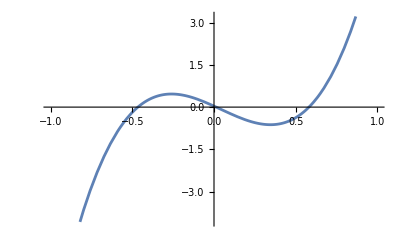

```mathematica
Plot[3/256 (3-226 c3-108 c3^2+840 c3^3),{c3,-1,1}]
```

```mathematica
Solve[D[3/256 (3-226 c3-108 c3^2+840 c3^3),c3]==0, c3]
```

{{c3→1/210 (9-2 √1009)},{c3→1/210 (9+2 √1009)}}

```mathematica
Solve[{preda==targeta, predc==targetc},{c2,c3}]
```

{{c2→1/210 (9-2 √1009),c3→1/210 (9-2 √1009)}}

```mathematica
Maximize[preda/.{c2->-c3}//Simplify,c3]
```

{9/256,{c3→0}}

```mathematica
{preda*256/3,predc*256/3}//Simplify
```

{-8 (3+c2+c3)-3 (1+c2+c3) (-9+61 c2^2+c2 (44-262 c3)+c3 (44+61 c3)),-16/3 (3+c2+c3)-3 (1+c2+c3) (-9+61 c2^2+c2 (44-262 c3)+c3 (44+61 c3))}

```mathematica
solc2c3 = Solve[{preda==23/48, predc==13/24},{c2,c3}]//FullSimplify
```

{}

```mathematica
solc2c3//N
```

{{c2→-1.563,c3→-0.103671},{c2→-0.103671,c3→-1.563}}

```mathematica
Plot3D[preda,{c2, -2,1},{c3, -2,1}]
```

-Graphics3D-

#### JJS

```mathematica
guess = ((λ[1][1] λ[2][2]-λ[1][2] λ[2][1])/(2 π^2));
Table[((bracket[JON[a],JON[b],T[α]]//wick3//pluginIΓ3)/.pluginc)==-KroneckerDelta[a,b]4 (λ[1][α]+λ[2][α])(guess),{a,{1,2}},{b,{1,2}}, {α, {1,2}}]//Simplify
```

{{{True,True},{True,True}},{{True,True},{True,True}}}

#### Decoupled scalar

```mathematica
Sum[Φ[1][k]**Φ[1][j]t3[k].t3[j],{k,3}, {j,3}]//Simplify//MatrixForm
```

(Φ[1][1]**Φ[1][1]+Φ[1][2]**Φ[1][2]+Φ[1][3]**Φ[1][3] | 0
0 | Φ[1][1]**Φ[1][1]+Φ[1][2]**Φ[1][2]+Φ[1][3]**Φ[1][3])

```mathematica
phi = Sum[Φ[1][k]**Φ[1][k], {k,3}]
```

Φ[1][1]**Φ[1][1]+Φ[1][2]**Φ[1][2]+Φ[1][3]**Φ[1][3]

```mathematica
Q0action[phi]
```

0

```mathematica
Q1action[phi]
```

0

```mathematica
bracket[Φ[1][1],ψ[1][1]]//wick2//pluginIΓ2
```

1

```mathematica
bracket[phi, ψ[1][1]]//wick2//pluginIΓ2
```

2 Φ[1][1]

```mathematica
Sum[t3[k].t3[j]bracket[bracket[phi, ψ[1][k]]//wick2//pluginIΓ2, ψ[1][j]]//wick2//pluginIΓ2,{k,3}, {j,3}]
```

{{6,0},{0,6}}

#### Extra symmetries

```mathematica
ClearAll[μ0, μp, μm, G, G1,G2,s1,s3]
```

We  introduce  a  new  set  of  SL2  generators, which  are  symmetric. The indices are assumed to be up 
Correspondingly,  has lower indices as fundamental indices. 
We will use μ, ν for adjoint indices

```mathematica
s3[1] = PauliMatrix[1].LeviCivitaTensor[2];
s3[2] = PauliMatrix[2].LeviCivitaTensor[2];
s3[3] = PauliMatrix[3].LeviCivitaTensor[2];
```

```mathematica
μ0 =Sum[s3[μ][[j,k]]γ[1][j] **Φ[1][μ]**γ[2][k],{μ,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}];
μp =Sum[s3[μ][[j,k]]γ[1][j] **Φ[1][μ]**γ[1][k],{μ,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}];
μm =Sum[s3[μ][[j,k]]γ[2][j] **Φ[1][μ]**γ[2][k],{μ,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}];
Jcurrent[f1_,f2_]:= Sum[β[f1][k]**γ[f2][k],{k,gaugeRepindex}]
```

```mathematica
G[1] = 1/2 Sum[s3[μ][[j,k]]γ[1][j] **Φ[1][μ]**d[1,0][γ[2][k]]-
s3[μ][[j,k]]d[1,0][γ[1][j]] **Φ[1][μ]**γ[2][k]
,{μ,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}];
G[2] = 1/2 Sum[s3[μ][[j,k]]γ[1][j] **Φ[1][μ]**d[0,1][γ[2][k]]-
s3[μ][[j,k]]d[0,1][γ[1][j]] **Φ[1][μ]**γ[2][k]
,{μ,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}];
```

```mathematica
( bracket[G[1], Jcurrent[1,2]]//wick2//pluginIΓ2)== 1/2(d[1,0][μm]+λ[1][1]*μm)//GExpand
( bracket[G[2], Jcurrent[1,2]]//wick2//pluginIΓ2)== 1/2(d[0,1][μm]+λ[1][2]*μm)//GExpand
```

True

True

```mathematica
( bracket[G[1], Jcurrent[2,1]]//wick2//pluginIΓ2)==- 1/2(d[1,0][μp]+λ[1][1]*μp)//GExpand
( bracket[G[2], Jcurrent[2,1]]//wick2//pluginIΓ2)== -1/2(d[0,1][μp]+λ[1][2]*μp)//GExpand
```

True

True

```mathematica
( bracket[G[1], Jcurrent[1,1]-Jcurrent[2,2]]//wick2//pluginIΓ2)== (d[1,0][μ0]+λ[1][1]*μ0)//GExpand
( bracket[G[2], Jcurrent[1,1]-Jcurrent[2,2]]//wick2//pluginIΓ2)== (d[0,1][μ0]+λ[1][2]*μ0)//GExpand
```

True

True

```mathematica
Sum[s3[μ][[j,k]]
bracket[β[1][j]**β[2][k],
bracket[ψ[1][μ],μm]//wick2//pluginIΓ2]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]==-2Jcurrent[1,2]//Simplify
```

True

```mathematica
Sum[s3[μ][[j,k]]
bracket[β[1][j]**β[2][k],
bracket[ψ[1][μ],μp]//wick2//pluginIΓ2]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]==2Jcurrent[2,1]//Simplify
```

True

```mathematica
Sum[s3[μ][[j,k]]
bracket[β[1][j]**β[2][k],
bracket[ψ[1][μ],μ0]//wick2//pluginIΓ2]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]==-(Jcurrent[1,1]-Jcurrent[2,2])//Simplify
```

True

```mathematica
guess = Sum[β[f][k]**d[1,0][γ[f][k]],{f,{1,2}},{k,2}]-1/2 λ[1][1]Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}] -1/2 d[1,0][Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}]];
Sum[s3[μ][[j,k]]
bracket[β[1][j]**β[2][k],
bracket[ψ[1][μ],G[1]]//wick2//pluginIΓ2]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]==guess/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],Simplify]&
(*==-(Jcurrent[1,1]-Jcurrent[2,2])//Simplify*)
```

True

```mathematica
guess = Sum[β[f][k]**d[1,0][γ[f][k]],{f,{1,2}},{k,2}]-1/2 λ[1][1]Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}] -1/2 d[1,0][Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}]];
Sum[s3[μ][[j,k]]
bracket[ψ[1][μ],
bracket[β[1][j]**β[2][k],G[1]]//wick2//pluginIΓ2]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]==guess/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],Simplify]&
(*==-(Jcurrent[1,1]-Jcurrent[2,2])//Simplify*)
```

True

```mathematica
bracket[ψ[1][2],d[1,0][G[1]]]//wick2//pluginIΓ2
```

-1/2 ⅈ d[2,0][γ[1][1]]**γ[2][1]-1/2 ⅈ d[2,0][γ[1][2]]**γ[2][2]+1/2 ⅈ d[2,0][γ[2][1]]**γ[1][1]+1/2 ⅈ d[2,0][γ[2][2]]**γ[1][2]-1/2 ⅈ d[1,0][γ[1][1]]**γ[2][1] λ[1][1]-1/2 ⅈ d[1,0][γ[1][2]]**γ[2][2] λ[1][1]+1/2 ⅈ d[1,0][γ[2][1]]**γ[1][1] λ[1][1]+1/2 ⅈ d[1,0][γ[2][2]]**γ[1][2] λ[1][1]

```mathematica
exp = Sum[s3[μ][[j,k]]
bracket[β[1][j]**β[2][k],
((bracket[ψ[1][μ],d[1,0][G[1]]]//wick2//pluginIΓ2)/.{λ[1][a_]:>λ[2][a]})]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]//GExpand//Simplify;
guess = Sum[β[f][k]**d[1,0][γ[f][k]],{f,{1,2}},{k,2}] -1/2 d[1,0][Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}]];
(exp/.{d[1,0][γ[_][_]]->0})-(d[1,0][guess]
-(λ[1][1]+1/2 λ[2][1] )Sum[γ[f][k]**d[1,0][β[f][k]],{f,{1,2}},{k,2}]
-1/2(λ[1][1])(λ[1][1]+λ[2][1])(Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}]))/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],Simplify]&
```

0

```mathematica
exp = Sum[s3[μ][[j,k]]
bracket[ψ[1][μ],
((bracket[β[1][j]**β[2][k],d[1,0][G[1]]]//wick2//pluginIΓ2)/.{λ[1][a_]:>λ[2][a]})]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]//GExpand//Simplify;
guess = Sum[β[f][k]**d[1,0][γ[f][k]],{f,{1,2}},{k,2}] -1/2 d[1,0][Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}]];
(exp/.{d[1,0][γ[_][_]]->0})-(d[1,0][guess]
-(λ[2][1]+1/2 λ[1][1] )Sum[γ[f][k]**d[1,0][β[f][k]],{f,{1,2}},{k,2}]
-1/2(λ[2][1])(λ[1][1]+λ[2][1])(Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}]))/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],Simplify]&
```

0

```mathematica
Sum[s3[μ][[j,k]]
bracket[ψ[1][μ],β[1][j]**β[2][k],G[1]],{μ,3},{j,2},{k,2}]//product3
```

0

```mathematica
exp1 = Sum[s3[μ][[j,k]]
bracket[G[1],ψ[1][μ],β[1][j]**β[2][k]],{μ,3},{j,2},{k,2}]//product3//Simplify;
exp2 = Sum[s3[μ][[j,k]]
bracket[G[1],β[1][j]**β[2][k],ψ[1][μ]],{μ,3},{j,2},{k,2}]//product3//Simplify;
```

```mathematica
(exp1/.{λ[1][a_]:>λ[2][a], λ[2][a_]:>λ[1][a]})-exp2//Simplify
```

-1/(12 π^2)(-4 d[0,1][β[1][1]]**d[2,0][γ[1][1]]-4 d[0,1][β[1][2]]**d[2,0][γ[1][2]]-4 d[0,1][β[2][1]]**d[2,0][γ[2][1]]-4 d[0,1][β[2][2]]**d[2,0][γ[2][2]]-d[0,1][γ[1][1]]**d[2,0][β[1][1]]-d[0,1][γ[1][2]]**d[2,0][β[1][2]]-d[0,1][γ[2][1]]**d[2,0][β[2][1]]-d[0,1][γ[2][2]]**d[2,0][β[2][2]]+4 d[1,0][β[1][1]]**d[1,1][γ[1][1]]+4 d[1,0][β[1][2]]**d[1,1][γ[1][2]]+4 d[1,0][β[2][1]]**d[1,1][γ[2][1]]+4 d[1,0][β[2][2]]**d[1,1][γ[2][2]]+d[1,0][γ[1][1]]**d[1,1][β[1][1]]+d[1,0][γ[1][2]]**d[1,1][β[1][2]]+d[1,0][γ[2][1]]**d[1,1][β[2][1]]+d[1,0][γ[2][2]]**d[1,1][β[2][2]]-5 d[0,1][β[1][1]]**d[1,0][γ[1][1]] λ[1][1]-5 d[0,1][β[1][2]]**d[1,0][γ[1][2]] λ[1][1]-5 d[0,1][β[2][1]]**d[1,0][γ[2][1]] λ[1][1]-5 d[0,1][β[2][2]]**d[1,0][γ[2][2]] λ[1][1]+d[0,1][γ[1][1]]**d[1,0][β[1][1]] λ[1][1]+d[0,1][γ[1][2]]**d[1,0][β[1][2]] λ[1][1]+d[0,1][γ[2][1]]**d[1,0][β[2][1]] λ[1][1]+d[0,1][γ[2][2]]**d[1,0][β[2][2]] λ[1][1]+d[1,1][β[1][1]]**γ[1][1] λ[1][1]+d[1,1][β[1][2]]**γ[1][2] λ[1][1]+d[1,1][β[2][1]]**γ[2][1] λ[1][1]+d[1,1][β[2][2]]**γ[2][2] λ[1][1]+5 d[1,1][γ[1][1]]**β[1][1] λ[1][1]+5 d[1,1][γ[1][2]]**β[1][2] λ[1][1]+5 d[1,1][γ[2][1]]**β[2][1] λ[1][1]+5 d[1,1][γ[2][2]]**β[2][2] λ[1][1]-d[0,1][β[1][1]]**γ[1][1] (λ[1][1])^2-d[0,1][β[1][2]]**γ[1][2] (λ[1][1])^2-d[0,1][β[2][1]]**γ[2][1] (λ[1][1])^2-d[0,1][β[2][2]]**γ[2][2] (λ[1][1])^2+d[0,1][γ[1][1]]**β[1][1] (λ[1][1])^2+d[0,1][γ[1][2]]**β[1][2] (λ[1][1])^2+d[0,1][γ[2][1]]**β[2][1] (λ[1][1])^2+d[0,1][γ[2][2]]**β[2][2] (λ[1][1])^2+4 d[1,0][β[1][1]]**d[1,0][γ[1][1]] λ[1][2]+4 d[1,0][β[1][2]]**d[1,0][γ[1][2]] λ[1][2]+4 d[1,0][β[2][1]]**d[1,0][γ[2][1]] λ[1][2]+4 d[1,0][β[2][2]]**d[1,0][γ[2][2]] λ[1][2]-d[2,0][β[1][1]]**γ[1][1] λ[1][2]-d[2,0][β[1][2]]**γ[1][2] λ[1][2]-d[2,0][β[2][1]]**γ[2][1] λ[1][2]-d[2,0][β[2][2]]**γ[2][2] λ[1][2]-5 d[2,0][γ[1][1]]**β[1][1] λ[1][2]-5 d[2,0][γ[1][2]]**β[1][2] λ[1][2]-5 d[2,0][γ[2][1]]**β[2][1] λ[1][2]-5 d[2,0][γ[2][2]]**β[2][2] λ[1][2]+d[1,0][β[1][1]]**γ[1][1] λ[1][1] λ[1][2]+d[1,0][β[1][2]]**γ[1][2] λ[1][1] λ[1][2]+d[1,0][β[2][1]]**γ[2][1] λ[1][1] λ[1][2]+d[1,0][β[2][2]]**γ[2][2] λ[1][1] λ[1][2]-d[1,0][γ[1][1]]**β[1][1] λ[1][1] λ[1][2]-d[1,0][γ[1][2]]**β[1][2] λ[1][1] λ[1][2]-d[1,0][γ[2][1]]**β[2][1] λ[1][1] λ[1][2]-d[1,0][γ[2][2]]**β[2][2] λ[1][1] λ[1][2]+d[0,1][β[1][1]]**d[1,0][γ[1][1]] λ[2][1]+d[0,1][β[1][2]]**d[1,0][γ[1][2]] λ[2][1]+d[0,1][β[2][1]]**d[1,0][γ[2][1]] λ[2][1]+d[0,1][β[2][2]]**d[1,0][γ[2][2]] λ[2][1]-2 d[0,1][γ[1][1]]**d[1,0][β[1][1]] λ[2][1]-2 d[0,1][γ[1][2]]**d[1,0][β[1][2]] λ[2][1]-2 d[0,1][γ[2][1]]**d[1,0][β[2][1]] λ[2][1]-2 d[0,1][γ[2][2]]**d[1,0][β[2][2]] λ[2][1]+4 d[1,1][γ[1][1]]**β[1][1] λ[2][1]+4 d[1,1][γ[1][2]]**β[1][2] λ[2][1]+4 d[1,1][γ[2][1]]**β[2][1] λ[2][1]+4 d[1,1][γ[2][2]]**β[2][2] λ[2][1]+d[0,1][β[1][1]]**γ[1][1] λ[1][1] λ[2][1]+d[0,1][β[1][2]]**γ[1][2] λ[1][1] λ[2][1]+d[0,1][β[2][1]]**γ[2][1] λ[1][1] λ[2][1]+d[0,1][β[2][2]]**γ[2][2] λ[1][1] λ[2][1]+3 d[0,1][γ[1][1]]**β[1][1] λ[1][1] λ[2][1]+3 d[0,1][γ[1][2]]**β[1][2] λ[1][1] λ[2][1]+3 d[0,1][γ[2][1]]**β[2][1] λ[1][1] λ[2][1]+3 d[0,1][γ[2][2]]**β[2][2] λ[1][1] λ[2][1]-2 d[1,0][β[1][1]]**γ[1][1] λ[1][2] λ[2][1]-2 d[1,0][β[1][2]]**γ[1][2] λ[1][2] λ[2][1]-2 d[1,0][β[2][1]]**γ[2][1] λ[1][2] λ[2][1]-2 d[1,0][β[2][2]]**γ[2][2] λ[1][2] λ[2][1]-3 d[1,0][γ[1][1]]**β[1][1] λ[1][2] λ[2][1]-3 d[1,0][γ[1][2]]**β[1][2] λ[1][2] λ[2][1]-3 d[1,0][γ[2][1]]**β[2][1] λ[1][2] λ[2][1]-3 d[1,0][γ[2][2]]**β[2][2] λ[1][2] λ[2][1]-d[0,1][γ[1][1]]**β[1][1] (λ[2][1])^2-d[0,1][γ[1][2]]**β[1][2] (λ[2][1])^2-d[0,1][γ[2][1]]**β[2][1] (λ[2][1])^2-d[0,1][γ[2][2]]**β[2][2] (λ[2][1])^2-3 β[1][1]**γ[1][1] λ[1][2] (λ[2][1])^2-3 β[1][2]**γ[1][2] λ[1][2] (λ[2][1])^2-3 β[2][1]**γ[2][1] λ[1][2] (λ[2][1])^2-3 β[2][2]**γ[2][2] λ[1][2] (λ[2][1])^2+d[1,0][β[1][1]]**d[1,0][γ[1][1]] λ[2][2]+d[1,0][β[1][2]]**d[1,0][γ[1][2]] λ[2][2]+d[1,0][β[2][1]]**d[1,0][γ[2][1]] λ[2][2]+d[1,0][β[2][2]]**d[1,0][γ[2][2]] λ[2][2]-4 d[2,0][γ[1][1]]**β[1][1] λ[2][2]-4 d[2,0][γ[1][2]]**β[1][2] λ[2][2]-4 d[2,0][γ[2][1]]**β[2][1] λ[2][2]-4 d[2,0][γ[2][2]]**β[2][2] λ[2][2]+d[1,0][β[1][1]]**γ[1][1] λ[1][1] λ[2][2]+d[1,0][β[1][2]]**γ[1][2] λ[1][1] λ[2][2]+d[1,0][β[2][1]]**γ[2][1] λ[1][1] λ[2][2]+d[1,0][β[2][2]]**γ[2][2] λ[1][1] λ[2][2]+d[1,0][γ[1][1]]**β[1][1] λ[2][1] λ[2][2]+d[1,0][γ[1][2]]**β[1][2] λ[2][1] λ[2][2]+d[1,0][γ[2][1]]**β[2][1] λ[2][1] λ[2][2]+d[1,0][γ[2][2]]**β[2][2] λ[2][1] λ[2][2]+3 β[1][1]**γ[1][1] λ[1][1] λ[2][1] λ[2][2]+3 β[1][2]**γ[1][2] λ[1][1] λ[2][1] λ[2][2]+3 β[2][1]**γ[2][1] λ[1][1] λ[2][1] λ[2][2]+3 β[2][2]**γ[2][2] λ[1][1] λ[2][1] λ[2][2])

### AG + new chiral

#### setup

```mathematica
ClearAll[gaugeindex,flavorindex,gaugeRepindex]
Nf=1;
gaugeindex = Range[1,3,1];
gaugeRepindex = Range[1,2,1];
flavorindex = Range[1,2Nf,1];
gaugeindexu = Range[1,1,1];
flavorindexu = Range[1,1,1];
adjflavorindex = Range[1,1,1];
flavorindexZ = Range[1,1,1];
```

```mathematica
ClearAll[pluginc]
pluginc = {c21->c1,c22->c1,(*,c22->c1,*) c4->c1 };
```

```mathematica
ClearAll[Qaction,Q0action,Q1action,ℐ,t3]
(*fundamental matter*)
t3[1] = PauliMatrix[1] ;t3[2] = PauliMatrix[2] ;t3[3] =PauliMatrix[3];
ℐ =(1/2 c1 Sum[ϵ3[[i,j,k]] b[i]**c[j]**c[k],{i,gaugeindex},{j,gaugeindex},{k,gaugeindex}]+
I/2(-c21)  Sum[t3[i][[j,k]] β[f][j]**c[i]**γ[f][k],{f,{1}},{i,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}]+
I/2(-c22)  Sum[t3[i][[j,k]] β[f][j]**c[i]**γ[f][k],{f,{2}},{i,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}]
+c3 u[1][1]**(γ[1][1]**γ[2][2]-γ[1][2]**γ[2][1])
+c4 Sum[ϵ3[[i,j,k]] c[i]**ψ[f][j]**Φ[f][k],{i,gaugeindex},{j,gaugeindex},{k,gaugeindex},{f,adjflavorindex}]
+c5 Sum[Z[1]**Φ[1][k]**Φ[1][k],{k,gaugeindex}]
)/.pluginc;

Q0action[exp_]:=((bracket[ℐ,exp]//wick2//pluginIΓ2)//GExpand)/.{λ[_][_]:>0}
Q1action[exp_]:=((bracket[ℐ,ℐ,exp]//wick3//pluginIΓ3)//GExpand)/.{λ[_][_]:>0}
```

#### checking Q^2

```mathematica
(β[1][1]//Q0action//Q0action)/.pluginc//Simplify
(γ[1][1]//Q0action//Q0action)/.pluginc//Simplify
(β[1][1]**γ[1][1]//Q0action//Q0action)/.pluginc//Simplify
(β[1][1]**γ[2][1]//Q0action//Q0action)/.pluginc//Simplify
(β[1][1]**γ[2][2]//Q0action//Q0action)/.pluginc//Simplify
(b[1]**c[2]//Q0action//Q0action)/.pluginc//Simplify
u[1][1]**d[1,0][βu[1][1]]//Q0action//Q0action
(u[1][1]**d[1,0][b[1]]**Φ[1][1]//Q0action//Q0action)/.pluginc//Simplify
```

0

0

0

«5 more identical outputs»

```mathematica
(Z[1]**u[1][1]**d[1,0][b[1]]**Φ[1][1]//Q0action//Q0action)/.pluginc//Simplify
```

0

```mathematica
(βZ[1]**u[1][1]**γ[1][2]**Φ[1][1]//Q0action//Q0action)/.pluginc//Simplify
```

0

#### current

```mathematica
Jcurrent[f1_,f2_]:= Sum[β[f1][k]**γ[f2][k],{k,gaugeRepindex}]
```

```mathematica
Q0action[Jcurrent[1,1]-Jcurrent[2,2]]//Simplify
Q0action[Jcurrent[1,2]]/.pluginc//Simplify
Q0action[Jcurrent[2,1]]/.pluginc//Simplify
Q0action[Jcurrent[1,1]]/.pluginc//Simplify
```

0

0

0

c3 (u[1][1]**γ[1][1]**γ[2][2]-u[1][1]**γ[1][2]**γ[2][1])

```mathematica
JON[A_] :=Sum[TON[2][[A]][[i,j]] Jcurrent[i,j],{i,2},{j,2}]
```

```mathematica
Q0action[JON[1]]
Q0action[JON[2]]
Q0action[JON[3]]
Q0action[JON[4]]
```

0

0

0

√2 c3 u[1][1]**γ[1][1]**γ[2][2]-√2 c3 u[1][1]**γ[1][2]**γ[2][1]

```mathematica
Q1action[JON[1]]
Q1action[JON[2]]
Q1action[JON[3]]
Q1action[JON[4]]
```

0

0

0

(√2 c1^2 d[0,1][c[1]]**d[1,0][c[1]])/π^2+(√2 c1^2 d[0,1][c[2]]**d[1,0][c[2]])/π^2+(√2 c1^2 d[0,1][c[3]]**d[1,0][c[3]])/π^2

```mathematica
Table[(bracket[JON[a],JON[b]]//wick2//pluginIΓ2)-(-1) Sum[fabc[2][a,b,c]JON[c],{c,3}],{a,3},{b,3}]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Table[(bracket[JON[a],JON[b],JON[c]]//wick3//pluginIΓ3)-c1(-1) dabc[2][a,b,c]((λ[1][1] λ[2][2]-λ[1][2] λ[2][1])/(2 π^2)),{a,{1}},{b,{1}},{c,{3}}]//Simplify
```

{{{0}}}

#### stress tensor

```mathematica
T[1]=(  c6 Sum[b[i]**d[1,0][c[i]],{i,gaugeindex}]+
+(1+c6)Sum[c[i]**d[1,0][b[i]],{i,gaugeindex}]
+ c7 Sum[γ[f][k]**d[1,0][β[f][k]],{f,{1}},{k,2}]
+(1+c7) Sum[β[f][k]**d[1,0][γ[f][k]],{f,{1}},{k,2}]
+c8 Sum[γ[f][k]**d[1,0][β[f][k]],{f,{2}},{k,2}]
+(1+c8) Sum[β[f][k]**d[1,0][γ[f][k]],{f,{2}},{k,2}]
+c9 u[1][1]**d[1,0][βu[1][1]]
+(1+c9)   βu[1][1]**d[1,0][u[1][1]]
+c10 Sum[Φ[f][k]**d[1,0][ψ[f][k]],{f,1},{k, gaugeindex}]
+(1+c10) Sum[ψ[f][k]**d[1,0][Φ[f][k]],{f,1},{k, gaugeindex}]
+c11 Z[1]**d[1,0][βZ[1]]
+(1+c11)βZ[1]**d[1,0][Z[1]]
);
T[2]=(  c6 Sum[b[i]**d[0,1][c[i]],{i,gaugeindex}]+
+(1+c6)Sum[c[i]**d[0,1][b[i]],{i,gaugeindex}]
+ c7 Sum[γ[f][k]**d[0,1][β[f][k]],{f,{1}},{k,2}]
+(1+c7) Sum[β[f][k]**d[0,1][γ[f][k]],{f,{1}},{k,2}]
+c8 Sum[γ[f][k]**d[0,1][β[f][k]],{f,{2}},{k,2}]
+(1+c8) Sum[β[f][k]**d[0,1][γ[f][k]],{f,{2}},{k,2}]
+c9 u[1][1]**d[0,1][βu[1][1]]
+(1+c9)   βu[1][1]**d[0,1][u[1][1]]
+c10 Sum[Φ[f][k]**d[0,1][ψ[f][k]],{f,1},{k, gaugeindex}]
+(1+c10) Sum[ψ[f][k]**d[0,1][Φ[f][k]],{f,1},{k, gaugeindex}]
+c11 Z[1]**d[0,1][βZ[1]]
+(1+c11)βZ[1]**d[0,1][Z[1]]
);

Q0action[T[1]]/.pluginc/.{c6->-1,c9->-(1+c7+c8), c11->-1-2c10}/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}//Collect[#,ff[___],Simplify]&
Q0action[T[2]]/.pluginc/.{c6->-1,c9->-(1+c7+c8), c11->-1-2c10}/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}//Collect[#,ff[___],Simplify]&
```

0

0

```mathematica
Q1action[T[1]]/.pluginc/.{c6->-1,c9->-(1+c7+c8), c11->-1-2c10}/.{c10->-1/4(1+c7+c8)}/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}//Collect[#,ff[___],Simplify]&
```

0

```mathematica
Q1action[T[2]]/.pluginc/.{c6->-1,c9->-(1+c7+c8), c11->-1-2c10}/.{c10->-1/4(1+c7+c8)}/.{NonCommutativeMultiply->ff}/.{λ[v_][i_]:>0}//Collect[#,ff[___],Simplify]&
```

0

```mathematica
Table[((bracket[T[i1],T[i2]]//wick2//pluginIΓ2)-((T[i1]  λ[1][i2]+T[i2]  λ[1][i1]+dd[i1][T[i2]] ))//GExpand//Simplify)/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],FullSimplify]&
,{i1,2},{i2,2}]
```

{{0,0},{0,0}}

```mathematica
ClearAll[temp]
temp[i1_,i2_,i3_]:=temp[i1,i2,i3]=(bracket[T[i1],T[i2],T[i3]]//wick3//pluginIΓ3//Expand)
```

```mathematica
ClearAll[solcc]
solcc = {cc1->-9/64 (-3+9 c7+35 c7^2+23 c7^3+9 c8-58 c7 c8-59 c7^2 c8+35 c8^2-59 c7 c8^2+23 c8^3),cc2->-3/2 (1+c7+c8)};
```

```mathematica
Table[
Print[i1,i2,i3];
Print[temp[i1,i2,i3]==Block[{ϵ2},
(cc1) partN4[i1,i2,i3]+(cc2) partfree[i1,i2,i3]
]/.pluginc/.{c6->-1,c9->-(1+c7+c8), c11->-1-2c10}/.{c10->-1/4(1+c7+c8)}/.solcc//Simplify]
,{i1,2},{i2,2},{i3,2}
]
```

111

True

112

True

121

True

122

True

211

True

212

True

221

True

222

True

{{{Null,Null},{Null,Null}},{{Null,Null},{Null,Null}}}

```mathematica
actocoef[a_,c_]:={-4/3(2a-3c),16(a-c)};
coeftoac[coefN4SYM_,coefchiral_] := {-3/16 (-coefchiral-4 coefN4SYM),1/8 (coefchiral+6 coefN4SYM)};
```

```mathematica
{preda, predc }= coeftoac[cc1, cc2]/.pluginc/.{c6->-1,c9->-(1+c7+c8), c11->-1-2c10}/.{c10->-1/4(1+c7+c8)}/.solcc//Simplify
```

{-9/256 (-1+69 c7^3+35 c8+105 c8^2+69 c8^3-3 c7^2 (-35+59 c8)+c7 (35-174 c8-177 c8^2)),-3/256 (-11+207 c7^3+97 c8+315 c8^2+207 c8^3-9 c7^2 (-35+59 c8)+c7 (97-522 c8-531 c8^2))}

```mathematica
targeta = (-4698+1009 √1009)/58800;
targetc =(486+487 √1009)/29400;
```

```mathematica
preda/.{c7->c8}//Simplify
```

9/256 (1-70 c8-36 c8^2+216 c8^3)

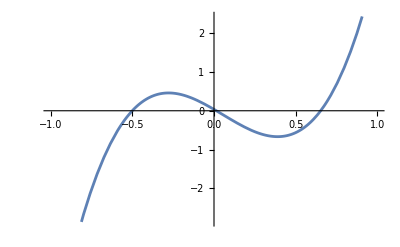

```mathematica
Plot[9/256 (1-70 c8-36 c8^2+216 c8^3),{c8,-1,1}]
```

```mathematica
preda/.{c7->c8}/.Solve[D[preda/.{c7->c8},c8]==0, c8]
predc/.{c7->c8}/.Solve[D[preda/.{c7->c8},c8]==0, c8]
```

{11/24,-2/3}

{1/2,-1/2}

```mathematica
{(12 Nc^2-5Nc-5)/(24(Nc+1)),(3 Nc^2-Nc-1)/(6(Nc+1))}/.{Nc->2}
```

{11/24,1/2}

```mathematica
Solve[{preda==targeta, predc==targetc},{c2,c3}]
```

{{c2→1/210 (9-2 √1009),c3→1/210 (9-2 √1009)}}

```mathematica
Maximize[preda/.{c2->-c3}//Simplify,c3]
```

{9/256,{c3→0}}

```mathematica
{preda*256/3,predc*256/3}//Simplify
```

{-8 (3+c2+c3)-3 (1+c2+c3) (-9+61 c2^2+c2 (44-262 c3)+c3 (44+61 c3)),-16/3 (3+c2+c3)-3 (1+c2+c3) (-9+61 c2^2+c2 (44-262 c3)+c3 (44+61 c3))}

```mathematica
solc2c3 = Solve[{preda==23/48, predc==13/24},{c2,c3}]//FullSimplify
```

{}

```mathematica
solc2c3//N
```

{{c2→-1.563,c3→-0.103671},{c2→-0.103671,c3→-1.563}}

```mathematica
Plot3D[preda,{c2, -2,1},{c3, -2,1}]
```

-Graphics3D-

#### JJS

```mathematica
guess = ((λ[1][1] λ[2][2]-λ[1][2] λ[2][1])/(2 π^2));
Table[((bracket[JON[a],JON[b],T[α]]//wick3//pluginIΓ3)/.pluginc)==-KroneckerDelta[a,b]4 (λ[1][α]+λ[2][α])(guess),{a,{1,2}},{b,{1,2}}, {α, {1,2}}]//Simplify
```

{{{True,True},{True,True}},{{True,True},{True,True}}}

#### Decoupled scalar

```mathematica
Sum[Φ[1][k]**Φ[1][j]t3[k].t3[j],{k,3}, {j,3}]//Simplify//MatrixForm
```

(Φ[1][1]**Φ[1][1]+Φ[1][2]**Φ[1][2]+Φ[1][3]**Φ[1][3] | 0
0 | Φ[1][1]**Φ[1][1]+Φ[1][2]**Φ[1][2]+Φ[1][3]**Φ[1][3])

```mathematica
phi = Sum[Φ[1][k]**Φ[1][k], {k,3}]
```

Φ[1][1]**Φ[1][1]+Φ[1][2]**Φ[1][2]+Φ[1][3]**Φ[1][3]

```mathematica
Q0action[phi]
```

0

```mathematica
Q1action[phi]
```

0

```mathematica
bracket[Φ[1][1],ψ[1][1]]//wick2//pluginIΓ2
```

1

```mathematica
bracket[phi, ψ[1][1]]//wick2//pluginIΓ2
```

2 Φ[1][1]

```mathematica
Sum[t3[k].t3[j]bracket[bracket[phi, ψ[1][k]]//wick2//pluginIΓ2, ψ[1][j]]//wick2//pluginIΓ2,{k,3}, {j,3}]
```

{{6,0},{0,6}}

#### Extra symmetries

```mathematica
ClearAll[μ0, μp, μm, G, G1,G2,s1,s3]
```

We  introduce  a  new  set  of  SL2  generators, which  are  symmetric. The indices are assumed to be up 
Correspondingly,  has lower indices as fundamental indices. 
We will use μ, ν for adjoint indices

```mathematica
s3[1] =LeviCivitaTensor[2]. PauliMatrix[1];
s3[2] =LeviCivitaTensor[2]. PauliMatrix[2];
s3[3] =LeviCivitaTensor[2]. PauliMatrix[3];
```

```mathematica
μ0 =Sum[s3[μ][[j,k]]γ[1][j] **Φ[1][μ]**γ[2][k],{μ,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}];
μp =Sum[s3[μ][[j,k]]γ[1][j] **Φ[1][μ]**γ[1][k],{μ,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}];
μm =Sum[s3[μ][[j,k]]γ[2][j] **Φ[1][μ]**γ[2][k],{μ,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}];
Jcurrent[f1_,f2_]:= Sum[β[f1][k]**γ[f2][k],{k,gaugeRepindex}]
```

```mathematica
JR = Sum[β[1][k]**γ[1][k]+β[2][k]**γ[2][k],{k,gaugeRepindex}] -1/2 Sum[ψ[1][j]**Φ[1][j],{j, gaugeindex}] -2 u[1][1]**βu[1][1]+ Z[1]**βZ[1]; (*the coefs are fixed uniquely by Q0 and Q1 closedness below*)
Q0action[JR]/.pluginc/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],Simplify]&
Q1action[JR]/.pluginc/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],Simplify]&
```

0

0

```mathematica
G[1] = 1/2 Sum[s3[μ][[j,k]]γ[1][j] **Φ[1][μ]**d[1,0][γ[2][k]]-
s3[μ][[j,k]]d[1,0][γ[1][j]] **Φ[1][μ]**γ[2][k]
,{μ,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}]+ (ⅈ c1)/(2c3) βu[1][1]**Sum[Φ[1][μ]**d[1,0][c[μ]], {μ, gaugeindex}];

G[2] = 1/2 Sum[s3[μ][[j,k]]γ[1][j] **Φ[1][μ]**d[0,1][γ[2][k]]-
s3[μ][[j,k]]d[0,1][γ[1][j]] **Φ[1][μ]**γ[2][k]
,{μ,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}]+ (ⅈ c1)/(2c3) βu[1][1]**Sum[Φ[1][μ]**d[0,1][c[μ]], {μ, gaugeindex}];
```

```mathematica
Q0action[G[1]]/.{NonCommutativeMultiply->ff}/.{λ[_][_]:>0}//Collect[#,ff[___],Simplify]&
Q0action[G[2]]/.{NonCommutativeMultiply->ff}/.{λ[_][_]:>0}//Collect[#,ff[___],Simplify]&
```

0

0

```mathematica
Q1action[G[1]]/.{NonCommutativeMultiply->ff}/.{λ[_][_]:>0}//Collect[#,ff[___],Simplify]&
Q1action[G[2]]/.{NonCommutativeMultiply->ff}/.{λ[_][_]:>0}//Collect[#,ff[___],Simplify]&
```

0

0

```mathematica
( bracket[G[1], Jcurrent[1,2]]//wick2//pluginIΓ2)== 1/2(d[1,0][μm]+λ[1][1]*μm)//GExpand
( bracket[G[2], Jcurrent[1,2]]//wick2//pluginIΓ2)== 1/2(d[0,1][μm]+λ[1][2]*μm)//GExpand
```

True

True

```mathematica
( bracket[G[1], Jcurrent[2,1]]//wick2//pluginIΓ2)==- 1/2(d[1,0][μp]+λ[1][1]*μp)//GExpand
( bracket[G[2], Jcurrent[2,1]]//wick2//pluginIΓ2)== -1/2(d[0,1][μp]+λ[1][2]*μp)//GExpand
```

True

True

```mathematica
( bracket[G[1], Jcurrent[1,1]-Jcurrent[2,2]]//wick2//pluginIΓ2)== (d[1,0][μ0]+λ[1][1]*μ0)//GExpand
( bracket[G[2], Jcurrent[1,1]-Jcurrent[2,2]]//wick2//pluginIΓ2)== (d[0,1][μ0]+λ[1][2]*μ0)//GExpand
```

True

True

```mathematica
Sum[s3[μ][[j,k]]
bracket[β[1][j]**β[2][k],
bracket[ψ[1][μ],μm]//wick2//pluginIΓ2]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]==-2Jcurrent[1,2]//Simplify
```

True

```mathematica
Sum[s3[μ][[j,k]]
bracket[β[1][j]**β[2][k],
bracket[ψ[1][μ],μp]//wick2//pluginIΓ2]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]==2Jcurrent[2,1]//Simplify
```

True

```mathematica
Sum[s3[μ][[j,k]]
bracket[β[1][j]**β[2][k],
bracket[ψ[1][μ],μ0]//wick2//pluginIΓ2]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]==-(Jcurrent[1,1]-Jcurrent[2,2])//Simplify
```

True

```mathematica
guess = Sum[β[f][k]**d[1,0][γ[f][k]],{f,{1,2}},{k,2}]-1/2 λ[1][1]Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}] -1/2 d[1,0][Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}]];
Sum[s3[μ][[j,k]]
bracket[β[1][j]**β[2][k],
bracket[ψ[1][μ],G[1]]//wick2//pluginIΓ2]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]==guess/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],Simplify]&
(*==-(Jcurrent[1,1]-Jcurrent[2,2])//Simplify*)
```

True

```mathematica
guess = Sum[β[f][k]**d[1,0][γ[f][k]],{f,{1,2}},{k,2}]-1/2 λ[1][1]Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}] -1/2 d[1,0][Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}]];
Sum[s3[μ][[j,k]]
bracket[ψ[1][μ],
bracket[β[1][j]**β[2][k],G[1]]//wick2//pluginIΓ2]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]==guess/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],Simplify]&
(*==-(Jcurrent[1,1]-Jcurrent[2,2])//Simplify*)
```

True

```mathematica
bracket[ψ[1][2],d[1,0][G[1]]]//wick2//pluginIΓ2
```

-1/2 ⅈ d[2,0][γ[1][1]]**γ[2][1]-1/2 ⅈ d[2,0][γ[1][2]]**γ[2][2]+1/2 ⅈ d[2,0][γ[2][1]]**γ[1][1]+1/2 ⅈ d[2,0][γ[2][2]]**γ[1][2]-1/2 ⅈ d[1,0][γ[1][1]]**γ[2][1] λ[1][1]-1/2 ⅈ d[1,0][γ[1][2]]**γ[2][2] λ[1][1]+1/2 ⅈ d[1,0][γ[2][1]]**γ[1][1] λ[1][1]+1/2 ⅈ d[1,0][γ[2][2]]**γ[1][2] λ[1][1]

```mathematica
exp = Sum[s3[μ][[j,k]]
bracket[β[1][j]**β[2][k],
((bracket[ψ[1][μ],d[1,0][G[1]]]//wick2//pluginIΓ2)/.{λ[1][a_]:>λ[2][a]})]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]//GExpand//Simplify;
guess = Sum[β[f][k]**d[1,0][γ[f][k]],{f,{1,2}},{k,2}] -1/2 d[1,0][Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}]];
(exp/.{d[1,0][γ[_][_]]->0})-(d[1,0][guess]
-(λ[1][1]+1/2 λ[2][1] )Sum[γ[f][k]**d[1,0][β[f][k]],{f,{1,2}},{k,2}]
-1/2(λ[1][1])(λ[1][1]+λ[2][1])(Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}]))/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],Simplify]&
```

0

```mathematica
exp = Sum[s3[μ][[j,k]]
bracket[ψ[1][μ],
((bracket[β[1][j]**β[2][k],d[1,0][G[1]]]//wick2//pluginIΓ2)/.{λ[1][a_]:>λ[2][a]})]//wick2//pluginIΓ2,
{μ,3},{j,2},{k,2}]//GExpand//Simplify;
guess = Sum[β[f][k]**d[1,0][γ[f][k]],{f,{1,2}},{k,2}] -1/2 d[1,0][Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}]];
(exp/.{d[1,0][γ[_][_]]->0})-(d[1,0][guess]
-(λ[2][1]+1/2 λ[1][1] )Sum[γ[f][k]**d[1,0][β[f][k]],{f,{1,2}},{k,2}]
-1/2(λ[2][1])(λ[1][1]+λ[2][1])(Sum[γ[f][k]**β[f][k],{f,{1,2}},{k,2}]))/.{NonCommutativeMultiply->ff}//Collect[#,ff[___],Simplify]&
```

0

```mathematica
Sum[s3[μ][[j,k]]
bracket[ψ[1][μ],β[1][j]**β[2][k],G[1]],{μ,3},{j,2},{k,2}]//product3
```

0

```mathematica
exp1 = Sum[s3[μ][[j,k]]
bracket[G[1],ψ[1][μ],β[1][j]**β[2][k]],{μ,3},{j,2},{k,2}]//product3//Simplify;
exp2 = Sum[s3[μ][[j,k]]
bracket[G[1],β[1][j]**β[2][k],ψ[1][μ]],{μ,3},{j,2},{k,2}]//product3//Simplify;
```

```mathematica
(exp1/.{λ[1][a_]:>λ[2][a], λ[2][a_]:>λ[1][a]})-exp2//Simplify
```

-1/(12 π^2)(-4 d[0,1][β[1][1]]**d[2,0][γ[1][1]]-4 d[0,1][β[1][2]]**d[2,0][γ[1][2]]-4 d[0,1][β[2][1]]**d[2,0][γ[2][1]]-4 d[0,1][β[2][2]]**d[2,0][γ[2][2]]-d[0,1][γ[1][1]]**d[2,0][β[1][1]]-d[0,1][γ[1][2]]**d[2,0][β[1][2]]-d[0,1][γ[2][1]]**d[2,0][β[2][1]]-d[0,1][γ[2][2]]**d[2,0][β[2][2]]+4 d[1,0][β[1][1]]**d[1,1][γ[1][1]]+4 d[1,0][β[1][2]]**d[1,1][γ[1][2]]+4 d[1,0][β[2][1]]**d[1,1][γ[2][1]]+4 d[1,0][β[2][2]]**d[1,1][γ[2][2]]+d[1,0][γ[1][1]]**d[1,1][β[1][1]]+d[1,0][γ[1][2]]**d[1,1][β[1][2]]+d[1,0][γ[2][1]]**d[1,1][β[2][1]]+d[1,0][γ[2][2]]**d[1,1][β[2][2]]-5 d[0,1][β[1][1]]**d[1,0][γ[1][1]] λ[1][1]-5 d[0,1][β[1][2]]**d[1,0][γ[1][2]] λ[1][1]-5 d[0,1][β[2][1]]**d[1,0][γ[2][1]] λ[1][1]-5 d[0,1][β[2][2]]**d[1,0][γ[2][2]] λ[1][1]+d[0,1][γ[1][1]]**d[1,0][β[1][1]] λ[1][1]+d[0,1][γ[1][2]]**d[1,0][β[1][2]] λ[1][1]+d[0,1][γ[2][1]]**d[1,0][β[2][1]] λ[1][1]+d[0,1][γ[2][2]]**d[1,0][β[2][2]] λ[1][1]+d[1,1][β[1][1]]**γ[1][1] λ[1][1]+d[1,1][β[1][2]]**γ[1][2] λ[1][1]+d[1,1][β[2][1]]**γ[2][1] λ[1][1]+d[1,1][β[2][2]]**γ[2][2] λ[1][1]+5 d[1,1][γ[1][1]]**β[1][1] λ[1][1]+5 d[1,1][γ[1][2]]**β[1][2] λ[1][1]+5 d[1,1][γ[2][1]]**β[2][1] λ[1][1]+5 d[1,1][γ[2][2]]**β[2][2] λ[1][1]-d[0,1][β[1][1]]**γ[1][1] (λ[1][1])^2-d[0,1][β[1][2]]**γ[1][2] (λ[1][1])^2-d[0,1][β[2][1]]**γ[2][1] (λ[1][1])^2-d[0,1][β[2][2]]**γ[2][2] (λ[1][1])^2+d[0,1][γ[1][1]]**β[1][1] (λ[1][1])^2+d[0,1][γ[1][2]]**β[1][2] (λ[1][1])^2+d[0,1][γ[2][1]]**β[2][1] (λ[1][1])^2+d[0,1][γ[2][2]]**β[2][2] (λ[1][1])^2+4 d[1,0][β[1][1]]**d[1,0][γ[1][1]] λ[1][2]+4 d[1,0][β[1][2]]**d[1,0][γ[1][2]] λ[1][2]+4 d[1,0][β[2][1]]**d[1,0][γ[2][1]] λ[1][2]+4 d[1,0][β[2][2]]**d[1,0][γ[2][2]] λ[1][2]-d[2,0][β[1][1]]**γ[1][1] λ[1][2]-d[2,0][β[1][2]]**γ[1][2] λ[1][2]-d[2,0][β[2][1]]**γ[2][1] λ[1][2]-d[2,0][β[2][2]]**γ[2][2] λ[1][2]-5 d[2,0][γ[1][1]]**β[1][1] λ[1][2]-5 d[2,0][γ[1][2]]**β[1][2] λ[1][2]-5 d[2,0][γ[2][1]]**β[2][1] λ[1][2]-5 d[2,0][γ[2][2]]**β[2][2] λ[1][2]+d[1,0][β[1][1]]**γ[1][1] λ[1][1] λ[1][2]+d[1,0][β[1][2]]**γ[1][2] λ[1][1] λ[1][2]+d[1,0][β[2][1]]**γ[2][1] λ[1][1] λ[1][2]+d[1,0][β[2][2]]**γ[2][2] λ[1][1] λ[1][2]-d[1,0][γ[1][1]]**β[1][1] λ[1][1] λ[1][2]-d[1,0][γ[1][2]]**β[1][2] λ[1][1] λ[1][2]-d[1,0][γ[2][1]]**β[2][1] λ[1][1] λ[1][2]-d[1,0][γ[2][2]]**β[2][2] λ[1][1] λ[1][2]+d[0,1][β[1][1]]**d[1,0][γ[1][1]] λ[2][1]+d[0,1][β[1][2]]**d[1,0][γ[1][2]] λ[2][1]+d[0,1][β[2][1]]**d[1,0][γ[2][1]] λ[2][1]+d[0,1][β[2][2]]**d[1,0][γ[2][2]] λ[2][1]-2 d[0,1][γ[1][1]]**d[1,0][β[1][1]] λ[2][1]-2 d[0,1][γ[1][2]]**d[1,0][β[1][2]] λ[2][1]-2 d[0,1][γ[2][1]]**d[1,0][β[2][1]] λ[2][1]-2 d[0,1][γ[2][2]]**d[1,0][β[2][2]] λ[2][1]+4 d[1,1][γ[1][1]]**β[1][1] λ[2][1]+4 d[1,1][γ[1][2]]**β[1][2] λ[2][1]+4 d[1,1][γ[2][1]]**β[2][1] λ[2][1]+4 d[1,1][γ[2][2]]**β[2][2] λ[2][1]+d[0,1][β[1][1]]**γ[1][1] λ[1][1] λ[2][1]+d[0,1][β[1][2]]**γ[1][2] λ[1][1] λ[2][1]+d[0,1][β[2][1]]**γ[2][1] λ[1][1] λ[2][1]+d[0,1][β[2][2]]**γ[2][2] λ[1][1] λ[2][1]+3 d[0,1][γ[1][1]]**β[1][1] λ[1][1] λ[2][1]+3 d[0,1][γ[1][2]]**β[1][2] λ[1][1] λ[2][1]+3 d[0,1][γ[2][1]]**β[2][1] λ[1][1] λ[2][1]+3 d[0,1][γ[2][2]]**β[2][2] λ[1][1] λ[2][1]-2 d[1,0][β[1][1]]**γ[1][1] λ[1][2] λ[2][1]-2 d[1,0][β[1][2]]**γ[1][2] λ[1][2] λ[2][1]-2 d[1,0][β[2][1]]**γ[2][1] λ[1][2] λ[2][1]-2 d[1,0][β[2][2]]**γ[2][2] λ[1][2] λ[2][1]-3 d[1,0][γ[1][1]]**β[1][1] λ[1][2] λ[2][1]-3 d[1,0][γ[1][2]]**β[1][2] λ[1][2] λ[2][1]-3 d[1,0][γ[2][1]]**β[2][1] λ[1][2] λ[2][1]-3 d[1,0][γ[2][2]]**β[2][2] λ[1][2] λ[2][1]-d[0,1][γ[1][1]]**β[1][1] (λ[2][1])^2-d[0,1][γ[1][2]]**β[1][2] (λ[2][1])^2-d[0,1][γ[2][1]]**β[2][1] (λ[2][1])^2-d[0,1][γ[2][2]]**β[2][2] (λ[2][1])^2-3 β[1][1]**γ[1][1] λ[1][2] (λ[2][1])^2-3 β[1][2]**γ[1][2] λ[1][2] (λ[2][1])^2-3 β[2][1]**γ[2][1] λ[1][2] (λ[2][1])^2-3 β[2][2]**γ[2][2] λ[1][2] (λ[2][1])^2+d[1,0][β[1][1]]**d[1,0][γ[1][1]] λ[2][2]+d[1,0][β[1][2]]**d[1,0][γ[1][2]] λ[2][2]+d[1,0][β[2][1]]**d[1,0][γ[2][1]] λ[2][2]+d[1,0][β[2][2]]**d[1,0][γ[2][2]] λ[2][2]-4 d[2,0][γ[1][1]]**β[1][1] λ[2][2]-4 d[2,0][γ[1][2]]**β[1][2] λ[2][2]-4 d[2,0][γ[2][1]]**β[2][1] λ[2][2]-4 d[2,0][γ[2][2]]**β[2][2] λ[2][2]+d[1,0][β[1][1]]**γ[1][1] λ[1][1] λ[2][2]+d[1,0][β[1][2]]**γ[1][2] λ[1][1] λ[2][2]+d[1,0][β[2][1]]**γ[2][1] λ[1][1] λ[2][2]+d[1,0][β[2][2]]**γ[2][2] λ[1][1] λ[2][2]+d[1,0][γ[1][1]]**β[1][1] λ[2][1] λ[2][2]+d[1,0][γ[1][2]]**β[1][2] λ[2][1] λ[2][2]+d[1,0][γ[2][1]]**β[2][1] λ[2][1] λ[2][2]+d[1,0][γ[2][2]]**β[2][2] λ[2][1] λ[2][2]+3 β[1][1]**γ[1][1] λ[1][1] λ[2][1] λ[2][2]+3 β[1][2]**γ[1][2] λ[1][1] λ[2][1] λ[2][2]+3 β[2][1]**γ[2][1] λ[1][1] λ[2][1] λ[2][2]+3 β[2][2]**γ[2][2] λ[1][1] λ[2][1] λ[2][2])

### (A1, A3)

#### setup

```mathematica
(*b[i],c[i], gaugeindex*)
(*γ[j][i],β[j][i],{j,flavorindex},{i,gaugeRepindex}*)
(*Φ[j][i],ψ[j][i],{j,adjflavorindex},{i, gaugeindex}*)
(*u[j][i],βu[j][i],{j,flavorindexu},{i,gaugeindexu}*)
(*Z[j],βZ[j],{j, flavorindexZ}*)
```

```mathematica
ClearAll[gaugeindex,flavorindex,gaugeRepindex]
Nf=1;
flavorindex = Range[1,2Nf,1];

gaugeindex = Range[1,3,1];
gaugeRepindex = Range[1,2,1];
gaugeindexu = Range[1,1,1];
flavorindexu = Range[1,2,1];
adjflavorindex = Range[1,1,1];
flavorindexZ = Range[1,0,1];

ClearAll[Qaction,Q0action,Q1action,Q2action,ℐ,t3]
(*fundamental matter*)
t3[1] = PauliMatrix[1] ;t3[2] = PauliMatrix[2] ;t3[3] =PauliMatrix[3];
ℐ =(1/2 c1 Sum[ϵ3[[i,j,k]] b[i]**c[j]**c[k],{i,gaugeindex},{j,gaugeindex},{k,gaugeindex}]+
I/2(-c1)  Sum[t3[i][[j,k]] β[f][j]**c[i]**γ[f][k],{f,2},{i,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}]
+c2  u[1][1]**(γ[1][1]**γ[2][2]-γ[1][2]**γ[2][1])
+c1  Sum[ϵ3[[i,j,k]] c[i]**ψ[f][j]**Φ[f][k],{i,gaugeindex},{j,gaugeindex},{k,gaugeindex},{f,adjflavorindex}]+c3 Sum[u[2][1]**Φ[f][k]**Φ[f][k],{f,adjflavorindex}, {k,gaugeindex}]
);

Q0action[exp_]:=((bracket[ℐ,exp]//wick2//pluginIΓ2)/.{λ[x_][y_]:>0})//GExpand
Q1action[exp_]:=(((bracket[ℐ,ℐ,exp]//wick3//pluginIΓ3)/.{λ[x_][y_]:>0})/2!)//GExpand
Q2action[exp_]:=(((bracket[ℐ,ℐ,ℐ,exp]+bracket[ℐ,ℐ,exp,ℐ]//wick4//pluginIΓ4)/3!)/.{λ[x_][y_]:>0})//GExpand
```

```mathematica
γ[1][1]//Q0action
β[1][1]//Q0action
Φ[1][1]//Q0action
ψ[1][1]//Q0action
βu[2][1]//Q0action
b[1]//Q0action
```

-1/2 ⅈ c1 c[1]**γ[1][2]-1/2 c1 c[2]**γ[1][2]-1/2 ⅈ c1 c[3]**γ[1][1]

1/2 ⅈ c1 c[1]**β[1][2]-1/2 c1 c[2]**β[1][2]+1/2 ⅈ c1 c[3]**β[1][1]+c2 u[1][1]**γ[2][2]

c1 c[2]**Φ[1][3]-c1 c[3]**Φ[1][2]

c1 c[2]**ψ[1][3]-c1 c[3]**ψ[1][2]+2 c3 u[2][1]**Φ[1][1]

c3 Φ[1][1]**Φ[1][1]+c3 Φ[1][2]**Φ[1][2]+c3 Φ[1][3]**Φ[1][3]

-c1 b[2]**c[3]+c1 b[3]**c[2]+1/2 ⅈ c1 β[1][1]**γ[1][2]+1/2 ⅈ c1 β[1][2]**γ[1][1]+1/2 ⅈ c1 β[2][1]**γ[2][2]+1/2 ⅈ c1 β[2][2]**γ[2][1]-c1 Φ[1][2]**ψ[1][3]+c1 Φ[1][3]**ψ[1][2]

#### checking Q^2

```mathematica
pluginc = {};
```

```mathematica
(u[2][1]**Φ[1][1]**u[1][1]//Q0action//Q0action)//Simplify
```

0

```mathematica
(β[1][1]//Q0action//Q0action)(*/.pluginc*)//Simplify
(γ[1][1]//Q0action//Q0action)(*/.pluginc*)//Simplify
(β[1][1]**γ[1][1]//Q0action//Q0action)(*/.pluginc*)//Simplify
(β[1][1]**γ[2][1]//Q0action//Q0action)(*/.pluginc*)//Simplify
(β[1][1]**γ[2][2]//Q0action//Q0action)(*/.pluginc*)//Simplify
(b[1]**c[2]//Q0action//Q0action)(*/.pluginc*)//Simplify
u[1][1]**d[1,0][βu[1][1]]//Q0action//Q0action
(u[1][1]**d[1,0][b[1]]**Φ[1][1]//Q0action//Q0action)(*/.pluginc*)//Simplify
```

0

0

0

«5 more identical outputs»

```mathematica
bracket[ℐ,ℐ]//wick2//pluginIΓ2
```

0

```mathematica
bracket[ℐ,ℐ,ℐ]//wick3//pluginIΓ3
```

0

#### N=2 stress tensor

```mathematica
ClearAll[S1,S2]
```

```mathematica
S1=(-Sum[b[i]**d[1,0][c[i]],{i,gaugeindex}]
+ (-1/6) Sum[γ[f][k]**d[1,0][β[f][k]],{f,flavorindex},{k,gaugeRepindex}]
+(5/6) Sum[β[f][k]**d[1,0][γ[f][k]],{f,flavorindex},{k,gaugeRepindex}]
+(-2/3) Sum[u[fu][1]**d[1,0][βu[fu][1]],{fu,flavorindexu}]
+(1/3)   Sum[βu[fu][1]**d[1,0][u[fu][1]],{fu,flavorindexu}]
+(-1/6) Sum[Φ[f][k]**d[1,0][ψ[f][k]],{f,1},{k, gaugeindex}]
+(5/6) Sum[ψ[f][k]**d[1,0][Φ[f][k]],{f,1},{k, gaugeindex}]
);

S2=(-Sum[b[i]**d[0,1][c[i]],{i,gaugeindex}]
+ (-1/6) Sum[γ[f][k]**d[0,1][β[f][k]],{f,flavorindex},{k,gaugeRepindex}]
+(5/6) Sum[β[f][k]**d[0,1][γ[f][k]],{f,flavorindex},{k,gaugeRepindex}]
+(-2/3) Sum[u[fu][1]**d[0,1][βu[fu][1]],{fu,flavorindexu}]
+(1/3)   Sum[βu[fu][1]**d[0,1][u[fu][1]],{fu,flavorindexu}]
+(-1/6) Sum[Φ[f][k]**d[0,1][ψ[f][k]],{f,1},{k, gaugeindex}]
+(5/6) Sum[ψ[f][k]**d[0,1][Φ[f][k]],{f,1},{k, gaugeindex}]
);
```

```mathematica
S1//Q0action
S1//Q1action
```

0

0

```mathematica
S2//Q0action
S2//Q1action
```

0

0

```mathematica
(((bracket[S1, S1]//wick2//pluginIΓ2)- (d[1,0][S1]+λ[1][1]*((2)S1))))//GExpand//FullSimplify
(((bracket[S1, S2]//wick2//pluginIΓ2)- (d[1,0][S2]+λ[1][1]*(S2)+λ[1][2]*S1)))//GExpand//FullSimplify
(((bracket[S2, S1]//wick2//pluginIΓ2)- (d[0,1][S1]+λ[1][2]*(S1)+λ[1][1]*S2)))//GExpand//FullSimplify
(((bracket[S2, S2]//wick2//pluginIΓ2)- (d[0,1][S2]+λ[1][2]*((2)S2))))//GExpand//FullSimplify
```

0

0

0

«1 more identical outputs»

#### Additional N=2 superconformal symmetries

```mathematica
ClearAll[s3,J, G1, G2, Gt]
```

We  introduce  a  new  set  of  SL2  generators, which  are  symmetric. The indices are assumed to be up 
Correspondingly,  has raised indices as fundamental indices. 
We will use μ, ν for adjoint indices

```mathematica
s3[1] = LeviCivitaTensor[2].PauliMatrix[1];
s3[2] = LeviCivitaTensor[2].PauliMatrix[2];
s3[3] = LeviCivitaTensor[2].PauliMatrix[3];
```

```mathematica
J=
(-1/3)Sum[ψ[f][k]**Φ[f][k],{f,adjflavorindex},{k,gaugeindex}]+(2/3)Sum[β[i][j]**γ[i][j],{i,flavorindex},{j,gaugeRepindex}]+((-4/3))βu[1][1]**u[1][1]+(2/3)βu[2][1]**u[2][1];
```

```mathematica
J//Q0action//Simplify
J//Q1action//Simplify
```

0

0

```mathematica
G1 = 1/2 Sum[s3[μ][[j,k]]γ[1][j] **Φ[1][μ]**d[1,0][γ[2][k]]-
s3[μ][[j,k]]d[1,0][γ[1][j]] **Φ[1][μ]**γ[2][k]
,{μ,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}]+(ⅈ c1)/(2 c2) βu[1][1]**Sum[d[1,0][c[μ]]**Φ[1][μ],{μ,gaugeindex}];
G2 = 1/2 Sum[s3[μ][[j,k]]γ[1][j] **Φ[1][μ]**d[0,1][γ[2][k]]-
s3[μ][[j,k]]d[0,1][γ[1][j]] **Φ[1][μ]**γ[2][k]
,{μ,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}]+(ⅈ c1)/(2 c2) βu[1][1]**Sum[d[0,1][c[μ]]**Φ[1][μ],{μ,gaugeindex}];
```

```mathematica
G1//Q0action//Simplify
G2//Q0action//Simplify
```

0

0

```mathematica
G1//Q1action//Simplify
G2//Q1action//Simplify
```

0

0

```mathematica
(*G1//Q2action//Simplify*)
```

```mathematica
(*G1//Q2action//Simplify
G2//Q2action//Simplify*)
```

```mathematica
(*tic = AbsoluteTime[];
bracket[ℐ,ℐ,ℐ,G1]+bracket[ℐ,ℐ,G1,ℐ]//wick4(**)
toc = AbsoluteTime[]; 
Print["spent ", toc-tic, " seconds"]  *)(*spent 260 seconds*)
```

```mathematica
Gt=βu[2][1]**Sum[t3[k][[j,l]]β[i][j]**Φ[f][k]**γ[i][l],{f,adjflavorindex},{k,gaugeindex},{i,flavorindex},{j,gaugeRepindex},{l,gaugeRepindex}]+(2 ⅈ c3)/c1  Sum[Φ[f][k]**Φ[f][k],{f,adjflavorindex},{k,gaugeindex}]**Sum[Φ[f][k]**b[k],{f,adjflavorindex},{k,gaugeindex}]+
((2 ⅈ c1)/π^2)(
4   βu[2][1]**Sum[d[0,1][Φ[f][k]]**d[1,0][c[k]],{f,adjflavorindex},{k,gaugeindex}]-4   βu[2][1]**Sum[d[1,0][Φ[f][k]]**d[0,1][c[k]],{f,adjflavorindex},{k,gaugeindex}]+
1(- d[0,1][βu[2][1]]**Sum[Φ[f][k]**d[1,0][c[k]],{f,adjflavorindex},{k,gaugeindex}]+   d[1,0][βu[2][1]]**Sum[Φ[f][k]**d[0,1][c[k]],{f,adjflavorindex},{k,gaugeindex}])
)+0(d[0,0][βu[2][1]]**Sum[d[0,0][Φ[f][k]]**d[1,1][c[k]],{f,adjflavorindex},{k,gaugeindex}])+0(d[0,0][βu[2][1]]**Sum[d[0,0][Φ[f][k]]**d[0,0][b[k]],{f,adjflavorindex},{k,gaugeindex}]);
```

```mathematica
((Gt//Q0action)+(Gt//Q1action))//Simplify(*/.{NonCommutativeMultiply:>ff})//Collect[#, ff[__], Simplify]&*)
```

0

```mathematica
(*Gt//Q2action//Simplify*)
```

```mathematica
(bracket[S1, J]//wick2//pluginIΓ2)== (d[1,0][J]+λ[1][1]*J)//GExpand
```

True

```mathematica
(bracket[S2, J]//wick2//pluginIΓ2)==(d[0,1][J]+λ[1][2]*J)//GExpand
```

True

```mathematica
(((bracket[S1, G1]//wick2//pluginIΓ2)== (d[1,0][G1]+λ[1][1]*((3/2)G1))))//GExpand//FullSimplify
(((bracket[S2, G1]//wick2//pluginIΓ2)==(d[0,1][G1]+λ[1][2]*((1/2)G1)+λ[1][1]*G2)))//GExpand//FullSimplify
```

True

True

```mathematica
(((bracket[S1, G2]//wick2//pluginIΓ2)==(d[1,0][G2]+λ[1][1]*((1/2)G2)+λ[1][2]*G1)))//GExpand//FullSimplify
(((bracket[S2, G2]//wick2//pluginIΓ2)==(d[0,1][G2]+λ[1][2]*((3/2)G2))))//GExpand//FullSimplify
```

True

True

```mathematica
((bracket[J, G1]//wick2//pluginIΓ2)==(G1))//GExpand//FullSimplify
((bracket[J, G2]//wick2//pluginIΓ2)==(G2))//GExpand//FullSimplify
```

True

True

```mathematica
(((bracket[S1, Gt]//wick2//pluginIΓ2)+((bracket[ℐ,S1, Gt]//wick3//pluginIΓ3)/.{λ[2][y_]:>λ[1][y]})== (d[1,0][Gt]+λ[1][1]*((3/2)Gt))))//GExpand//FullSimplify
```

True

```mathematica
(((bracket[S2, Gt]//wick2//pluginIΓ2)+((bracket[ℐ,S2, Gt]//wick3//pluginIΓ3)/.{λ[2][y_]:>λ[1][y]})== (d[0,1][Gt]+λ[1][2]*((3/2)Gt))))//GExpand//FullSimplify
```

True

```mathematica
bracket[ℐ,Gt,G1]//wick3
```

0

```mathematica
(*we need to reproduce S1 + ∂J + λ J*)
crap =(   d[1,0][βu[2][1]]**βu[1][1]**Sum[Φ[1][i]**Φ[1][i],{i,3}]
     +0 βu[2][1]**d[1,0][βu[1][1]]**Sum[Φ[1][i]**Φ[1][i],{i,3}]
    +  βu[2][1]**βu[1][1]**Sum[d[1,0][Φ[1][i]]**Φ[1][i],{i,3}])+ μ[1][1]( d[0,0][βu[2][1]]**βu[1][1]**Sum[Φ[1][i]**Φ[1][i],{i,3}]);

temp = (bracket[Gt, G1]//wick2//pluginIΓ2)//GExpand;
(*bracket[ℐ, crap]//wick2//pluginIΓ2*)
(c2 temp -(Q0action[crap] )/.{μ[1][1]->λ[1][1]}//Simplify(*/.{NonCommutativeMultiply:>ff}*))(*//Collect[#, ff[__], Simplify]&*)
(*Q exact*)
```

0

#### check charges U(1)J

```mathematica
Table[(bracket[J,Φ[1][k]]//wick2//pluginIΓ2)==-1/3 Φ[1][k],{k,3}]
Table[(bracket[J,ψ[1][k]]//wick2//pluginIΓ2)==1/3 ψ[1][k],{k,3}]
Table[(bracket[J,γ[1][k]]//wick2//pluginIΓ2)==2/3 γ[1][k],{k,2}]
Table[(bracket[J,β[1][k]]//wick2//pluginIΓ2)==-2/3 β[1][k],{k,2}]
(bracket[J,c[1]]//wick2//pluginIΓ2)
(bracket[J,b[1]]//wick2//pluginIΓ2)
```

{True,True,True}

{True,True,True}

{True,True}

{True,True}

0

0

```mathematica
(bracket[J,J]//wick2//pluginIΓ2)
```

0

```mathematica
(bracket[J,G1]//wick2//pluginIΓ2)- G1//GExpand
(bracket[J,G2]//wick2//pluginIΓ2)- G2//GExpand
```

0

0

```mathematica
temp = (((bracket[J, Gt]//wick2//pluginIΓ2)+((bracket[ℐ,J, Gt]//wick3//pluginIΓ3)/.{λ[1][i_]:>0, λ[2][i_]:>λ[1][i]})-(-1) (  Gt)))//GExpand;
temp//Simplify(*/.{NonCommutativeMultiply:>ff}//Collect[#, ff[__], Simplify]&*)
```

0

```mathematica
bracket[ℐ,ℐ, J, Gt]//wick4
```

0

#### check charges S

```mathematica
(bracket[S1, J**u[1][1]]//wick2//pluginIΓ2)== (d[1,0][J**u[1][1]]+(1+2/3) λ[1][1]*J**u[1][1])//GExpand//Simplify
(bracket[S1, ψ[1][1]]//wick2//pluginIΓ2)== (d[1,0][ψ[1][1]]+(5/6) λ[1][1]ψ[1][1])//GExpand//Simplify
```

True

True

```mathematica
(bracket[S2, J**u[1][1]]//wick2//pluginIΓ2)== (d[0,1][J**u[1][1]]+(1+2/3) λ[1][2]*J**u[1][1])//GExpand//Simplify
(bracket[S2, ψ[1][1]]//wick2//pluginIΓ2)== (d[0,1][ψ[1][1]]+(5/6) λ[1][2]ψ[1][1])//GExpand//Simplify
```

True

True

```mathematica
(bracket[S1, d[1,0][β[1][1]]]//wick2//pluginIΓ2)== (d[2,0][β[1][1]]+(11/20+1) λ[1][1]d[1,0][β[1][1]]+11/20 β[1][1] (λ[1][1])^2)//GExpand
```

True

```mathematica
(bracket[S1, d[0,1][β[1][1]]]//wick2//pluginIΓ2)- (d[1,1][β[1][1]]+( 11/20) λ[1][1]d[0,1][β[1][1]](*+11/20 β[1][1] (λ[1][1])^2*))//GExpand
```

d[1,0][β[1][1]] λ[1][2]+11/20 β[1][1] λ[1][1] λ[1][2]

```mathematica
(bracket[S1,c[1]]//wick2//pluginIΓ2)==d[1,0][c[1]]//GExpand
(bracket[S1,b[1]]//wick2//pluginIΓ2)==d[1,0][b[1]]+b[1] λ[1][1]//GExpand
(bracket[S1,d[1,0][c[1]]]//wick2//pluginIΓ2)==(d[2,0][c[1]]+d[1,0][c[1]] λ[1][1])//GExpand
(bracket[S2,d[1,0][c[1]]]//wick2//pluginIΓ2)==(d[1,1][c[1]]+d[0,1][c[1]] λ[1][1])//GExpand
```

True

True

True

«1 more identical outputs»

```mathematica
(bracket[S1,d[1,1][c[1]]]//wick2//pluginIΓ2)-d[2,1][c[1]]
```

d[1,1][c[1]] λ[1][1]+d[2,0][c[1]] λ[1][2]+d[1,0][c[1]] λ[1][1] λ[1][2]

```mathematica
(bracket[S2,d[1,1][c[1]]]//wick2//pluginIΓ2)-d[1,2][c[1]]
```

d[0,2][c[1]] λ[1][1]+d[1,1][c[1]] λ[1][2]+d[0,1][c[1]] λ[1][1] λ[1][2]

```mathematica
(bracket[S2,c[1]]//wick2//pluginIΓ2)==d[0,1][c[1]]//GExpand
(bracket[S2,b[1]]//wick2//pluginIΓ2)==d[0,1][b[1]]+b[1] λ[1][2]//GExpand
```

True

True

```mathematica
(bracket[S2,J]//wick2//pluginIΓ2)==d[0,1][J]+λ[1][2]J//GExpand
```

True

#### two loops

```mathematica
(bracket[ℐ,ℐ,Gt,G1]/.{c4->1}//wick4(*//pluginIΓ4*))//GExpand
```

0

```mathematica
tic = AbsoluteTime[];
temp =(bracket[G1,ℐ,ℐ,Gt]//wick4(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 169.72536 seconds

```mathematica
tic = AbsoluteTime[];
temp =(bracket[Gt,ℐ,ℐ,G1]//wick4(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 213.82289 seconds

```mathematica
tic = AbsoluteTime[];
temp =(bracket[G1,Gt,ℐ,ℐ]//wick4(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 186.35925 seconds

#### three loops (Gt, G1)

```mathematica
wick5tri[exp_]:=exp//wick[#,{1,5}]&//wick[#,{2,5}]&//wick[#,{2,4}]&//wick[#,{3,4}]&//wick[#,{3,5}]&//wick[#,{1,3}]&//wick[#,{4,5}]&
wick5Kite[exp_]:=exp//wick[#,{1,5}]&//wick[#,{2,5}]&//wick[#,{2,3}]&//wick[#,{3,4}]&//wick[#,{1,4}]&//wick[#,{2,4}]&//wick[#,{3,5}]&
```

```mathematica
tic = AbsoluteTime[];
temp = (bracket[ℐ,ℐ,ℐ,Gt,G1]/.{c4->1}//wick5tri(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 11341.80595 seconds

0

spent 0.000076 seconds

```mathematica
tic = AbsoluteTime[];
temp = (bracket[ℐ,ℐ,ℐ,G1,Gt]//wick5tri(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]

tic = AbsoluteTime[];
temp//pluginIΓ5//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

$Aborted

spent 1210.62893 seconds

0

spent 0.00011 seconds

```mathematica
tic = AbsoluteTime[];
temp2 = (bracket[ℐ,G1,ℐ,ℐ,Gt]//wick5tri(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]

tic = AbsoluteTime[];
temp2//pluginIΓ5//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 7124.237942 seconds

0

spent 0.000073 seconds

```mathematica
(*1*)
tic = AbsoluteTime[];
temp2 = (bracket[ℐ,ℐ,ℐ,Gt,G1]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 5867.980335 seconds

```mathematica
(*2*)
tic = AbsoluteTime[];
temp2 = (bracket[ℐ,ℐ,G1,ℐ,Gt]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 7968.038321 seconds

```mathematica
(*3*)
tic = AbsoluteTime[];
temp2 = (bracket[ℐ,ℐ,Gt,ℐ,G1]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 5926.655101 seconds

```mathematica
(*6*)
tic = AbsoluteTime[];
temp1 = (bracket[G1, Gt, ℐ,ℐ,ℐ]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 5523.573503 seconds

```mathematica
(*5*)
tic = AbsoluteTime[];
temp1 = (bracket[Gt, G1, ℐ,ℐ,ℐ]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 7263.981519 seconds

```mathematica
(*4*)
tic = AbsoluteTime[];
temp1 = (bracket[ ℐ,Gt, G1,ℐ,ℐ]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 5527.584144 seconds

```mathematica
bracket[ ℐ,ℐ,ℐ]//wick3
```

0

```mathematica
bracket[ J,S1,S1]//wick3
```

1/6 bracket[1,1,1,{1,2,{0,0,{0,0}}},{1,3,{0,0,{0,0}}},{2,3,{1,1,{2,0}}}]-5/6 bracket[1,1,1,{1,2,{0,0,{0,0}}},{1,3,{0,1,{1,0}}},{2,3,{1,0,{1,0}}}]-5/6 bracket[1,1,1,{1,2,{0,1,{1,0}}},{1,3,{0,0,{0,0}}},{2,3,{0,1,{1,0}}}]+1/6 bracket[1,1,1,{1,2,{0,1,{1,0}}},{1,3,{0,1,{1,0}}},{2,3,{0,0,{0,0}}}]

#### three loops (Gt, G2)

```mathematica
wick5tri[exp_]:=exp//wick[#,{1,5}]&//wick[#,{2,5}]&//wick[#,{2,4}]&//wick[#,{3,4}]&//wick[#,{3,5}]&//wick[#,{1,3}]&//wick[#,{4,5}]&
wick5Kite[exp_]:=exp//wick[#,{1,5}]&//wick[#,{2,5}]&//wick[#,{2,3}]&//wick[#,{3,4}]&//wick[#,{1,4}]&//wick[#,{2,4}]&//wick[#,{3,5}]&
```

```mathematica
tic = AbsoluteTime[];
temp = (bracket[ℐ,ℐ,ℐ,G1,Gt]//wick5tri(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]

tic = AbsoluteTime[];
temp//pluginIΓ5//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 11405.47539 seconds

0

spent 0.0001 seconds

```mathematica
tic = AbsoluteTime[];
temp2 = (bracket[ℐ,G1,ℐ,ℐ,Gt]//wick5tri(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]

tic = AbsoluteTime[];
temp2//pluginIΓ5//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 7223.55516 seconds

0

spent 0.000095 seconds

```mathematica
tic = AbsoluteTime[];
temp2 = (bracket[ℐ,ℐ,ℐ,Gt,G1]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 5867.80082 seconds

```mathematica
tic = AbsoluteTime[];
temp2 = (bracket[ℐ,ℐ,G1,ℐ,Gt]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 7886.880217 seconds

```mathematica
tic = AbsoluteTime[];
temp2 = (bracket[ℐ,ℐ,Gt,ℐ,G1]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 5868.865459 seconds

```mathematica
tic = AbsoluteTime[];
temp1 = (bracket[G1, Gt, ℐ,ℐ,ℐ]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 5564.10923 seconds

```mathematica
tic = AbsoluteTime[];
temp1 = (bracket[Gt, G1, ℐ,ℐ,ℐ]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 8568.125189 seconds

```mathematica
tic = AbsoluteTime[];
temp1 = (bracket[ ℐ,Gt, G1,ℐ,ℐ]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 5642.581244 seconds

```mathematica
bracket[ ℐ,ℐ,ℐ]//wick3
```

0

#### flavor symmetry current, HB schur operator

```mathematica
ClearAll[J0, Jp, Jm,μ0, μp, μm]
```

```mathematica
J0= Sum[β[1][k]**γ[1][k],{k,gaugeRepindex}]-Sum[β[2][k]**γ[2][k],{k,gaugeRepindex}];
Jp= Sum[β[2][k]**γ[1][k],{k,gaugeRepindex}];
Jm= Sum[β[1][k]**γ[2][k],{k,gaugeRepindex}];
```

```mathematica
J0//Q0action
J0//Q1action
```

0

0

```mathematica
Jm//Q0action
Jm//Q1action
```

0

0

```mathematica
Jp//Q0action
Jp//Q1action
```

0

0

```mathematica
μ0=Sum[s3[k][[i,j]]Φ[f][k]**γ[1][i]**γ[2][j],{f,adjflavorindex},{k,gaugeindex},{i,gaugeRepindex},{j,gaugeRepindex}];
μp=-Sum[s3[k][[i,j]]Φ[f][k]**γ[1][i]**γ[1][j],{f,adjflavorindex},{k,gaugeindex},{i,gaugeRepindex},{j,gaugeRepindex}]/2;
μm=Sum[s3[k][[i,j]]Φ[f][k]**γ[2][i]**γ[2][j],{f,adjflavorindex},{k,gaugeindex},{i,gaugeRepindex},{j,gaugeRepindex}]/2;
```

```mathematica
μp//Q0action
μ0//Q0action
μm//Q0action
```

0

0

0

```mathematica
μp//Q1action
μ0//Q1action
μm//Q1action
```

0

0

0

```mathematica
μp//Q2action
μ0//Q2action
μm//Q2action
```

0

0

0

```mathematica
(bracket[G1, Jm]//wick2//pluginIΓ2)==(d[1,0][μm]+λ[1][1]*μm)//GExpand
(bracket[G1, Jp]//wick2//pluginIΓ2)==(d[1,0][μp]+λ[1][1]*μp)//GExpand
(bracket[G1, J0]//wick2//pluginIΓ2)==(d[1,0][μ0]+λ[1][1]*μ0)//GExpand
```

True

True

True

```mathematica
(bracket[G1, μm]//wick2//pluginIΓ2)== 0//GExpand
(bracket[G1, μp]//wick2//pluginIΓ2)==0//GExpand
(bracket[G1, μ0]//wick2//pluginIΓ2)== 0//GExpand
```

True

True

True

```mathematica
(bracket[G2, Jm]//wick2//pluginIΓ2)==(d[0,1][μm]+λ[1][2]*μm)//GExpand
(bracket[G2, Jp]//wick2//pluginIΓ2)==(d[0,1][μp]+λ[1][2]*μp)//GExpand
(bracket[G2, J0]//wick2//pluginIΓ2)==(d[0,1][μ0]+λ[1][2]*μ0)//GExpand
```

True

True

True

```mathematica
(bracket[G2, μm]//wick2//pluginIΓ2)== 0//GExpand
(bracket[G2, μp]//wick2//pluginIΓ2)==0//GExpand
(bracket[G2, μ0]//wick2//pluginIΓ2)== 0//GExpand
```

True

True

True

```mathematica
( bracket[Gt, J0]//wick2//pluginIΓ2)== 0//GExpand
( bracket[Gt, Jp]//wick2//pluginIΓ2)== 0//GExpand
( bracket[Gt, Jm]//wick2//pluginIΓ2)== 0//GExpand
```

True

True

True

```mathematica
(bracket[Gt, μm]//wick2//pluginIΓ2)//GExpand
(bracket[ℐ,Gt, μm]//wick3//pluginIΓ3)//GExpand
(bracket[ℐ,ℐ,Gt, μm]//wick4//pluginIΓ4)//GExpand
```

0

0

0

#### Q3

there are three 2-Laman graphs with three loops

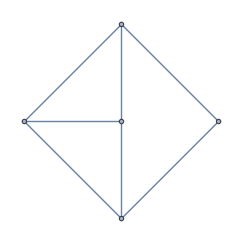
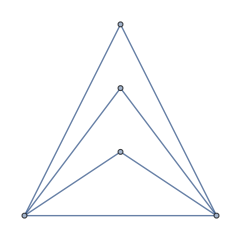
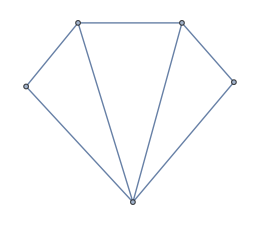

### (A1, A2)

#### setup

We  introduce  a  new  set  of  SL2  generators, which  are  symmetric. The indices are assumed to be up 
Correspondingly,  has raised indices as fundamental indices. 
We will use μ, ν for adjoint indices

```mathematica
ClearAll[s3]
```

```mathematica
s3[1] = LeviCivitaTensor[2].PauliMatrix[1];
s3[2] = LeviCivitaTensor[2].PauliMatrix[2];
s3[3] = LeviCivitaTensor[2].PauliMatrix[3];
```

```mathematica
ClearAll[gaugeindex,flavorindex,gaugeRepindex]
Nf=1;
gaugeindex = Range[1,3,1];
gaugeRepindex = Range[1,2,1];
flavorindex = Range[1,2Nf,1];
gaugeindexu = Range[1,1,1];
flavorindexu = Range[1,2,1];
adjflavorindex = Range[1,1,1];
```

```mathematica
ClearAll[Qaction,Q0action,Q1action,Q2action,ℐ,t3]
(*fundamental matter*)
t3[1] = PauliMatrix[1] ;t3[2] = PauliMatrix[2] ;t3[3] =PauliMatrix[3];
ℐ =(1/2 c2 Sum[ϵ3[[i,j,k]] b[i]**c[j]**c[k],{i,gaugeindex},{j,gaugeindex},{k,gaugeindex}](*gauge term*)
+
I/2(-c2)  Sum[t3[i][[j,k]] β[f][j]**c[i]**γ[f][k],{f,2},{i,gaugeindex},{j,gaugeRepindex},{k,gaugeRepindex}](*gauge matter coupling*)
+c2 Sum[ϵ3[[i,j,k]] c[i]**ψ[f][j]**Φ[f][k],{i,gaugeindex},{j,gaugeindex},{k,gaugeindex},{f,adjflavorindex}](*gauge matter coupling*)
+c3 Sum[s3[k][[i,j]]Φ[1][k]**(γ[1][i]**γ[1][j]+u[1][1]**γ[2][i]**γ[2][j]),{i,gaugeRepindex},{j,gaugeRepindex},{k,gaugeindex}](* superpotential*)
+c4 Sum[u[2][1]**Φ[f][k]**Φ[f][k],{f,adjflavorindex}, {k,gaugeindex}] (* decouple Φ^2 *)
);

Q0action[exp_]:=((bracket[ℐ,exp]//wick2//pluginIΓ2)/.{λ[x_][y_]:>0})//GExpand
Q1action[exp_]:=(((bracket[ℐ,ℐ,exp]//wick3//pluginIΓ3)/.{λ[x_][y_]:>0})/2!)//GExpand
Q2action[exp_]:=(((bracket[ℐ,ℐ,ℐ,exp]+bracket[ℐ,ℐ,exp,ℐ]//wick4//pluginIΓ4)/3!)/.{λ[x_][y_]:>0})//GExpand
```

#### checking Q^2

```mathematica
(β[1][1]//Q0action//Q0action)//Simplify
(γ[1][1]//Q0action//Q0action)//Simplify
(β[1][1]**γ[1][1]//Q0action//Q0action)//Simplify
(β[1][1]**γ[2][1]//Q0action//Q0action)//Simplify
(β[1][1]**γ[2][2]//Q0action//Q0action)//Simplify
(b[1]**c[2]//Q0action//Q0action)//Simplify
u[1][1]**d[1,0][βu[1][1]]//Q0action//Q0action
(u[1][1]**d[1,0][b[1]]**Φ[1][1]//Q0action//Q0action)//Simplify
```

0

0

0

«5 more identical outputs»

#### N=2 stress tensor

```mathematica
S1=(-Sum[b[i]**d[1,0][c[i]],{i,gaugeindex}]
+ (-9/20) Sum[γ[1][k]**d[1,0][β[1][k]],{k,gaugeRepindex}]
+(11/20) Sum[β[1][k]**d[1,0][γ[1][k]],{k,gaugeRepindex}]
+ (-3/20) Sum[γ[2][k]**d[1,0][β[2][k]],{k,gaugeRepindex}]
+(17/20) Sum[β[2][k]**d[1,0][γ[2][k]],{k,gaugeRepindex}]
+(-3/5) u[1][1]**d[1,0][βu[1][1]]
+(2/5)   βu[1][1]**d[1,0][u[1][1]]
+(-4/5) u[2][1]**d[1,0][βu[2][1]]
+(1/5)   βu[2][1]**d[1,0][u[2][1]]
+(-1/10) Sum[Φ[f][k]**d[1,0][ψ[f][k]],{f,1},{k, gaugeindex}]
+(9/10) Sum[ψ[f][k]**d[1,0][Φ[f][k]],{f,1},{k, gaugeindex}]
);

S2=(-Sum[b[i]**d[0,1][c[i]],{i,gaugeindex}]
+ (-9/20) Sum[γ[1][k]**d[0,1][β[1][k]],{k,gaugeRepindex}]
+(11/20) Sum[β[1][k]**d[0,1][γ[1][k]],{k,gaugeRepindex}]
+ (-3/20) Sum[γ[2][k]**d[0,1][β[2][k]],{k,gaugeRepindex}]
+(17/20) Sum[β[2][k]**d[0,1][γ[2][k]],{k,gaugeRepindex}]
+(-3/5) u[1][1]**d[0,1][βu[1][1]]
+(2/5)   βu[1][1]**d[0,1][u[1][1]]
+(-4/5) u[2][1]**d[0,1][βu[2][1]]
+(1/5)   βu[2][1]**d[0,1][u[2][1]]
+(-1/10) Sum[Φ[f][k]**d[0,1][ψ[f][k]],{f,1},{k, gaugeindex}]
+(9/10) Sum[ψ[f][k]**d[0,1][Φ[f][k]],{f,1},{k, gaugeindex}]
);
```

```mathematica
S1//Q0action
S1//Q1action
```

0

0

```mathematica
S2//Q0action
S2//Q1action
```

0

0

```mathematica
(((bracket[S1, S1]//wick2//pluginIΓ2)- (d[1,0][S1]+λ[1][1]*((2)S1)))/.{})//GExpand//FullSimplify
(((bracket[S1, S2]//wick2//pluginIΓ2)- (d[1,0][S2]+λ[1][1]*(S2)+λ[1][2]*S1))/.{})//GExpand//FullSimplify
(((bracket[S2, S1]//wick2//pluginIΓ2)- (d[0,1][S1]+λ[1][2]*(S1)+λ[1][1]*S2))/.{})//GExpand//FullSimplify
(((bracket[S2, S2]//wick2//pluginIΓ2)- (d[0,1][S2]+λ[1][2]*((2)S2)))/.{})//GExpand//FullSimplify
```

0

0

0

«1 more identical outputs»

#### Additional N=2 superconformal symmetries

```mathematica
J=
((-1/5)Sum[ψ[f][k]**Φ[f][k],{f,adjflavorindex},{k,gaugeindex}]
+(1/10)Sum[β[1][j]**γ[1][j],{j,gaugeRepindex}]
+(7/10)Sum[β[2][j]**γ[2][j],{j,gaugeRepindex}]
+(-6/5)βu[1][1]**u[1][1]
+(2/5)βu[2][1]**u[2][1]);
```

```mathematica
J//Q0action//Simplify
J//Q1action//Simplify
```

0

0

```mathematica
G1 =(c5 βu[1][1]**Sum[d[1,0][c[μ]]**Φ[1][μ],{μ,gaugeindex}] 
+c11 Sum[2s3[μ][[a,c]]t3[ν][[c,b]]d[1,0][γ[2][a]] **γ[2][b]**Φ[1][μ]**Φ[1][ν]
+ s3[μ][[a,c]]t3[ν][[c,b]]γ[2][a] **γ[2][b]**d[1,0][Φ[1][μ]]**Φ[1][ν],{μ,gaugeindex},{ν,gaugeindex},{a,gaugeRepindex},{b,gaugeRepindex},{c,gaugeRepindex}]);
G2 =(c5 βu[1][1]**Sum[d[0,1][c[μ]]**Φ[1][μ],{μ,gaugeindex}] 
+c11 Sum[2 s3[μ][[a,c]]t3[ν][[c,b]]d[0,1][γ[2][a]] **γ[2][b]**Φ[1][μ]**Φ[1][ν]
+s3[μ][[a,c]]t3[ν][[c,b]]γ[2][a] **γ[2][b]**d[0,1][Φ[1][μ]]**Φ[1][ν],{μ,gaugeindex},{ν,gaugeindex},{a,gaugeRepindex},{b,gaugeRepindex},{c,gaugeRepindex}]);
```

```mathematica
G1/.{c11->(I c3 c5)/c2}//Q0action//Simplify
G1/.{c11->(I c3 c5)/c2}//Q1action//Simplify
```

0

0

```mathematica
G2/.{c11->(I c3 c5)/c2}//Q0action//Simplify
G2/.{c11->(I c3 c5)/c2}//Q1action//Simplify
```

0

0

```mathematica
Gt=(c6 βu[2][1]**Sum[γ[1][a]**β[2][a],{a,gaugeRepindex}]
+(*(c4 c6)/(2c3)*)c7 Sum[β[1][a]**β[2][b]**Φ[1][μ](LeviCivitaTensor[2].s3[μ].(-LeviCivitaTensor[2]))[[a,b]],{a,gaugeRepindex},{b,gaugeRepindex},{μ,gaugeindex}]
-c6 u[1][1]**βu[2][1]**Sum[β[1][a]**γ[2][a],{a,gaugeRepindex}]
(*+c9 Sum[γ[1][a]**Φ[1][μ]**Φ[1][ν]**Φ[1][ρ]**β[1][b](s3[μ].t3[ν].t3[ρ].(-LeviCivitaTensor[2]))[[a,b]],{a,gaugeRepindex},{b,gaugeRepindex},{μ,gaugeindex},{ν,gaugeindex},{ρ,gaugeindex}]
+c10 Sum[γ[2][a]**Φ[1][μ]**Φ[1][ν]**Φ[1][ρ]**β[2][b](s3[μ].t3[ν].t3[ρ].(-LeviCivitaTensor[2]))[[a,b]],{a,gaugeRepindex},{b,gaugeRepindex},{μ,gaugeindex},{ν,gaugeindex},{ρ,gaugeindex}]*));
```

```mathematica
(Gt//Q0action)+(Gt//Q1action)//.{c7->(c4 c6)/(2c3),c8->-c6}//Simplify
```

0

```mathematica
(Gt//Q0action)//.{c7->(c4 c6)/(2c3),c8->-c6}//Simplify
```

0

```mathematica
(*Gt//Q2action/.{}//Simplify*)
```

```mathematica
(bracket[S1, J]//wick2//pluginIΓ2)== (d[1,0][J]+λ[1][1]*J)//GExpand
```

True

```mathematica
(bracket[S2, J]//wick2//pluginIΓ2)==(d[0,1][J]+λ[1][2]*J)//GExpand
```

True

```mathematica
(((bracket[S1, G1]//wick2//pluginIΓ2)- (d[1,0][G1]+λ[1][1]*((3/2)G1)))/.{c2->1})//GExpand//FullSimplify (* here and below c2->1 is not really necessary it is just to help the machine *)
```

0

```mathematica
(((bracket[S1, G1]//wick2//pluginIΓ2)== (d[1,0][G1]+λ[1][1]*((3/2)G1)))/.{c2->1})//GExpand//FullSimplify
(((bracket[S2, G1]//wick2//pluginIΓ2)==(d[0,1][G1]+λ[1][2]*((1/2)G1)+λ[1][1]*G2))/.{c2->1})//GExpand//FullSimplify
```

True

True

```mathematica
(((bracket[S1, G2]//wick2//pluginIΓ2)==(d[1,0][G2]+λ[1][1]*((1/2)G2)+λ[1][2]*G1))/.{c2->1})//GExpand//FullSimplify
(((bracket[S2, G2]//wick2//pluginIΓ2)==(d[0,1][G2]+λ[1][2]*((3/2)G2)))/.{c2->1})//GExpand//FullSimplify
```

True

True

```mathematica
(bracket[J, G1]//wick2//pluginIΓ2)==G1//GExpand
(bracket[J, G2]//wick2//pluginIΓ2)==G2//GExpand
```

True

True

```mathematica
(bracket[S1, Gt]//wick2//pluginIΓ2)-(d[1,0][Gt]+λ[1][1]*(3/2 Gt))(*/.{c7->(c4 c6)/(2c3),c8->-c6,c9->0,c10->0}*)//GExpand//FullSimplify
(bracket[S2, Gt]//wick2//pluginIΓ2)-(d[0,1][Gt]+λ[1][2]*(3/2 Gt))(*/.{c7->(c4 c6)/(2c3),c8->-c6,c9->0,c10->0}*)//GExpand//FullSimplify
```

0

0

```mathematica
(bracket[J,Gt]//wick2//pluginIΓ2)+c10 hb (bracket[ℐ,J,Gt]//wick3//pluginIΓ3)-(-1) Gt//GExpand//Simplify
```

0

```mathematica
crap=%222;
```

```mathematica
(((bracket[G1, Gt]//wick2//pluginIΓ2)+c17(bracket[ℐ,S1, Gt]//wick3//pluginIΓ3)/.{λ[2][y_]:>c14 λ[1][y]}+c18(bracket[ℐ,ℐ,S1, Gt]//wick4//pluginIΓ4)/.{λ[2][y_]:>c15 λ[1][y],λ[3][y_]:>c16 λ[1][y]})-(c11 S1-1/2 c11 d[1,0][J]+c13 λ[1][1]J))/.{c2->1,c7->(c4 c6)/(2c3),c8->-c6,c9->0,c10->0}//GExpand//FullSimplify
```

-1/(10 c3)(-10 c11 c3 b[1]**d[1,0][c[1]]-10 c11 c3 b[2]**d[1,0][c[2]]-10 c11 c3 b[3]**d[1,0][c[3]]+10 c11 c3 d[1,0][u[1][1]]**βu[1][1]-5 c11 c3 d[1,0][β[1][1]]**γ[1][1]-5 c11 c3 d[1,0][β[1][2]]**γ[1][2]-5 c11 c3 d[1,0][β[2][1]]**γ[2][1]-5 c11 c3 d[1,0][β[2][2]]**γ[2][2]-10 c11 c3 d[1,0][βu[2][1]]**u[2][1]+5 c11 c3 d[1,0][γ[1][1]]**β[1][1]+5 c11 c3 d[1,0][γ[1][2]]**β[1][2]+5 c11 c3 d[1,0][γ[2][1]]**β[2][1]+5 c11 c3 d[1,0][γ[2][2]]**β[2][2]+10 c11 c3 d[1,0][Φ[1][1]]**ψ[1][1]+10 c11 c3 d[1,0][Φ[1][2]]**ψ[1][2]+10 c11 c3 d[1,0][Φ[1][3]]**ψ[1][3]-10 c3 c5 c6 d[1,0][c[1]]**β[1][1]**βu[2][1]**γ[2][1]**Φ[1][1]-10 c3 c5 c6 d[1,0][c[1]]**β[1][2]**βu[2][1]**γ[2][2]**Φ[1][1]-10 c3 c5 c6 d[1,0][c[2]]**β[1][1]**βu[2][1]**γ[2][1]**Φ[1][2]-10 c3 c5 c6 d[1,0][c[2]]**β[1][2]**βu[2][1]**γ[2][2]**Φ[1][2]-10 c3 c5 c6 d[1,0][c[3]]**β[1][1]**βu[2][1]**γ[2][1]**Φ[1][3]-10 c3 c5 c6 d[1,0][c[3]]**β[1][2]**βu[2][1]**γ[2][2]**Φ[1][3]+20 c11 c4 c6 d[1,0][γ[2][1]]**β[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][3]+20 c11 c4 c6 d[1,0][γ[2][1]]**β[1][1]**Φ[1][2]**Φ[1][2]**Φ[1][3]+20 c11 c4 c6 d[1,0][γ[2][1]]**β[1][1]**Φ[1][3]**Φ[1][3]**Φ[1][3]+20 c11 c4 c6 d[1,0][γ[2][1]]**β[1][2]**Φ[1][1]**Φ[1][1]**Φ[1][1]+20 ⅈ c11 c4 c6 d[1,0][γ[2][1]]**β[1][2]**Φ[1][1]**Φ[1][1]**Φ[1][2]+20 c11 c4 c6 d[1,0][γ[2][1]]**β[1][2]**Φ[1][1]**Φ[1][2]**Φ[1][2]+20 c11 c4 c6 d[1,0][γ[2][1]]**β[1][2]**Φ[1][1]**Φ[1][3]**Φ[1][3]+20 ⅈ c11 c4 c6 d[1,0][γ[2][1]]**β[1][2]**Φ[1][2]**Φ[1][2]**Φ[1][2]+20 ⅈ c11 c4 c6 d[1,0][γ[2][1]]**β[1][2]**Φ[1][2]**Φ[1][3]**Φ[1][3]+40 c11 c3 c6 d[1,0][γ[2][1]]**βu[2][1]**γ[1][2]**Φ[1][1]**Φ[1][1]+40 c11 c3 c6 d[1,0][γ[2][1]]**βu[2][1]**γ[1][2]**Φ[1][2]**Φ[1][2]+40 c11 c3 c6 d[1,0][γ[2][1]]**βu[2][1]**γ[1][2]**Φ[1][3]**Φ[1][3]+20 c11 c4 c6 d[1,0][γ[2][2]]**β[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][1]-20 ⅈ c11 c4 c6 d[1,0][γ[2][2]]**β[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][2]+20 c11 c4 c6 d[1,0][γ[2][2]]**β[1][1]**Φ[1][1]**Φ[1][2]**Φ[1][2]+20 c11 c4 c6 d[1,0][γ[2][2]]**β[1][1]**Φ[1][1]**Φ[1][3]**Φ[1][3]-20 ⅈ c11 c4 c6 d[1,0][γ[2][2]]**β[1][1]**Φ[1][2]**Φ[1][2]**Φ[1][2]-20 ⅈ c11 c4 c6 d[1,0][γ[2][2]]**β[1][1]**Φ[1][2]**Φ[1][3]**Φ[1][3]-20 c11 c4 c6 d[1,0][γ[2][2]]**β[1][2]**Φ[1][1]**Φ[1][1]**Φ[1][3]-20 c11 c4 c6 d[1,0][γ[2][2]]**β[1][2]**Φ[1][2]**Φ[1][2]**Φ[1][3]-20 c11 c4 c6 d[1,0][γ[2][2]]**β[1][2]**Φ[1][3]**Φ[1][3]**Φ[1][3]-40 c11 c3 c6 d[1,0][γ[2][2]]**βu[2][1]**γ[1][1]**Φ[1][1]**Φ[1][1]-40 c11 c3 c6 d[1,0][γ[2][2]]**βu[2][1]**γ[1][1]**Φ[1][2]**Φ[1][2]-40 c11 c3 c6 d[1,0][γ[2][2]]**βu[2][1]**γ[1][1]**Φ[1][3]**Φ[1][3]+10 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][1]**γ[2][1]**Φ[1][1]**Φ[1][3]+20 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]-10 ⅈ c11 c4 c6 d[1,0][Φ[1][1]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][2]+10 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2]+10 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][1]**γ[2][2]**Φ[1][3]**Φ[1][3]+20 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]+10 ⅈ c11 c4 c6 d[1,0][Φ[1][1]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][2]+10 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2]+10 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][2]**γ[2][1]**Φ[1][3]**Φ[1][3]-10 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][2]**γ[2][2]**Φ[1][1]**Φ[1][3]+20 c11 c3 c6 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][1]**γ[2][1]**Φ[1][3]-40 c11 c3 c6 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][1]-20 ⅈ c11 c3 c6 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][2]+40 c11 c3 c6 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][1]-20 ⅈ c11 c3 c6 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][2]+20 c11 c3 c6 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][2]**γ[2][2]**Φ[1][3]+10 c11 c4 c6 d[1,0][Φ[1][2]]**β[1][1]**γ[2][1]**Φ[1][2]**Φ[1][3]-10 ⅈ c11 c4 c6 d[1,0][Φ[1][2]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]+10 c11 c4 c6 d[1,0][Φ[1][2]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][2]-20 ⅈ c11 c4 c6 d[1,0][Φ[1][2]]**β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2]-10 ⅈ c11 c4 c6 d[1,0][Φ[1][2]]**β[1][1]**γ[2][2]**Φ[1][3]**Φ[1][3]+10 ⅈ c11 c4 c6 d[1,0][Φ[1][2]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]+10 c11 c4 c6 d[1,0][Φ[1][2]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][2]+20 ⅈ c11 c4 c6 d[1,0][Φ[1][2]]**β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2]+10 ⅈ c11 c4 c6 d[1,0][Φ[1][2]]**β[1][2]**γ[2][1]**Φ[1][3]**Φ[1][3]-10 c11 c4 c6 d[1,0][Φ[1][2]]**β[1][2]**γ[2][2]**Φ[1][2]**Φ[1][3]+20 ⅈ c11 c3 c6 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][1]**γ[2][1]**Φ[1][3]+20 ⅈ c11 c3 c6 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][1]-40 c11 c3 c6 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][2]+20 ⅈ c11 c3 c6 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][1]+40 c11 c3 c6 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][2]-20 ⅈ c11 c3 c6 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][2]**γ[2][2]**Φ[1][3]+10 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][1]**γ[2][1]**Φ[1][1]**Φ[1][1]+10 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][1]**γ[2][1]**Φ[1][2]**Φ[1][2]+20 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][1]**γ[2][1]**Φ[1][3]**Φ[1][3]+10 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][3]-10 ⅈ c11 c4 c6 d[1,0][Φ[1][3]]**β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][3]+10 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][3]+10 ⅈ c11 c4 c6 d[1,0][Φ[1][3]]**β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][3]-10 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][2]**γ[2][2]**Φ[1][1]**Φ[1][1]-10 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][2]**γ[2][2]**Φ[1][2]**Φ[1][2]-20 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][2]**γ[2][2]**Φ[1][3]**Φ[1][3]-20 c11 c3 c6 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][1]**γ[2][1]**Φ[1][1]-20 ⅈ c11 c3 c6 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][1]**γ[2][1]**Φ[1][2]-40 c11 c3 c6 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][3]+40 c11 c3 c6 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][3]-20 c11 c3 c6 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][2]**γ[2][2]**Φ[1][1]+20 ⅈ c11 c3 c6 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][2]**γ[2][2]**Φ[1][2]+(10 c11 c4 c6 (β[1][1]**γ[2][1]**Φ[1][1]**Φ[1][1]**Φ[1][3]+β[1][1]**γ[2][1]**Φ[1][2]**Φ[1][2]**Φ[1][3]+β[1][1]**γ[2][1]**Φ[1][3]**Φ[1][3]**Φ[1][3]+β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]**Φ[1][1]-ⅈ β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]**Φ[1][2]+β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][2]**Φ[1][2]+β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][3]**Φ[1][3]-ⅈ β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2]**Φ[1][2]-ⅈ β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][3]**Φ[1][3]+β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]**Φ[1][1]+ⅈ β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]**Φ[1][2]+β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][2]**Φ[1][2]+β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][3]**Φ[1][3]+ⅈ (β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2]**Φ[1][2]+β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][3]**Φ[1][3]+ⅈ (β[1][2]**γ[2][2]**Φ[1][1]**Φ[1][1]**Φ[1][3]+β[1][2]**γ[2][2]**Φ[1][2]**Φ[1][2]**Φ[1][3]+β[1][2]**γ[2][2]**Φ[1][3]**Φ[1][3]**Φ[1][3])))+c3 (c13 (-12 u[1][1]**βu[1][1]+4 u[2][1]**βu[2][1]+β[1][1]**γ[1][1]+β[1][2]**γ[1][2]+7 β[2][1]**γ[2][1]+7 β[2][2]**γ[2][2]-2 (Φ[1][1]**ψ[1][1]+Φ[1][2]**ψ[1][2]+Φ[1][3]**ψ[1][3]))+20 c11 c6 (-βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]-βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2]-βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][3]**Φ[1][3]+βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]+βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2]+βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][3]**Φ[1][3]))) λ[1][1])

```mathematica
Coefficient[crap,λ[1][1]]//FullSimplify
```

0

```mathematica
(((bracket[G1, Gt]//wick2//pluginIΓ2)-(c11 S1+c12 d[1,0][J]+c13 λ[1][1]J))/.{c2->1,c7->(c4 c6)/(2c3),c8->-c6,c9->0,c10->0})//GExpand//FullSimplify
```

-1/(20 c3)(-20 c11 c3 b[1]**d[1,0][c[1]]-20 c11 c3 b[2]**d[1,0][c[2]]-20 c11 c3 b[3]**d[1,0][c[3]]+8 c11 c3 d[1,0][u[1][1]]**βu[1][1]-24 c12 c3 d[1,0][u[1][1]]**βu[1][1]+4 c11 c3 d[1,0][u[2][1]]**βu[2][1]+8 c12 c3 d[1,0][u[2][1]]**βu[2][1]-9 c11 c3 d[1,0][β[1][1]]**γ[1][1]+2 c12 c3 d[1,0][β[1][1]]**γ[1][1]-9 c11 c3 d[1,0][β[1][2]]**γ[1][2]+2 c12 c3 d[1,0][β[1][2]]**γ[1][2]-3 c11 c3 d[1,0][β[2][1]]**γ[2][1]+14 c12 c3 d[1,0][β[2][1]]**γ[2][1]-3 c11 c3 d[1,0][β[2][2]]**γ[2][2]+14 c12 c3 d[1,0][β[2][2]]**γ[2][2]-12 c11 c3 d[1,0][βu[1][1]]**u[1][1]-24 c12 c3 d[1,0][βu[1][1]]**u[1][1]-16 c11 c3 d[1,0][βu[2][1]]**u[2][1]+8 c12 c3 d[1,0][βu[2][1]]**u[2][1]+11 c11 c3 d[1,0][γ[1][1]]**β[1][1]+2 c12 c3 d[1,0][γ[1][1]]**β[1][1]+11 c11 c3 d[1,0][γ[1][2]]**β[1][2]+2 c12 c3 d[1,0][γ[1][2]]**β[1][2]+17 c11 c3 d[1,0][γ[2][1]]**β[2][1]+14 c12 c3 d[1,0][γ[2][1]]**β[2][1]+17 c11 c3 d[1,0][γ[2][2]]**β[2][2]+14 c12 c3 d[1,0][γ[2][2]]**β[2][2]+18 c11 c3 d[1,0][Φ[1][1]]**ψ[1][1]-4 c12 c3 d[1,0][Φ[1][1]]**ψ[1][1]+18 c11 c3 d[1,0][Φ[1][2]]**ψ[1][2]-4 c12 c3 d[1,0][Φ[1][2]]**ψ[1][2]+18 c11 c3 d[1,0][Φ[1][3]]**ψ[1][3]-4 c12 c3 d[1,0][Φ[1][3]]**ψ[1][3]-2 c11 c3 d[1,0][ψ[1][1]]**Φ[1][1]-4 c12 c3 d[1,0][ψ[1][1]]**Φ[1][1]-2 c11 c3 d[1,0][ψ[1][2]]**Φ[1][2]-4 c12 c3 d[1,0][ψ[1][2]]**Φ[1][2]-2 c11 c3 d[1,0][ψ[1][3]]**Φ[1][3]-4 c12 c3 d[1,0][ψ[1][3]]**Φ[1][3]-20 c3 c5 c6 d[1,0][c[1]]**β[1][1]**βu[2][1]**γ[2][1]**Φ[1][1]-20 c3 c5 c6 d[1,0][c[1]]**β[1][2]**βu[2][1]**γ[2][2]**Φ[1][1]-20 c3 c5 c6 d[1,0][c[2]]**β[1][1]**βu[2][1]**γ[2][1]**Φ[1][2]-20 c3 c5 c6 d[1,0][c[2]]**β[1][2]**βu[2][1]**γ[2][2]**Φ[1][2]-20 c3 c5 c6 d[1,0][c[3]]**β[1][1]**βu[2][1]**γ[2][1]**Φ[1][3]-20 c3 c5 c6 d[1,0][c[3]]**β[1][2]**βu[2][1]**γ[2][2]**Φ[1][3]+40 c11 c4 c6 d[1,0][γ[2][1]]**β[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][3]+40 c11 c4 c6 d[1,0][γ[2][1]]**β[1][1]**Φ[1][2]**Φ[1][2]**Φ[1][3]+40 c11 c4 c6 d[1,0][γ[2][1]]**β[1][1]**Φ[1][3]**Φ[1][3]**Φ[1][3]+40 c11 c4 c6 d[1,0][γ[2][1]]**β[1][2]**Φ[1][1]**Φ[1][1]**Φ[1][1]+40 ⅈ c11 c4 c6 d[1,0][γ[2][1]]**β[1][2]**Φ[1][1]**Φ[1][1]**Φ[1][2]+40 c11 c4 c6 d[1,0][γ[2][1]]**β[1][2]**Φ[1][1]**Φ[1][2]**Φ[1][2]+40 c11 c4 c6 d[1,0][γ[2][1]]**β[1][2]**Φ[1][1]**Φ[1][3]**Φ[1][3]+40 ⅈ c11 c4 c6 d[1,0][γ[2][1]]**β[1][2]**Φ[1][2]**Φ[1][2]**Φ[1][2]+40 ⅈ c11 c4 c6 d[1,0][γ[2][1]]**β[1][2]**Φ[1][2]**Φ[1][3]**Φ[1][3]+80 c11 c3 c6 d[1,0][γ[2][1]]**βu[2][1]**γ[1][2]**Φ[1][1]**Φ[1][1]+80 c11 c3 c6 d[1,0][γ[2][1]]**βu[2][1]**γ[1][2]**Φ[1][2]**Φ[1][2]+80 c11 c3 c6 d[1,0][γ[2][1]]**βu[2][1]**γ[1][2]**Φ[1][3]**Φ[1][3]+40 c11 c4 c6 d[1,0][γ[2][2]]**β[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][1]-40 ⅈ c11 c4 c6 d[1,0][γ[2][2]]**β[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][2]+40 c11 c4 c6 d[1,0][γ[2][2]]**β[1][1]**Φ[1][1]**Φ[1][2]**Φ[1][2]+40 c11 c4 c6 d[1,0][γ[2][2]]**β[1][1]**Φ[1][1]**Φ[1][3]**Φ[1][3]-40 ⅈ c11 c4 c6 d[1,0][γ[2][2]]**β[1][1]**Φ[1][2]**Φ[1][2]**Φ[1][2]-40 ⅈ c11 c4 c6 d[1,0][γ[2][2]]**β[1][1]**Φ[1][2]**Φ[1][3]**Φ[1][3]-40 c11 c4 c6 d[1,0][γ[2][2]]**β[1][2]**Φ[1][1]**Φ[1][1]**Φ[1][3]-40 c11 c4 c6 d[1,0][γ[2][2]]**β[1][2]**Φ[1][2]**Φ[1][2]**Φ[1][3]-40 c11 c4 c6 d[1,0][γ[2][2]]**β[1][2]**Φ[1][3]**Φ[1][3]**Φ[1][3]-80 c11 c3 c6 d[1,0][γ[2][2]]**βu[2][1]**γ[1][1]**Φ[1][1]**Φ[1][1]-80 c11 c3 c6 d[1,0][γ[2][2]]**βu[2][1]**γ[1][1]**Φ[1][2]**Φ[1][2]-80 c11 c3 c6 d[1,0][γ[2][2]]**βu[2][1]**γ[1][1]**Φ[1][3]**Φ[1][3]+20 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][1]**γ[2][1]**Φ[1][1]**Φ[1][3]+40 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]-20 ⅈ c11 c4 c6 d[1,0][Φ[1][1]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][2]+20 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2]+20 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][1]**γ[2][2]**Φ[1][3]**Φ[1][3]+40 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]+20 ⅈ c11 c4 c6 d[1,0][Φ[1][1]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][2]+20 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2]+20 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][2]**γ[2][1]**Φ[1][3]**Φ[1][3]-20 c11 c4 c6 d[1,0][Φ[1][1]]**β[1][2]**γ[2][2]**Φ[1][1]**Φ[1][3]+40 c11 c3 c6 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][1]**γ[2][1]**Φ[1][3]-80 c11 c3 c6 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][1]-40 ⅈ c11 c3 c6 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][2]+80 c11 c3 c6 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][1]-40 ⅈ c11 c3 c6 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][2]+40 c11 c3 c6 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][2]**γ[2][2]**Φ[1][3]+20 c11 c4 c6 d[1,0][Φ[1][2]]**β[1][1]**γ[2][1]**Φ[1][2]**Φ[1][3]-20 ⅈ c11 c4 c6 d[1,0][Φ[1][2]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]+20 c11 c4 c6 d[1,0][Φ[1][2]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][2]-40 ⅈ c11 c4 c6 d[1,0][Φ[1][2]]**β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2]-20 ⅈ c11 c4 c6 d[1,0][Φ[1][2]]**β[1][1]**γ[2][2]**Φ[1][3]**Φ[1][3]+20 ⅈ c11 c4 c6 d[1,0][Φ[1][2]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]+20 c11 c4 c6 d[1,0][Φ[1][2]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][2]+40 ⅈ c11 c4 c6 d[1,0][Φ[1][2]]**β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2]+20 ⅈ c11 c4 c6 d[1,0][Φ[1][2]]**β[1][2]**γ[2][1]**Φ[1][3]**Φ[1][3]-20 c11 c4 c6 d[1,0][Φ[1][2]]**β[1][2]**γ[2][2]**Φ[1][2]**Φ[1][3]+40 ⅈ c11 c3 c6 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][1]**γ[2][1]**Φ[1][3]+40 ⅈ c11 c3 c6 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][1]-80 c11 c3 c6 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][2]+40 ⅈ c11 c3 c6 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][1]+80 c11 c3 c6 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][2]-40 ⅈ c11 c3 c6 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][2]**γ[2][2]**Φ[1][3]+20 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][1]**γ[2][1]**Φ[1][1]**Φ[1][1]+20 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][1]**γ[2][1]**Φ[1][2]**Φ[1][2]+40 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][1]**γ[2][1]**Φ[1][3]**Φ[1][3]+20 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][3]-20 ⅈ c11 c4 c6 d[1,0][Φ[1][3]]**β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][3]+20 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][3]+20 ⅈ c11 c4 c6 d[1,0][Φ[1][3]]**β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][3]-20 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][2]**γ[2][2]**Φ[1][1]**Φ[1][1]-20 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][2]**γ[2][2]**Φ[1][2]**Φ[1][2]-40 c11 c4 c6 d[1,0][Φ[1][3]]**β[1][2]**γ[2][2]**Φ[1][3]**Φ[1][3]-40 c11 c3 c6 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][1]**γ[2][1]**Φ[1][1]-40 ⅈ c11 c3 c6 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][1]**γ[2][1]**Φ[1][2]-80 c11 c3 c6 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][3]+80 c11 c3 c6 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][3]-40 c11 c3 c6 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][2]**γ[2][2]**Φ[1][1]+40 ⅈ c11 c3 c6 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][2]**γ[2][2]**Φ[1][2]+2 (10 c11 c4 c6 (β[1][1]**γ[2][1]**Φ[1][1]**Φ[1][1]**Φ[1][3]+β[1][1]**γ[2][1]**Φ[1][2]**Φ[1][2]**Φ[1][3]+β[1][1]**γ[2][1]**Φ[1][3]**Φ[1][3]**Φ[1][3]+β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]**Φ[1][1]-ⅈ β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]**Φ[1][2]+β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][2]**Φ[1][2]+β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][3]**Φ[1][3]-ⅈ β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2]**Φ[1][2]-ⅈ β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][3]**Φ[1][3]+β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]**Φ[1][1]+ⅈ β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]**Φ[1][2]+β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][2]**Φ[1][2]+β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][3]**Φ[1][3]+ⅈ (β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2]**Φ[1][2]+β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][3]**Φ[1][3]+ⅈ (β[1][2]**γ[2][2]**Φ[1][1]**Φ[1][1]**Φ[1][3]+β[1][2]**γ[2][2]**Φ[1][2]**Φ[1][2]**Φ[1][3]+β[1][2]**γ[2][2]**Φ[1][3]**Φ[1][3]**Φ[1][3])))+c3 (c13 (-12 u[1][1]**βu[1][1]+4 u[2][1]**βu[2][1]+β[1][1]**γ[1][1]+β[1][2]**γ[1][2]+7 β[2][1]**γ[2][1]+7 β[2][2]**γ[2][2]-2 (Φ[1][1]**ψ[1][1]+Φ[1][2]**ψ[1][2]+Φ[1][3]**ψ[1][3]))+20 c11 c6 (-βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]-βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2]-βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][3]**Φ[1][3]+βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]+βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2]+βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][3]**Φ[1][3]))) λ[1][1])

```mathematica
(((bracket[G1, Gt]//wick2//pluginIΓ2)+((bracket[ℐ,S1, Gt]//wick3//pluginIΓ3)/.{λ[2][y_]:>λ[1][y]})-(d[1,0][Gt]+λ[1][1]*(3/2 Gt)))/.{c7->(c4 c6)/(2c3),c8->-c6,c9->0,c10->0})//GExpand//FullSimplify
```

1/(4 c3)c6 (2 c4 d[1,0][β[1][1]]**β[2][1]**Φ[1][1]-2 ⅈ c4 d[1,0][β[1][1]]**β[2][1]**Φ[1][2]-2 c4 d[1,0][β[1][1]]**β[2][2]**Φ[1][3]-2 c4 d[1,0][β[1][2]]**β[2][1]**Φ[1][3]-2 c4 d[1,0][β[1][2]]**β[2][2]**Φ[1][1]-2 ⅈ c4 d[1,0][β[1][2]]**β[2][2]**Φ[1][2]-2 c4 d[1,0][β[2][1]]**β[1][1]**Φ[1][1]+2 ⅈ c4 d[1,0][β[2][1]]**β[1][1]**Φ[1][2]+2 c4 d[1,0][β[2][1]]**β[1][2]**Φ[1][3]+2 c4 d[1,0][β[2][2]]**β[1][1]**Φ[1][3]+2 c4 d[1,0][β[2][2]]**β[1][2]**Φ[1][1]+2 ⅈ c4 d[1,0][β[2][2]]**β[1][2]**Φ[1][2]+2 c4 d[1,0][Φ[1][1]]**β[1][1]**β[2][1]-2 c4 d[1,0][Φ[1][1]]**β[1][2]**β[2][2]-2 ⅈ c4 d[1,0][Φ[1][2]]**β[1][1]**β[2][1]-2 ⅈ c4 d[1,0][Φ[1][2]]**β[1][2]**β[2][2]-2 c4 d[1,0][Φ[1][3]]**β[1][1]**β[2][2]-2 c4 d[1,0][Φ[1][3]]**β[1][2]**β[2][1]+4 c3 (d[1,0][β[2][1]]**βu[2][1]**γ[1][1]+d[1,0][β[2][2]]**βu[2][1]**γ[1][2]-d[1,0][βu[2][1]]**β[2][1]**γ[1][1]-d[1,0][βu[2][1]]**β[2][2]**γ[1][2]+d[1,0][γ[1][1]]**β[2][1]**βu[2][1]+d[1,0][γ[1][2]]**β[2][2]**βu[2][1]-d[1,0][u[1][1]]**β[1][1]**βu[2][1]**γ[2][1]-d[1,0][u[1][1]]**β[1][2]**βu[2][1]**γ[2][2]-d[1,0][β[1][1]]**u[1][1]**βu[2][1]**γ[2][1]-d[1,0][β[1][2]]**u[1][1]**βu[2][1]**γ[2][2]+d[1,0][βu[2][1]]**u[1][1]**β[1][1]**γ[2][1]+d[1,0][βu[2][1]]**u[1][1]**β[1][2]**γ[2][2]-d[1,0][γ[2][1]]**u[1][1]**β[1][1]**βu[2][1]-d[1,0][γ[2][2]]**u[1][1]**β[1][2]**βu[2][1]+c5 (d[1,0][c[1]]**β[1][1]**βu[2][1]**γ[2][1]**Φ[1][1]+d[1,0][c[1]]**β[1][2]**βu[2][1]**γ[2][2]**Φ[1][1]+d[1,0][c[2]]**β[1][1]**βu[2][1]**γ[2][1]**Φ[1][2]+d[1,0][c[2]]**β[1][2]**βu[2][1]**γ[2][2]**Φ[1][2]+d[1,0][c[3]]**β[1][1]**βu[2][1]**γ[2][1]**Φ[1][3]+d[1,0][c[3]]**β[1][2]**βu[2][1]**γ[2][2]**Φ[1][3]))-8 c11 c4 d[1,0][γ[2][1]]**β[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][3]-8 c11 c4 d[1,0][γ[2][1]]**β[1][1]**Φ[1][2]**Φ[1][2]**Φ[1][3]-8 c11 c4 d[1,0][γ[2][1]]**β[1][1]**Φ[1][3]**Φ[1][3]**Φ[1][3]-8 c11 c4 d[1,0][γ[2][1]]**β[1][2]**Φ[1][1]**Φ[1][1]**Φ[1][1]-8 ⅈ c11 c4 d[1,0][γ[2][1]]**β[1][2]**Φ[1][1]**Φ[1][1]**Φ[1][2]-8 c11 c4 d[1,0][γ[2][1]]**β[1][2]**Φ[1][1]**Φ[1][2]**Φ[1][2]-8 c11 c4 d[1,0][γ[2][1]]**β[1][2]**Φ[1][1]**Φ[1][3]**Φ[1][3]-8 ⅈ c11 c4 d[1,0][γ[2][1]]**β[1][2]**Φ[1][2]**Φ[1][2]**Φ[1][2]-8 ⅈ c11 c4 d[1,0][γ[2][1]]**β[1][2]**Φ[1][2]**Φ[1][3]**Φ[1][3]-16 c11 c3 d[1,0][γ[2][1]]**βu[2][1]**γ[1][2]**Φ[1][1]**Φ[1][1]-16 c11 c3 d[1,0][γ[2][1]]**βu[2][1]**γ[1][2]**Φ[1][2]**Φ[1][2]-16 c11 c3 d[1,0][γ[2][1]]**βu[2][1]**γ[1][2]**Φ[1][3]**Φ[1][3]-8 c11 c4 d[1,0][γ[2][2]]**β[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][1]+8 ⅈ c11 c4 d[1,0][γ[2][2]]**β[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][2]-8 c11 c4 d[1,0][γ[2][2]]**β[1][1]**Φ[1][1]**Φ[1][2]**Φ[1][2]-8 c11 c4 d[1,0][γ[2][2]]**β[1][1]**Φ[1][1]**Φ[1][3]**Φ[1][3]+8 ⅈ c11 c4 d[1,0][γ[2][2]]**β[1][1]**Φ[1][2]**Φ[1][2]**Φ[1][2]+8 ⅈ c11 c4 d[1,0][γ[2][2]]**β[1][1]**Φ[1][2]**Φ[1][3]**Φ[1][3]+8 c11 c4 d[1,0][γ[2][2]]**β[1][2]**Φ[1][1]**Φ[1][1]**Φ[1][3]+8 c11 c4 d[1,0][γ[2][2]]**β[1][2]**Φ[1][2]**Φ[1][2]**Φ[1][3]+8 c11 c4 d[1,0][γ[2][2]]**β[1][2]**Φ[1][3]**Φ[1][3]**Φ[1][3]+16 c11 c3 d[1,0][γ[2][2]]**βu[2][1]**γ[1][1]**Φ[1][1]**Φ[1][1]+16 c11 c3 d[1,0][γ[2][2]]**βu[2][1]**γ[1][1]**Φ[1][2]**Φ[1][2]+16 c11 c3 d[1,0][γ[2][2]]**βu[2][1]**γ[1][1]**Φ[1][3]**Φ[1][3]-4 c11 c4 d[1,0][Φ[1][1]]**β[1][1]**γ[2][1]**Φ[1][1]**Φ[1][3]-8 c11 c4 d[1,0][Φ[1][1]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]+4 ⅈ c11 c4 d[1,0][Φ[1][1]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][2]-4 c11 c4 d[1,0][Φ[1][1]]**β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2]-4 c11 c4 d[1,0][Φ[1][1]]**β[1][1]**γ[2][2]**Φ[1][3]**Φ[1][3]-8 c11 c4 d[1,0][Φ[1][1]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]-4 ⅈ c11 c4 d[1,0][Φ[1][1]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][2]-4 c11 c4 d[1,0][Φ[1][1]]**β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2]-4 c11 c4 d[1,0][Φ[1][1]]**β[1][2]**γ[2][1]**Φ[1][3]**Φ[1][3]+4 c11 c4 d[1,0][Φ[1][1]]**β[1][2]**γ[2][2]**Φ[1][1]**Φ[1][3]-8 c11 c3 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][1]**γ[2][1]**Φ[1][3]+16 c11 c3 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][1]+8 ⅈ c11 c3 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][2]-16 c11 c3 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][1]+8 ⅈ c11 c3 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][2]-8 c11 c3 d[1,0][Φ[1][1]]**βu[2][1]**γ[1][2]**γ[2][2]**Φ[1][3]-4 c11 c4 d[1,0][Φ[1][2]]**β[1][1]**γ[2][1]**Φ[1][2]**Φ[1][3]+4 ⅈ c11 c4 d[1,0][Φ[1][2]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]-4 c11 c4 d[1,0][Φ[1][2]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][2]+8 ⅈ c11 c4 d[1,0][Φ[1][2]]**β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2]+4 ⅈ c11 c4 d[1,0][Φ[1][2]]**β[1][1]**γ[2][2]**Φ[1][3]**Φ[1][3]-4 ⅈ c11 c4 d[1,0][Φ[1][2]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]-4 c11 c4 d[1,0][Φ[1][2]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][2]-8 ⅈ c11 c4 d[1,0][Φ[1][2]]**β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2]-4 ⅈ c11 c4 d[1,0][Φ[1][2]]**β[1][2]**γ[2][1]**Φ[1][3]**Φ[1][3]+4 c11 c4 d[1,0][Φ[1][2]]**β[1][2]**γ[2][2]**Φ[1][2]**Φ[1][3]-8 ⅈ c11 c3 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][1]**γ[2][1]**Φ[1][3]-8 ⅈ c11 c3 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][1]+16 c11 c3 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][2]-8 ⅈ c11 c3 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][1]-16 c11 c3 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][2]+8 ⅈ c11 c3 d[1,0][Φ[1][2]]**βu[2][1]**γ[1][2]**γ[2][2]**Φ[1][3]-4 c11 c4 d[1,0][Φ[1][3]]**β[1][1]**γ[2][1]**Φ[1][1]**Φ[1][1]-4 c11 c4 d[1,0][Φ[1][3]]**β[1][1]**γ[2][1]**Φ[1][2]**Φ[1][2]-8 c11 c4 d[1,0][Φ[1][3]]**β[1][1]**γ[2][1]**Φ[1][3]**Φ[1][3]-4 c11 c4 d[1,0][Φ[1][3]]**β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][3]+4 ⅈ c11 c4 d[1,0][Φ[1][3]]**β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][3]-4 c11 c4 d[1,0][Φ[1][3]]**β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][3]-4 ⅈ c11 c4 d[1,0][Φ[1][3]]**β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][3]+4 c11 c4 d[1,0][Φ[1][3]]**β[1][2]**γ[2][2]**Φ[1][1]**Φ[1][1]+4 c11 c4 d[1,0][Φ[1][3]]**β[1][2]**γ[2][2]**Φ[1][2]**Φ[1][2]+8 c11 c4 d[1,0][Φ[1][3]]**β[1][2]**γ[2][2]**Φ[1][3]**Φ[1][3]+8 c11 c3 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][1]**γ[2][1]**Φ[1][1]+8 ⅈ c11 c3 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][1]**γ[2][1]**Φ[1][2]+16 c11 c3 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][3]-16 c11 c3 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][3]+8 c11 c3 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][2]**γ[2][2]**Φ[1][1]-8 ⅈ c11 c3 d[1,0][Φ[1][3]]**βu[2][1]**γ[1][2]**γ[2][2]**Φ[1][2]+(3 c4 β[1][1]**β[2][1]**Φ[1][1]-3 ⅈ c4 β[1][1]**β[2][1]**Φ[1][2]-3 c4 β[1][1]**β[2][2]**Φ[1][3]-3 c4 β[1][2]**β[2][1]**Φ[1][3]-3 c4 β[1][2]**β[2][2]**Φ[1][1]-3 ⅈ c4 β[1][2]**β[2][2]**Φ[1][2]+6 c3 (β[2][1]**βu[2][1]**γ[1][1]+β[2][2]**βu[2][1]**γ[1][2]-u[1][1]**β[1][1]**βu[2][1]**γ[2][1]-u[1][1]**β[1][2]**βu[2][1]**γ[2][2])-4 c11 c4 β[1][1]**γ[2][1]**Φ[1][1]**Φ[1][1]**Φ[1][3]-4 c11 c4 β[1][1]**γ[2][1]**Φ[1][2]**Φ[1][2]**Φ[1][3]-4 c11 c4 β[1][1]**γ[2][1]**Φ[1][3]**Φ[1][3]**Φ[1][3]-4 c11 c4 β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]**Φ[1][1]+4 ⅈ c11 c4 β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]**Φ[1][2]-4 c11 c4 β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][2]**Φ[1][2]-4 c11 c4 β[1][1]**γ[2][2]**Φ[1][1]**Φ[1][3]**Φ[1][3]+4 ⅈ c11 c4 β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2]**Φ[1][2]+4 ⅈ c11 c4 β[1][1]**γ[2][2]**Φ[1][2]**Φ[1][3]**Φ[1][3]-4 c11 c4 β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]**Φ[1][1]-4 ⅈ c11 c4 β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]**Φ[1][2]-4 c11 c4 β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][2]**Φ[1][2]-4 c11 c4 β[1][2]**γ[2][1]**Φ[1][1]**Φ[1][3]**Φ[1][3]-4 ⅈ c11 c4 β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2]**Φ[1][2]-4 ⅈ c11 c4 β[1][2]**γ[2][1]**Φ[1][2]**Φ[1][3]**Φ[1][3]+4 c11 c4 β[1][2]**γ[2][2]**Φ[1][1]**Φ[1][1]**Φ[1][3]+4 c11 c4 β[1][2]**γ[2][2]**Φ[1][2]**Φ[1][2]**Φ[1][3]+4 c11 c4 β[1][2]**γ[2][2]**Φ[1][3]**Φ[1][3]**Φ[1][3]+8 c11 c3 βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]+8 c11 c3 βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2]+8 c11 c3 βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][3]**Φ[1][3]-8 c11 c3 βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]-8 c11 c3 βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2]-8 c11 c3 βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][3]**Φ[1][3]) λ[1][1])

```mathematica
(((bracket[S2, Gt]//wick2//pluginIΓ2)+((bracket[ℐ,S2, Gt]//wick3//pluginIΓ3)/.{λ[2][y_]:>λ[1][y]})== (d[0,1][Gt]+λ[1][2]*(7/10 Gt)))/.{c2->1,c6->0,c8->0})//GExpand//FullSimplify
```

c7 (β[1][1]**β[2][1]**Φ[1][1]-ⅈ β[1][1]**β[2][1]**Φ[1][2]-β[1][1]**β[2][2]**Φ[1][3]-β[1][2]**β[2][1]**Φ[1][3]-β[1][2]**β[2][2]**Φ[1][1]-ⅈ β[1][2]**β[2][2]**Φ[1][2]) λ[1][2]==0

#### check charges U(1)J

```mathematica
Table[(bracket[J,Φ[1][k]]//wick2//pluginIΓ2)==-1/5 Φ[1][k],{k,3}]
Table[(bracket[J,ψ[1][k]]//wick2//pluginIΓ2)==1/5 ψ[1][k],{k,3}]
Table[(bracket[J,γ[1][k]]//wick2//pluginIΓ2)==1/10 γ[1][k],{k,2}]
Table[(bracket[J,β[1][k]]//wick2//pluginIΓ2)==-1/10 β[1][k],{k,2}]
(bracket[J,c[1]]//wick2//pluginIΓ2)
(bracket[J,b[1]]//wick2//pluginIΓ2)
```

{True,True,True}

{True,True,True}

{True,True}

{True,True}

0

0

```mathematica
(bracket[J,J]//wick2//pluginIΓ2)
```

0

```mathematica
(bracket[J,G1]//wick2//pluginIΓ2)- G1//GExpand
(bracket[J,G2]//wick2//pluginIΓ2)- G2//GExpand
```

0

0

```mathematica
(bracket[J,Gt]//wick2//pluginIΓ2)==(-1)  Gt//GExpand//Simplify
```

True

#### check charges S

```mathematica
(bracket[S1, J**u[1][1]]//wick2//pluginIΓ2)== (d[1,0][J**u[1][1]]+(1+3/5) λ[1][1]*J**u[1][1])//GExpand//Simplify
(bracket[S1, ψ[1][1]]//wick2//pluginIΓ2)== (d[1,0][ψ[1][1]]+(9/10) λ[1][1]ψ[1][1])//GExpand//Simplify
```

True

True

```mathematica
(bracket[S2, J**u[1][1]]//wick2//pluginIΓ2)== (d[0,1][J**u[1][1]]+(1+3/5) λ[1][2]*J**u[1][1])//GExpand//Simplify
(bracket[S2, ψ[1][1]]//wick2//pluginIΓ2)== (d[0,1][ψ[1][1]]+(9/10) λ[1][2]ψ[1][1])//GExpand//Simplify
```

True

True

```mathematica
(bracket[S1, d[1,0][β[1][1]]]//wick2//pluginIΓ2)== (d[2,0][β[1][1]]+(11/20+1) λ[1][1]d[1,0][β[1][1]]+11/20 β[1][1] (λ[1][1])^2)//GExpand
```

True

```mathematica
(bracket[S1, d[0,1][β[1][1]]]//wick2//pluginIΓ2)- (d[1,1][β[1][1]]+( 11/20) λ[1][1]d[0,1][β[1][1]](*+11/20 β[1][1] (λ[1][1])^2*))//GExpand
```

d[1,0][β[1][1]] λ[1][2]+11/20 β[1][1] λ[1][1] λ[1][2]

```mathematica
(bracket[S1,c[1]]//wick2//pluginIΓ2)==d[1,0][c[1]]//GExpand
(bracket[S1,b[1]]//wick2//pluginIΓ2)==d[1,0][b[1]]+b[1] λ[1][1]//GExpand
```

True

True

```mathematica
(bracket[S2,c[1]]//wick2//pluginIΓ2)==d[0,1][c[1]]//GExpand
(bracket[S2,b[1]]//wick2//pluginIΓ2)==d[0,1][b[1]]+b[1] λ[1][2]//GExpand
```

True

True

```mathematica
(bracket[S2,J]//wick2//pluginIΓ2)==d[0,1][J]+λ[1][2]J//GExpand
```

True

#### three loops (Gt, G1)

```mathematica
wick5tri[exp_]:=exp//wick[#,{1,5}]&//wick[#,{2,5}]&//wick[#,{2,4}]&//wick[#,{3,4}]&//wick[#,{3,5}]&//wick[#,{1,3}]&//wick[#,{4,5}]&
wick5Kite[exp_]:=exp//wick[#,{1,5}]&//wick[#,{2,5}]&//wick[#,{2,3}]&//wick[#,{3,4}]&//wick[#,{1,4}]&//wick[#,{2,4}]&//wick[#,{3,5}]&
```

```mathematica
tic = AbsoluteTime[];
temp = (bracket[ℐ,ℐ,ℐ,G1,Gt]//wick5tri(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]

tic = AbsoluteTime[];
temp//pluginIΓ5//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 7413.4242 seconds

0

spent 0.00011 seconds

```mathematica
tic = AbsoluteTime[];
temp2 = (bracket[ℐ,G1,ℐ,ℐ,Gt]//wick5tri(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]

tic = AbsoluteTime[];
temp2//pluginIΓ5//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 7645.019683 seconds

0

spent 0.000099 seconds

```mathematica
(*1*)
tic = AbsoluteTime[];
temp2 = (bracket[ℐ,ℐ,ℐ,Gt,G1]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 4035.18674 seconds

```mathematica
(*2*)
tic = AbsoluteTime[];
temp2 = (bracket[ℐ,ℐ,G1,ℐ,Gt]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 7813.19528 seconds

```mathematica
(*3*)
tic = AbsoluteTime[];
temp2 = (bracket[ℐ,ℐ,Gt,ℐ,G1]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 4136.531114 seconds

```mathematica
(*6*)
tic = AbsoluteTime[];
temp1 = (bracket[G1, Gt, ℐ,ℐ,ℐ]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 4642.937942 seconds

```mathematica
(*5*)
tic = AbsoluteTime[];
temp1 = (bracket[Gt, G1, ℐ,ℐ,ℐ]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 6576.745837 seconds

```mathematica
(*4*)
tic = AbsoluteTime[];
temp1 = (bracket[ ℐ,Gt, G1,ℐ,ℐ]//wick5Kite(*//pluginIΓ4*))//GExpand
toc = AbsoluteTime[];
Print["spent ", toc-tic, " seconds"]
```

0

spent 4714.10775 seconds

```mathematica
bracket[ ℐ,ℐ,ℐ]//wick3
```

0

```mathematica
bracket[ J,S1,S1]//wick3
```

-1/10 bracket[1,1,1,{1,2,{0,0,{0,0}}},{1,3,{0,0,{0,0}}},{2,3,{1,1,{2,0}}}]-3/10 bracket[1,1,1,{1,2,{0,0,{0,0}}},{1,3,{0,1,{1,0}}},{2,3,{1,0,{1,0}}}]-3/10 bracket[1,1,1,{1,2,{0,1,{1,0}}},{1,3,{0,0,{0,0}}},{2,3,{0,1,{1,0}}}]-1/10 bracket[1,1,1,{1,2,{0,1,{1,0}}},{1,3,{0,1,{1,0}}},{2,3,{0,0,{0,0}}}]

#### flavor symmetry current, HB schur operator

```mathematica
ClearAll[μ0, μp, μm,s3]
```

We  introduce  a  new  set  of  SL2  generators, which  are  symmetric. The indices are assumed to be up 
Correspondingly,  has raised indices as fundamental indices. 
We will use μ, ν for adjoint indices

```mathematica
J0= Sum[β[1][k]**γ[1][k],{k,gaugeRepindex}]-Sum[β[2][k]**γ[2][k],{k,gaugeRepindex}];
Jp= Sum[β[2][k]**γ[1][k],{k,gaugeRepindex}];
Jm= Sum[β[1][k]**γ[2][k],{k,gaugeRepindex}];
```

```mathematica
J0//Q0action
J0//Q1action
```

2 c3 γ[1][1]**γ[1][1]**Φ[1][1]+2 ⅈ c3 γ[1][1]**γ[1][1]**Φ[1][2]-4 c3 γ[1][1]**γ[1][2]**Φ[1][3]-2 c3 γ[1][2]**γ[1][2]**Φ[1][1]+2 ⅈ c3 γ[1][2]**γ[1][2]**Φ[1][2]-2 c3 u[1][1]**γ[2][1]**γ[2][1]**Φ[1][1]-2 ⅈ c3 u[1][1]**γ[2][1]**γ[2][1]**Φ[1][2]+4 c3 u[1][1]**γ[2][1]**γ[2][2]**Φ[1][3]+2 c3 u[1][1]**γ[2][2]**γ[2][2]**Φ[1][1]-2 ⅈ c3 u[1][1]**γ[2][2]**γ[2][2]**Φ[1][2]

0

```mathematica
Jm//Q0action
Jm//Q1action
```

2 c3 γ[1][1]**γ[2][1]**Φ[1][1]+2 ⅈ c3 γ[1][1]**γ[2][1]**Φ[1][2]-2 c3 γ[1][1]**γ[2][2]**Φ[1][3]-2 c3 γ[1][2]**γ[2][1]**Φ[1][3]-2 c3 γ[1][2]**γ[2][2]**Φ[1][1]+2 ⅈ c3 γ[1][2]**γ[2][2]**Φ[1][2]

0

```mathematica
Jp//Q0action
Jp//Q1action
```

2 c3 u[1][1]**γ[1][1]**γ[2][1]**Φ[1][1]+2 ⅈ c3 u[1][1]**γ[1][1]**γ[2][1]**Φ[1][2]-2 c3 u[1][1]**γ[1][1]**γ[2][2]**Φ[1][3]-2 c3 u[1][1]**γ[1][2]**γ[2][1]**Φ[1][3]-2 c3 u[1][1]**γ[1][2]**γ[2][2]**Φ[1][1]+2 ⅈ c3 u[1][1]**γ[1][2]**γ[2][2]**Φ[1][2]

0

```mathematica
μ0=Sum[s3[k][[i,j]]Φ[f][k]**γ[1][i]**γ[2][j],{f,adjflavorindex},{k,gaugeindex},{i,gaugeRepindex},{j,gaugeRepindex}];
μp=-Sum[s3[k][[i,j]]Φ[f][k]**γ[1][i]**γ[1][j],{f,adjflavorindex},{k,gaugeindex},{i,gaugeRepindex},{j,gaugeRepindex}]/2;
μm=Sum[s3[k][[i,j]]Φ[f][k]**γ[2][i]**γ[2][j],{f,adjflavorindex},{k,gaugeindex},{i,gaugeRepindex},{j,gaugeRepindex}]/2;
```

Part::partd: Part specification s3[1]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification s3[1]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of s3[1] does not exist.

Part::partd: Part specification s3[2]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of s3[2] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification s3[1]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification s3[1]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of s3[1] does not exist.

Part::partd: Part specification s3[2]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of s3[2] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification s3[1]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification s3[1]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of s3[1] does not exist.

Part::partd: Part specification s3[2]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of s3[2] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
μp//Q0action
μ0//Q0action
μm//Q0action
```

1/2 ⅈ c2 c[1]**γ[1][1]**γ[1][2]**Φ[1][1] s3[1]⟦1,1⟧-1/2 c2 c[2]**γ[1][1]**γ[1][1]**Φ[1][3] s3[1]⟦1,1⟧+1/2 c2 c[2]**γ[1][1]**γ[1][2]**Φ[1][1] s3[1]⟦1,1⟧+1/2 ⅈ c2 c[3]**γ[1][1]**γ[1][1]**Φ[1][1] s3[1]⟦1,1⟧+1/2 c2 c[3]**γ[1][1]**γ[1][1]**Φ[1][2] s3[1]⟦1,1⟧+1/4 ⅈ c2 c[1]**γ[1][1]**γ[1][1]**Φ[1][1] s3[1]⟦1,2⟧+1/4 ⅈ c2 c[1]**γ[1][2]**γ[1][2]**Φ[1][1] s3[1]⟦1,2⟧-1/4 c2 c[2]**γ[1][1]**γ[1][1]**Φ[1][1] s3[1]⟦1,2⟧-1/2 c2 c[2]**γ[1][1]**γ[1][2]**Φ[1][3] s3[1]⟦1,2⟧+1/4 c2 c[2]**γ[1][2]**γ[1][2]**Φ[1][1] s3[1]⟦1,2⟧+1/2 c2 c[3]**γ[1][1]**γ[1][2]**Φ[1][2] s3[1]⟦1,2⟧+1/4 ⅈ c2 c[1]**γ[1][1]**γ[1][1]**Φ[1][1] s3[1]⟦2,1⟧+1/4 ⅈ c2 c[1]**γ[1][2]**γ[1][2]**Φ[1][1] s3[1]⟦2,1⟧-1/4 c2 c[2]**γ[1][1]**γ[1][1]**Φ[1][1] s3[1]⟦2,1⟧-1/2 c2 c[2]**γ[1][1]**γ[1][2]**Φ[1][3] s3[1]⟦2,1⟧+1/4 c2 c[2]**γ[1][2]**γ[1][2]**Φ[1][1] s3[1]⟦2,1⟧+1/2 c2 c[3]**γ[1][1]**γ[1][2]**Φ[1][2] s3[1]⟦2,1⟧+1/2 ⅈ c2 c[1]**γ[1][1]**γ[1][2]**Φ[1][1] s3[1]⟦2,2⟧-1/2 c2 c[2]**γ[1][1]**γ[1][2]**Φ[1][1] s3[1]⟦2,2⟧-1/2 c2 c[2]**γ[1][2]**γ[1][2]**Φ[1][3] s3[1]⟦2,2⟧-1/2 ⅈ c2 c[3]**γ[1][2]**γ[1][2]**Φ[1][1] s3[1]⟦2,2⟧+1/2 c2 c[3]**γ[1][2]**γ[1][2]**Φ[1][2] s3[1]⟦2,2⟧+1/2 c2 c[1]**γ[1][1]**γ[1][1]**Φ[1][3] s3[2]⟦1,1⟧+1/2 ⅈ c2 c[1]**γ[1][1]**γ[1][2]**Φ[1][2] s3[2]⟦1,1⟧+1/2 c2 c[2]**γ[1][1]**γ[1][2]**Φ[1][2] s3[2]⟦1,1⟧-1/2 c2 c[3]**γ[1][1]**γ[1][1]**Φ[1][1] s3[2]⟦1,1⟧+1/2 ⅈ c2 c[3]**γ[1][1]**γ[1][1]**Φ[1][2] s3[2]⟦1,1⟧+1/4 ⅈ c2 c[1]**γ[1][1]**γ[1][1]**Φ[1][2] s3[2]⟦1,2⟧+1/2 c2 c[1]**γ[1][1]**γ[1][2]**Φ[1][3] s3[2]⟦1,2⟧+1/4 ⅈ c2 c[1]**γ[1][2]**γ[1][2]**Φ[1][2] s3[2]⟦1,2⟧-1/4 c2 c[2]**γ[1][1]**γ[1][1]**Φ[1][2] s3[2]⟦1,2⟧+1/4 c2 c[2]**γ[1][2]**γ[1][2]**Φ[1][2] s3[2]⟦1,2⟧-1/2 c2 c[3]**γ[1][1]**γ[1][2]**Φ[1][1] s3[2]⟦1,2⟧+1/4 ⅈ c2 c[1]**γ[1][1]**γ[1][1]**Φ[1][2] s3[2]⟦2,1⟧+1/2 c2 c[1]**γ[1][1]**γ[1][2]**Φ[1][3] s3[2]⟦2,1⟧+1/4 ⅈ c2 c[1]**γ[1][2]**γ[1][2]**Φ[1][2] s3[2]⟦2,1⟧-1/4 c2 c[2]**γ[1][1]**γ[1][1]**Φ[1][2] s3[2]⟦2,1⟧+1/4 c2 c[2]**γ[1][2]**γ[1][2]**Φ[1][2] s3[2]⟦2,1⟧-1/2 c2 c[3]**γ[1][1]**γ[1][2]**Φ[1][1] s3[2]⟦2,1⟧+1/2 ⅈ c2 c[1]**γ[1][1]**γ[1][2]**Φ[1][2] s3[2]⟦2,2⟧+1/2 c2 c[1]**γ[1][2]**γ[1][2]**Φ[1][3] s3[2]⟦2,2⟧-1/2 c2 c[2]**γ[1][1]**γ[1][2]**Φ[1][2] s3[2]⟦2,2⟧-1/2 c2 c[3]**γ[1][2]**γ[1][2]**Φ[1][1] s3[2]⟦2,2⟧-1/2 ⅈ c2 c[3]**γ[1][2]**γ[1][2]**Φ[1][2] s3[2]⟦2,2⟧-1/2 c2 c[1]**γ[1][1]**γ[1][1]**Φ[1][2] s3[3]⟦1,1⟧+1/2 ⅈ c2 c[1]**γ[1][1]**γ[1][2]**Φ[1][3] s3[3]⟦1,1⟧+1/2 c2 c[2]**γ[1][1]**γ[1][1]**Φ[1][1] s3[3]⟦1,1⟧+1/2 c2 c[2]**γ[1][1]**γ[1][2]**Φ[1][3] s3[3]⟦1,1⟧+1/2 ⅈ c2 c[3]**γ[1][1]**γ[1][1]**Φ[1][3] s3[3]⟦1,1⟧+1/4 ⅈ c2 c[1]**γ[1][1]**γ[1][1]**Φ[1][3] s3[3]⟦1,2⟧-1/2 c2 c[1]**γ[1][1]**γ[1][2]**Φ[1][2] s3[3]⟦1,2⟧+1/4 ⅈ c2 c[1]**γ[1][2]**γ[1][2]**Φ[1][3] s3[3]⟦1,2⟧-1/4 c2 c[2]**γ[1][1]**γ[1][1]**Φ[1][3] s3[3]⟦1,2⟧+1/2 c2 c[2]**γ[1][1]**γ[1][2]**Φ[1][1] s3[3]⟦1,2⟧+1/4 c2 c[2]**γ[1][2]**γ[1][2]**Φ[1][3] s3[3]⟦1,2⟧+1/4 ⅈ c2 c[1]**γ[1][1]**γ[1][1]**Φ[1][3] s3[3]⟦2,1⟧-1/2 c2 c[1]**γ[1][1]**γ[1][2]**Φ[1][2] s3[3]⟦2,1⟧+1/4 ⅈ c2 c[1]**γ[1][2]**γ[1][2]**Φ[1][3] s3[3]⟦2,1⟧-1/4 c2 c[2]**γ[1][1]**γ[1][1]**Φ[1][3] s3[3]⟦2,1⟧+1/2 c2 c[2]**γ[1][1]**γ[1][2]**Φ[1][1] s3[3]⟦2,1⟧+1/4 c2 c[2]**γ[1][2]**γ[1][2]**Φ[1][3] s3[3]⟦2,1⟧+1/2 ⅈ c2 c[1]**γ[1][1]**γ[1][2]**Φ[1][3] s3[3]⟦2,2⟧-1/2 c2 c[1]**γ[1][2]**γ[1][2]**Φ[1][2] s3[3]⟦2,2⟧-1/2 c2 c[2]**γ[1][1]**γ[1][2]**Φ[1][3] s3[3]⟦2,2⟧+1/2 c2 c[2]**γ[1][2]**γ[1][2]**Φ[1][1] s3[3]⟦2,2⟧-1/2 ⅈ c2 c[3]**γ[1][2]**γ[1][2]**Φ[1][3] s3[3]⟦2,2⟧

-1/2 ⅈ c2 c[1]**γ[1][1]**γ[2][2]**Φ[1][1] s3[1]⟦1,1⟧-1/2 ⅈ c2 c[1]**γ[1][2]**γ[2][1]**Φ[1][1] s3[1]⟦1,1⟧+c2 c[2]**γ[1][1]**γ[2][1]**Φ[1][3] s3[1]⟦1,1⟧-1/2 c2 c[2]**γ[1][1]**γ[2][2]**Φ[1][1] s3[1]⟦1,1⟧-1/2 c2 c[2]**γ[1][2]**γ[2][1]**Φ[1][1] s3[1]⟦1,1⟧-ⅈ c2 c[3]**γ[1][1]**γ[2][1]**Φ[1][1] s3[1]⟦1,1⟧-c2 c[3]**γ[1][1]**γ[2][1]**Φ[1][2] s3[1]⟦1,1⟧-1/2 ⅈ c2 c[1]**γ[1][1]**γ[2][1]**Φ[1][1] s3[1]⟦1,2⟧-1/2 ⅈ c2 c[1]**γ[1][2]**γ[2][2]**Φ[1][1] s3[1]⟦1,2⟧+1/2 c2 c[2]**γ[1][1]**γ[2][1]**Φ[1][1] s3[1]⟦1,2⟧+c2 c[2]**γ[1][1]**γ[2][2]**Φ[1][3] s3[1]⟦1,2⟧-1/2 c2 c[2]**γ[1][2]**γ[2][2]**Φ[1][1] s3[1]⟦1,2⟧-c2 c[3]**γ[1][1]**γ[2][2]**Φ[1][2] s3[1]⟦1,2⟧-1/2 ⅈ c2 c[1]**γ[1][1]**γ[2][1]**Φ[1][1] s3[1]⟦2,1⟧-1/2 ⅈ c2 c[1]**γ[1][2]**γ[2][2]**Φ[1][1] s3[1]⟦2,1⟧+1/2 c2 c[2]**γ[1][1]**γ[2][1]**Φ[1][1] s3[1]⟦2,1⟧+c2 c[2]**γ[1][2]**γ[2][1]**Φ[1][3] s3[1]⟦2,1⟧-1/2 c2 c[2]**γ[1][2]**γ[2][2]**Φ[1][1] s3[1]⟦2,1⟧-c2 c[3]**γ[1][2]**γ[2][1]**Φ[1][2] s3[1]⟦2,1⟧-1/2 ⅈ c2 c[1]**γ[1][1]**γ[2][2]**Φ[1][1] s3[1]⟦2,2⟧-1/2 ⅈ c2 c[1]**γ[1][2]**γ[2][1]**Φ[1][1] s3[1]⟦2,2⟧+1/2 c2 c[2]**γ[1][1]**γ[2][2]**Φ[1][1] s3[1]⟦2,2⟧+1/2 c2 c[2]**γ[1][2]**γ[2][1]**Φ[1][1] s3[1]⟦2,2⟧+c2 c[2]**γ[1][2]**γ[2][2]**Φ[1][3] s3[1]⟦2,2⟧+ⅈ c2 c[3]**γ[1][2]**γ[2][2]**Φ[1][1] s3[1]⟦2,2⟧-c2 c[3]**γ[1][2]**γ[2][2]**Φ[1][2] s3[1]⟦2,2⟧-c2 c[1]**γ[1][1]**γ[2][1]**Φ[1][3] s3[2]⟦1,1⟧-1/2 ⅈ c2 c[1]**γ[1][1]**γ[2][2]**Φ[1][2] s3[2]⟦1,1⟧-1/2 ⅈ c2 c[1]**γ[1][2]**γ[2][1]**Φ[1][2] s3[2]⟦1,1⟧-1/2 c2 c[2]**γ[1][1]**γ[2][2]**Φ[1][2] s3[2]⟦1,1⟧-1/2 c2 c[2]**γ[1][2]**γ[2][1]**Φ[1][2] s3[2]⟦1,1⟧+c2 c[3]**γ[1][1]**γ[2][1]**Φ[1][1] s3[2]⟦1,1⟧-ⅈ c2 c[3]**γ[1][1]**γ[2][1]**Φ[1][2] s3[2]⟦1,1⟧-1/2 ⅈ c2 c[1]**γ[1][1]**γ[2][1]**Φ[1][2] s3[2]⟦1,2⟧-c2 c[1]**γ[1][1]**γ[2][2]**Φ[1][3] s3[2]⟦1,2⟧-1/2 ⅈ c2 c[1]**γ[1][2]**γ[2][2]**Φ[1][2] s3[2]⟦1,2⟧+1/2 c2 c[2]**γ[1][1]**γ[2][1]**Φ[1][2] s3[2]⟦1,2⟧-1/2 c2 c[2]**γ[1][2]**γ[2][2]**Φ[1][2] s3[2]⟦1,2⟧+c2 c[3]**γ[1][1]**γ[2][2]**Φ[1][1] s3[2]⟦1,2⟧-1/2 ⅈ c2 c[1]**γ[1][1]**γ[2][1]**Φ[1][2] s3[2]⟦2,1⟧-c2 c[1]**γ[1][2]**γ[2][1]**Φ[1][3] s3[2]⟦2,1⟧-1/2 ⅈ c2 c[1]**γ[1][2]**γ[2][2]**Φ[1][2] s3[2]⟦2,1⟧+1/2 c2 c[2]**γ[1][1]**γ[2][1]**Φ[1][2] s3[2]⟦2,1⟧-1/2 c2 c[2]**γ[1][2]**γ[2][2]**Φ[1][2] s3[2]⟦2,1⟧+c2 c[3]**γ[1][2]**γ[2][1]**Φ[1][1] s3[2]⟦2,1⟧-1/2 ⅈ c2 c[1]**γ[1][1]**γ[2][2]**Φ[1][2] s3[2]⟦2,2⟧-1/2 ⅈ c2 c[1]**γ[1][2]**γ[2][1]**Φ[1][2] s3[2]⟦2,2⟧-c2 c[1]**γ[1][2]**γ[2][2]**Φ[1][3] s3[2]⟦2,2⟧+1/2 c2 c[2]**γ[1][1]**γ[2][2]**Φ[1][2] s3[2]⟦2,2⟧+1/2 c2 c[2]**γ[1][2]**γ[2][1]**Φ[1][2] s3[2]⟦2,2⟧+c2 c[3]**γ[1][2]**γ[2][2]**Φ[1][1] s3[2]⟦2,2⟧+ⅈ c2 c[3]**γ[1][2]**γ[2][2]**Φ[1][2] s3[2]⟦2,2⟧+c2 c[1]**γ[1][1]**γ[2][1]**Φ[1][2] s3[3]⟦1,1⟧-1/2 ⅈ c2 c[1]**γ[1][1]**γ[2][2]**Φ[1][3] s3[3]⟦1,1⟧-1/2 ⅈ c2 c[1]**γ[1][2]**γ[2][1]**Φ[1][3] s3[3]⟦1,1⟧-c2 c[2]**γ[1][1]**γ[2][1]**Φ[1][1] s3[3]⟦1,1⟧-1/2 c2 c[2]**γ[1][1]**γ[2][2]**Φ[1][3] s3[3]⟦1,1⟧-1/2 c2 c[2]**γ[1][2]**γ[2][1]**Φ[1][3] s3[3]⟦1,1⟧-ⅈ c2 c[3]**γ[1][1]**γ[2][1]**Φ[1][3] s3[3]⟦1,1⟧-1/2 ⅈ c2 c[1]**γ[1][1]**γ[2][1]**Φ[1][3] s3[3]⟦1,2⟧+c2 c[1]**γ[1][1]**γ[2][2]**Φ[1][2] s3[3]⟦1,2⟧-1/2 ⅈ c2 c[1]**γ[1][2]**γ[2][2]**Φ[1][3] s3[3]⟦1,2⟧+1/2 c2 c[2]**γ[1][1]**γ[2][1]**Φ[1][3] s3[3]⟦1,2⟧-c2 c[2]**γ[1][1]**γ[2][2]**Φ[1][1] s3[3]⟦1,2⟧-1/2 c2 c[2]**γ[1][2]**γ[2][2]**Φ[1][3] s3[3]⟦1,2⟧-1/2 ⅈ c2 c[1]**γ[1][1]**γ[2][1]**Φ[1][3] s3[3]⟦2,1⟧+c2 c[1]**γ[1][2]**γ[2][1]**Φ[1][2] s3[3]⟦2,1⟧-1/2 ⅈ c2 c[1]**γ[1][2]**γ[2][2]**Φ[1][3] s3[3]⟦2,1⟧+1/2 c2 c[2]**γ[1][1]**γ[2][1]**Φ[1][3] s3[3]⟦2,1⟧-c2 c[2]**γ[1][2]**γ[2][1]**Φ[1][1] s3[3]⟦2,1⟧-1/2 c2 c[2]**γ[1][2]**γ[2][2]**Φ[1][3] s3[3]⟦2,1⟧-1/2 ⅈ c2 c[1]**γ[1][1]**γ[2][2]**Φ[1][3] s3[3]⟦2,2⟧-1/2 ⅈ c2 c[1]**γ[1][2]**γ[2][1]**Φ[1][3] s3[3]⟦2,2⟧+c2 c[1]**γ[1][2]**γ[2][2]**Φ[1][2] s3[3]⟦2,2⟧+1/2 c2 c[2]**γ[1][1]**γ[2][2]**Φ[1][3] s3[3]⟦2,2⟧+1/2 c2 c[2]**γ[1][2]**γ[2][1]**Φ[1][3] s3[3]⟦2,2⟧-c2 c[2]**γ[1][2]**γ[2][2]**Φ[1][1] s3[3]⟦2,2⟧+ⅈ c2 c[3]**γ[1][2]**γ[2][2]**Φ[1][3] s3[3]⟦2,2⟧

-1/2 ⅈ c2 c[1]**γ[2][1]**γ[2][2]**Φ[1][1] s3[1]⟦1,1⟧+1/2 c2 c[2]**γ[2][1]**γ[2][1]**Φ[1][3] s3[1]⟦1,1⟧-1/2 c2 c[2]**γ[2][1]**γ[2][2]**Φ[1][1] s3[1]⟦1,1⟧-1/2 ⅈ c2 c[3]**γ[2][1]**γ[2][1]**Φ[1][1] s3[1]⟦1,1⟧-1/2 c2 c[3]**γ[2][1]**γ[2][1]**Φ[1][2] s3[1]⟦1,1⟧-1/4 ⅈ c2 c[1]**γ[2][1]**γ[2][1]**Φ[1][1] s3[1]⟦1,2⟧-1/4 ⅈ c2 c[1]**γ[2][2]**γ[2][2]**Φ[1][1] s3[1]⟦1,2⟧+1/4 c2 c[2]**γ[2][1]**γ[2][1]**Φ[1][1] s3[1]⟦1,2⟧+1/2 c2 c[2]**γ[2][1]**γ[2][2]**Φ[1][3] s3[1]⟦1,2⟧-1/4 c2 c[2]**γ[2][2]**γ[2][2]**Φ[1][1] s3[1]⟦1,2⟧-1/2 c2 c[3]**γ[2][1]**γ[2][2]**Φ[1][2] s3[1]⟦1,2⟧-1/4 ⅈ c2 c[1]**γ[2][1]**γ[2][1]**Φ[1][1] s3[1]⟦2,1⟧-1/4 ⅈ c2 c[1]**γ[2][2]**γ[2][2]**Φ[1][1] s3[1]⟦2,1⟧+1/4 c2 c[2]**γ[2][1]**γ[2][1]**Φ[1][1] s3[1]⟦2,1⟧+1/2 c2 c[2]**γ[2][1]**γ[2][2]**Φ[1][3] s3[1]⟦2,1⟧-1/4 c2 c[2]**γ[2][2]**γ[2][2]**Φ[1][1] s3[1]⟦2,1⟧-1/2 c2 c[3]**γ[2][1]**γ[2][2]**Φ[1][2] s3[1]⟦2,1⟧-1/2 ⅈ c2 c[1]**γ[2][1]**γ[2][2]**Φ[1][1] s3[1]⟦2,2⟧+1/2 c2 c[2]**γ[2][1]**γ[2][2]**Φ[1][1] s3[1]⟦2,2⟧+1/2 c2 c[2]**γ[2][2]**γ[2][2]**Φ[1][3] s3[1]⟦2,2⟧+1/2 ⅈ c2 c[3]**γ[2][2]**γ[2][2]**Φ[1][1] s3[1]⟦2,2⟧-1/2 c2 c[3]**γ[2][2]**γ[2][2]**Φ[1][2] s3[1]⟦2,2⟧-1/2 c2 c[1]**γ[2][1]**γ[2][1]**Φ[1][3] s3[2]⟦1,1⟧-1/2 ⅈ c2 c[1]**γ[2][1]**γ[2][2]**Φ[1][2] s3[2]⟦1,1⟧-1/2 c2 c[2]**γ[2][1]**γ[2][2]**Φ[1][2] s3[2]⟦1,1⟧+1/2 c2 c[3]**γ[2][1]**γ[2][1]**Φ[1][1] s3[2]⟦1,1⟧-1/2 ⅈ c2 c[3]**γ[2][1]**γ[2][1]**Φ[1][2] s3[2]⟦1,1⟧-1/4 ⅈ c2 c[1]**γ[2][1]**γ[2][1]**Φ[1][2] s3[2]⟦1,2⟧-1/2 c2 c[1]**γ[2][1]**γ[2][2]**Φ[1][3] s3[2]⟦1,2⟧-1/4 ⅈ c2 c[1]**γ[2][2]**γ[2][2]**Φ[1][2] s3[2]⟦1,2⟧+1/4 c2 c[2]**γ[2][1]**γ[2][1]**Φ[1][2] s3[2]⟦1,2⟧-1/4 c2 c[2]**γ[2][2]**γ[2][2]**Φ[1][2] s3[2]⟦1,2⟧+1/2 c2 c[3]**γ[2][1]**γ[2][2]**Φ[1][1] s3[2]⟦1,2⟧-1/4 ⅈ c2 c[1]**γ[2][1]**γ[2][1]**Φ[1][2] s3[2]⟦2,1⟧-1/2 c2 c[1]**γ[2][1]**γ[2][2]**Φ[1][3] s3[2]⟦2,1⟧-1/4 ⅈ c2 c[1]**γ[2][2]**γ[2][2]**Φ[1][2] s3[2]⟦2,1⟧+1/4 c2 c[2]**γ[2][1]**γ[2][1]**Φ[1][2] s3[2]⟦2,1⟧-1/4 c2 c[2]**γ[2][2]**γ[2][2]**Φ[1][2] s3[2]⟦2,1⟧+1/2 c2 c[3]**γ[2][1]**γ[2][2]**Φ[1][1] s3[2]⟦2,1⟧-1/2 ⅈ c2 c[1]**γ[2][1]**γ[2][2]**Φ[1][2] s3[2]⟦2,2⟧-1/2 c2 c[1]**γ[2][2]**γ[2][2]**Φ[1][3] s3[2]⟦2,2⟧+1/2 c2 c[2]**γ[2][1]**γ[2][2]**Φ[1][2] s3[2]⟦2,2⟧+1/2 c2 c[3]**γ[2][2]**γ[2][2]**Φ[1][1] s3[2]⟦2,2⟧+1/2 ⅈ c2 c[3]**γ[2][2]**γ[2][2]**Φ[1][2] s3[2]⟦2,2⟧+1/2 c2 c[1]**γ[2][1]**γ[2][1]**Φ[1][2] s3[3]⟦1,1⟧-1/2 ⅈ c2 c[1]**γ[2][1]**γ[2][2]**Φ[1][3] s3[3]⟦1,1⟧-1/2 c2 c[2]**γ[2][1]**γ[2][1]**Φ[1][1] s3[3]⟦1,1⟧-1/2 c2 c[2]**γ[2][1]**γ[2][2]**Φ[1][3] s3[3]⟦1,1⟧-1/2 ⅈ c2 c[3]**γ[2][1]**γ[2][1]**Φ[1][3] s3[3]⟦1,1⟧-1/4 ⅈ c2 c[1]**γ[2][1]**γ[2][1]**Φ[1][3] s3[3]⟦1,2⟧+1/2 c2 c[1]**γ[2][1]**γ[2][2]**Φ[1][2] s3[3]⟦1,2⟧-1/4 ⅈ c2 c[1]**γ[2][2]**γ[2][2]**Φ[1][3] s3[3]⟦1,2⟧+1/4 c2 c[2]**γ[2][1]**γ[2][1]**Φ[1][3] s3[3]⟦1,2⟧-1/2 c2 c[2]**γ[2][1]**γ[2][2]**Φ[1][1] s3[3]⟦1,2⟧-1/4 c2 c[2]**γ[2][2]**γ[2][2]**Φ[1][3] s3[3]⟦1,2⟧-1/4 ⅈ c2 c[1]**γ[2][1]**γ[2][1]**Φ[1][3] s3[3]⟦2,1⟧+1/2 c2 c[1]**γ[2][1]**γ[2][2]**Φ[1][2] s3[3]⟦2,1⟧-1/4 ⅈ c2 c[1]**γ[2][2]**γ[2][2]**Φ[1][3] s3[3]⟦2,1⟧+1/4 c2 c[2]**γ[2][1]**γ[2][1]**Φ[1][3] s3[3]⟦2,1⟧-1/2 c2 c[2]**γ[2][1]**γ[2][2]**Φ[1][1] s3[3]⟦2,1⟧-1/4 c2 c[2]**γ[2][2]**γ[2][2]**Φ[1][3] s3[3]⟦2,1⟧-1/2 ⅈ c2 c[1]**γ[2][1]**γ[2][2]**Φ[1][3] s3[3]⟦2,2⟧+1/2 c2 c[1]**γ[2][2]**γ[2][2]**Φ[1][2] s3[3]⟦2,2⟧+1/2 c2 c[2]**γ[2][1]**γ[2][2]**Φ[1][3] s3[3]⟦2,2⟧-1/2 c2 c[2]**γ[2][2]**γ[2][2]**Φ[1][1] s3[3]⟦2,2⟧+1/2 ⅈ c2 c[3]**γ[2][2]**γ[2][2]**Φ[1][3] s3[3]⟦2,2⟧

```mathematica
μp//Q1action
μ0//Q1action
μm//Q1action
```

0

0

0

```mathematica
μp//Q2action
μ0//Q2action
μm//Q2action
```

0

$Aborted

$Aborted

```mathematica
(bracket[G1, Jm]//wick2//pluginIΓ2)==(d[1,0][μm]+λ[1][1]*μm)//GExpand
(bracket[G1, Jp]//wick2//pluginIΓ2)==(d[1,0][μp]+λ[1][1]*μp)//GExpand
(bracket[G1, J0]//wick2//pluginIΓ2)==(d[1,0][μ0]+λ[1][1]*μ0)//GExpand
```

True

True

True

```mathematica
(bracket[G1, μm]//wick2//pluginIΓ2)== 0//GExpand
(bracket[G1, μp]//wick2//pluginIΓ2)==0//GExpand
(bracket[G1, μ0]//wick2//pluginIΓ2)== 0//GExpand
```

True

True

True

```mathematica
(bracket[G2, Jm]//wick2//pluginIΓ2)==(d[0,1][μm]+λ[1][2]*μm)//GExpand
(bracket[G2, Jp]//wick2//pluginIΓ2)==(d[0,1][μp]+λ[1][2]*μp)//GExpand
(bracket[G2, J0]//wick2//pluginIΓ2)==(d[0,1][μ0]+λ[1][2]*μ0)//GExpand
```

True

True

True

```mathematica
(bracket[G2, μm]//wick2//pluginIΓ2)== 0//GExpand
(bracket[G2, μp]//wick2//pluginIΓ2)==0//GExpand
(bracket[G2, μ0]//wick2//pluginIΓ2)== 0//GExpand
```

True

True

True

```mathematica
( bracket[Gt, J0]//wick2//pluginIΓ2)== 0//GExpand
( bracket[Gt, Jp]//wick2//pluginIΓ2)== 0//GExpand
( bracket[Gt, Jm]//wick2//pluginIΓ2)== 0//GExpand
```

True

True

True

```mathematica
(bracket[Gt, μm]//wick2//pluginIΓ2)//GExpand
(bracket[ℐ,Gt, μm]//wick3//pluginIΓ3)//GExpand
(bracket[ℐ,ℐ,Gt, μm]//wick4//pluginIΓ4)//GExpand
```

0

0

```mathematica
crap=(bracket[Gt, G1]/.{c4->1}//wick2//pluginIΓ2)//GExpand
(*(bracket[ℐ,Gt,G1]/.{c4->1}//wick3//pluginIΓ3)//GExpand
(bracket[ℐ,ℐ,Gt,G1]/.{c4->1}//wick4//pluginIΓ4)//GExpand*)
```

-d[1,0][βu[2][1]]**γ[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1]-d[1,0][βu[2][1]]**γ[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2]-d[1,0][βu[2][1]]**γ[1][1]**γ[2][2]**Φ[1][3]**Φ[1][3]+d[1,0][βu[2][1]]**γ[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1]+d[1,0][βu[2][1]]**γ[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2]+d[1,0][βu[2][1]]**γ[1][2]**γ[2][1]**Φ[1][3]**Φ[1][3]+1/c7 3 c8 d[1,0][Φ[1][1]]**βu[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][1]+1/c7 3 c8 d[1,0][Φ[1][1]]**βu[1][1]**Φ[1][1]**Φ[1][2]**Φ[1][2]+1/c7 3 c8 d[1,0][Φ[1][1]]**βu[1][1]**Φ[1][1]**Φ[1][3]**Φ[1][3]-d[1,0][Φ[1][1]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][1]+d[1,0][Φ[1][1]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][1]+1/c7 3 c8 d[1,0][Φ[1][2]]**βu[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][2]+1/c7 3 c8 d[1,0][Φ[1][2]]**βu[1][1]**Φ[1][2]**Φ[1][2]**Φ[1][2]+1/c7 3 c8 d[1,0][Φ[1][2]]**βu[1][1]**Φ[1][2]**Φ[1][3]**Φ[1][3]-d[1,0][Φ[1][2]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][2]+d[1,0][Φ[1][2]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][2]+1/c7 3 c8 d[1,0][Φ[1][3]]**βu[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][3]+1/c7 3 c8 d[1,0][Φ[1][3]]**βu[1][1]**Φ[1][2]**Φ[1][2]**Φ[1][3]+1/c7 3 c8 d[1,0][Φ[1][3]]**βu[1][1]**Φ[1][3]**Φ[1][3]**Φ[1][3]-d[1,0][Φ[1][3]]**βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][3]+d[1,0][Φ[1][3]]**βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][3]+1/c7 c8 βu[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][1] λ[1][1]+1/c7 2 c8 βu[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][2]**Φ[1][2] λ[1][1]+1/c7 2 c8 βu[1][1]**Φ[1][1]**Φ[1][1]**Φ[1][3]**Φ[1][3] λ[1][1]+1/c7 c8 βu[1][1]**Φ[1][2]**Φ[1][2]**Φ[1][2]**Φ[1][2] λ[1][1]+1/c7 2 c8 βu[1][1]**Φ[1][2]**Φ[1][2]**Φ[1][3]**Φ[1][3] λ[1][1]+1/c7 c8 βu[1][1]**Φ[1][3]**Φ[1][3]**Φ[1][3]**Φ[1][3] λ[1][1]-βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][1]**Φ[1][1] λ[1][1]-βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][2]**Φ[1][2] λ[1][1]-βu[2][1]**γ[1][1]**γ[2][2]**Φ[1][3]**Φ[1][3] λ[1][1]+βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][1]**Φ[1][1] λ[1][1]+βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][2]**Φ[1][2] λ[1][1]+βu[2][1]**γ[1][2]**γ[2][1]**Φ[1][3]**Φ[1][3] λ[1][1]

```mathematica
crap//Q0action
crap//Q1action
crap//Q2action
```

0

0

$Aborted

0